## Foreword, etc.

## Pre-amble

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
Needs["Combinatorica`"]
```

### Test

```mathematica
nCollatz[27]
```

{27,82,41,124,62,31,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1}

### Transfer to PKG

```mathematica
nDP[f_, g_] := Function[a, DivisorSum[a, f[#] g[a/#] &]]
```

```mathematica
nPrimesLEqThan[n_]:=Prime[Range[PrimePi[n]]]
nPrimesBetween[n_,m_]:=Module[
{a1,a2,rng},
If[n<=m,a1=m;a2=n,a1=n;a2=m];
rng=Complement[nPrimesLEqThan[a1],nPrimesLEqThan[a2]];
rng]
nPrimesBetween[100,150]
```

{101,103,107,109,113,127,131,137,139,149}

## Topic

### Definition / Theorem

This is text.

#### Example

## *Table of Arithmetical Functions ( -under construction- )

### Definition

#### Table

```mathematica
TableForm[{
{"Cell["I",ExpressionUUID->"77878252-9a1d-4b58-b066-202a47535308"]","-","Floor[1/n]","-","CM","I","?","1","1"},
{"1","-","1","-","CM","μ","?",DirichletTransform[1,n,s]//TraditionalForm,"1/(1-x)"},
{"N","-","n","-","CM","μN","?",DirichletTransform[n,n,s]//TraditionalForm,"1/(1-px)"},
{"N^a","a⩾0","n^a","σ_a*μ ; J_a*1","CM","μN^a","x^(a + 1)/(a+1)+O(x^a)",DirichletTransform[n^a,n,s]//TraditionalForm,"1/(1-p^ax)"},
{"μ","Sum of primitive\nn-th roots of unity","MoebiusMu[n]","-","M","1","?",DirichletTransform[MoebiusMu[n],n,s]//TraditionalForm,"1-x"},
{"μ_k","Möbius function of order k","nMoebiusMu[k,n]","-","M","?","?","?","?"},
{"ϕ","Euler Totient function","EulerPhi[n]","μ*N","M","μN*1","3/π^2 x^2 + O(x Log[x])",DirichletTransform[EulerPhi[n],n,s]//TraditionalForm,"(1-x)/(1-px)"},
{"J_k","Jordan Totient function","nJordanTotient[k,n]","μ*N^k ; σ_k*μ*μ","M","μN^k*1","?",DirichletTransform[DirichletConvolve[j^k,MoebiusMu[j],j,n],n,s]//TraditionalForm,"(p^k-1)/(1-p^kx)"},
{"τ","-","DivisorSigma[0,n]","1*1","M","μ*μ","x Log[x]+(2γ-1)x+O(√x)",DirichletTransform[DivisorSigma[0,n],n,s]//TraditionalForm,"1/(1-x)^2"},
{"τ^(k)","The number of ways of expressing n\nas a product of k positive factors","nDirichletPower\n[DivisorSigma[0,#]&,k][n]","1^(k + 1)","M","μ^(k + 1)","?","?","?"},
{"σ","-","DivisorSigma[1,n]","N*1 ; σ=ϕ*τ","M","μ*μN","ζ(2)/2 x^2+O(x Log[x])",DirichletTransform[DivisorSigma[1,n],n,s]//TraditionalForm,"1/((1-px)(1-x))"},
{"σ_a","a≥2","DivisorSigma[a,n]","N^a*1 ; σ_1=ϕ*τ","M","μ*μN^a","ζ(a+1)/(a+1)x^(a + 1)+O(x^a)","s-a s","1/((1-p^ax)(1-x))"},
{"GCD_k","-","GCD[k,n]","-","M","μGCD_k","?","?","?"},
{"γ","Core","-","-","M","?","?","?","(1-(1-p)x)/(1-x)"},
{"λ","-","LiouvilleLambda[n]\n(-1)^PrimeOmega[n]","-","M","μ^2 ; |μ|","?",DirichletTransform[LiouvilleLambda[n],n,s]//TraditionalForm,"1/(1+x)"},
{"μ^2","1 if squarefree, 0 otherwise","-","-","M","λ","?","ζ(s)/ζ(2s)","1+x"},
{"λ*1","1 if square, 0 otherwise","-","-","M","μ^2*μ","?","?","?"},
{"μ^2*1","Number of square-free divisors","2^PrimeNu[n]","|μ|*1","M","λ*μ","?",DirichletTransform[DirichletConvolve[1,Abs[MoebiusMu[j]],j,n],n,s]//TraditionalForm,"(1+x)/(1-x)"},
{"a","Number of abelian groups","FiniteAbelianGroupCount[n]","-","M","?","?","?","?"},
{"ϕ_k","Euler Totient function of order k","nEulerPhi[k,n]","Faulhaber_k*μN^k","-","?","?","?","?"},
{"ν","-","PrimeNu[n]","-","A","None","?","?","?"},
{"Ω","-","PrimeOmega[n]","-","CA","None","?","?","?"},
{"Λ","-","MangoldtLambda[n]","-","-","None","?","-ζ'(s)/ζ(s)","?"},
{"L","-","Log[n]","Λ*1","CA","None","?","?","?"},
{"ν*μ","1 if prime, 0 otherwise","-","-","?","None","?","?","?"},
{"?","1 if k-th-powerfree, 0 otherwise","-","-","?","?","?","ζ(s)/ζ(ks)","?"},
{"?","Von Sterneck function","-","-","?","?","?","?","?"},
{"?","Lehmer Divisor function","-","-","?","?","?","?","?"},
{"?","Ramanujan sum","-","-","?","?","?","?","?"},
{"M_k","Lehmer Inverse","-","-","M","?","?","?","?"},
{"S","Number of divisors of n^2","-","1*2^PrimeNu","M","?","?","?","?"}
},TableHeadings->{None,{"ARF","Remark", "Mathematica","Alt. Def.","(C)M/A/-","Inverse","Asymptotic ∑_(n ⩽ x) ", "Dirichlet Series", "Bell Series"}}]
```

ARF | Remark | Mathematica | Alt. Def. | (C)M/A/- | Inverse | Asymptotic ∑_(n ⩽ x)  | Dirichlet Series | Bell Series
Cell["I"] | - | Floor[1/n] | - | CM | I | ? | 1 | 1
1 | - | 1 | - | CM | μ | ? | s | 1/(1-x)
N | - | n | - | CM | μN | ? | s-1 | 1/(1-px)
N^a | a⩾0 | n^a | σ_a*μ ; J_a*1 | CM | μN^a | x^(a + 1)/(a+1)+O(x^a) | s-a | 1/(1-p^ax)
μ | Sum of primitive
n-th roots of unity | MoebiusMu[n] | - | M | 1 | ? | 1/s | 1-x
μ_k | Möbius function of order k | nMoebiusMu[k,n] | - | M | ? | ? | ? | ?
ϕ | Euler Totient function | EulerPhi[n] | μ*N | M | μN*1 | 3/π^2 x^2 + O(x Log[x]) | (s-1)/s | (1-x)/(1-px)
J_k | Jordan Totient function | nJordanTotient[k,n] | μ*N^k ; σ_k*μ*μ | M | μN^k*1 | ? | (s-k)/s | (p^k-1)/(1-p^kx)
τ | - | DivisorSigma[0,n] | 1*1 | M | μ*μ | x Log[x]+(2γ-1)x+O(√x) | s^2 | 1/(1-x)^2
τ^(k) | The number of ways of expressing n
as a product of k positive factors | nDirichletPower
[DivisorSigma[0,#]&,k][n] | 1^(k + 1) | M | μ^(k + 1) | ? | ? | ?
σ | - | DivisorSigma[1,n] | N*1 ; σ=ϕ*τ | M | μ*μN | ζ(2)/2 x^2+O(x Log[x]) | s-1 s | 1/((1-px)(1-x))
σ_a | a≥2 | DivisorSigma[a,n] | N^a*1 ; σ_1=ϕ*τ | M | μ*μN^a | ζ(a+1)/(a+1)x^(a + 1)+O(x^a) | s-a s | 1/((1-p^ax)(1-x))
GCD_k | - | GCD[k,n] | - | M | μGCD_k | ? | ? | ?
γ | Core | - | - | M | ? | ? | ? | (1-(1-p)x)/(1-x)
λ | - | LiouvilleLambda[n]
(-1)^PrimeOmega[n] | - | M | μ^2 ; |μ| | ? | (2 s)/s | 1/(1+x)
μ^2 | 1 if squarefree, 0 otherwise | - | - | M | λ | ? | ζ(s)/ζ(2s) | 1+x
λ*1 | 1 if square, 0 otherwise | - | - | M | μ^2*μ | ? | ? | ?
μ^2*1 | Number of square-free divisors | 2^PrimeNu[n] | |μ|*1 | M | λ*μ | ? | s^2/(2 s) | (1+x)/(1-x)
a | Number of abelian groups | FiniteAbelianGroupCount[n] | - | M | ? | ? | ? | ?
ϕ_k | Euler Totient function of order k | nEulerPhi[k,n] | Faulhaber_k*μN^k | - | ? | ? | ? | ?
ν | - | PrimeNu[n] | - | A | None | ? | ? | ?
Ω | - | PrimeOmega[n] | - | CA | None | ? | ? | ?
Λ | - | MangoldtLambda[n] | - | - | None | ? | -ζ'(s)/ζ(s) | ?
L | - | Log[n] | Λ*1 | CA | None | ? | ? | ?
ν*μ | 1 if prime, 0 otherwise | - | - | ? | None | ? | ? | ?
? | 1 if k-th-powerfree, 0 otherwise | - | - | ? | ? | ? | ζ(s)/ζ(ks) | ?
? | Von Sterneck function | - | - | ? | ? | ? | ? | ?
? | Lehmer Divisor function | - | - | ? | ? | ? | ? | ?
? | Ramanujan sum | - | - | ? | ? | ? | ? | ?
M_k | Lehmer Inverse | - | - | M | ? | ? | ? | ?
S | Number of divisors of n^2 | - | 1*2^PrimeNu | M | ? | ? | ? | ?

#### Example-1

So...: ∏_(d|n) (-1)^(Ω(d))(μ(n/d))^2=I(n)?

```mathematica
Table[{n,DirichletConvolve[Floor[1/k],DirichletConvolve[(-1)^PrimeOmega[j],Abs[MoebiusMu[j]],j,k],k,n]},{n,1,8}]//tf
DirichletTransform[DirichletConvolve[DivisorSigma[0,k],DirichletConvolve[1,Abs[MoebiusMu[j]],j,k],k,n],n,s]
```

1 | 1
2 | 0
3 | 0
4 | 0
5 | 0
6 | 0
7 | 0
8 | 0

Zeta[s]^4/Zeta[2 s]

```mathematica
Table[{k,2^PrimeNu[k]},{k,1,8}]//tf
```

1 | 1
2 | 2
3 | 2
4 | 2
5 | 2
6 | 4
7 | 2
8 | 2

## Bijection between ℕ and ℚ

### Experiments

```mathematica
Table[{k,nNaturalToQuotient[k]},{k,1,11}]//tf
```

1 | 0
2 | -1
3 | 1
4 | -1/2
5 | 1/2
6 | -1/3
7 | 1/3
8 | -2
9 | 2
10 | -1/5
11 | 1/5

```mathematica
nQuotientToNatural[5/2]
nQuotientToNatural[-1/53]
nQuotientToNatural[1/55]
```

101

106

111

```mathematica
Table[{k,nNaturalToQuotient[k]},{k,6606600,6606609}]
```

{{6606600,-110/273},{6606601,110/273},{6606602,-1/3303301},{6606603,1/3303301},{6606604,-1/3303302},{6606605,1/3303302},{6606606,-1/3303303},{6606607,1/3303303},{6606608,-1/1651652},{6606609,1/1651652}}

## tmp-1 ( Sum expression for Zeta(3) )

```mathematica
(-4 π^2)/7 Sum[Zeta[2k]/((2k+1)(2k+2)2^(2k)),{k,0,10}]//N
```

1.20206

```mathematica
Zeta[3]//N
```

1.20206

```mathematica
-4 π^2 Zeta'[-2]//N
```

1.20206

## nRandomLargePrimes

```mathematica
nDP[f_, g_] := Function[a, DivisorSum[a, f[#] g[a/#] &]]
```

```mathematica
Table[{k,nDP[2^PrimeNu[#]&,(-1)^PrimeOmega[#]&][k]},{k,1,12}]// tf
```

1 | 1
2 | 1
3 | 1
4 | 1
5 | 1
6 | 1
7 | 1
8 | 1
9 | 1
10 | 1
11 | 1
12 | 1

```mathematica
nRandomLargePrimes={
1493681662543217878160621001493954482728761115029,
700739825495796892911470158595612191109099877292529,
1472096224144293702191366558640187434517863879629549,
2103773991264901723662580595147397654330635569039357,
2699243374499511472600789225180130783824859693484071,
398869148505334498610415829456039133740158757895987873,
549335317644366848620963598863612623797226033046822367,
1404331202801782850289552174866956170276744436689685661,
3193363039935965772365112697679561879002491633999044243,
16584481766395224445084325459256163383388354525876508557,
141219010751766643014541882207227887046904103493608636851,
308287092487477895094790383880763507229711563200387863779,
1400142646836180704088519408419116252818995710960172965243,
215108727189576815121508725751291721300023431942578921304283,
2158853164829929621820714762594477555397898278329482309747283,
20803237077583935736984609616651585718892273678491880706401153,
170192827244567637928627699850632238942014026794841802229591029,
22712761749503233807399473845700967947686275009367417295274790267,
670560185136141781047307957731270637430080412253382216571221454743,
33700436725730370103570399037732371300367702399100433767036365707703
};
nRandomLargePrimes//Length
```

20

```mathematica
Table[Length[IntegerDigits[k]],{k,nRandomLargePrimes}]
```

{49,51,52,52,52,54,54,55,55,56,57,57,58,60,61,62,63,65,66,68}

```mathematica
FactorInteger[10110310710911312713100000002003000001151061067069071073079083089097]
```

{{251,1},{1069,1},{55373,1},{59107,1},{3204048763,1},{111856839257,1},{126892254017,1},{253150816870736542139,1}}

```mathematica
FactorInteger[4520189026299330782353421687996961553+10^70+144^15+13]
```

{{2,1},{3,1},{5,1},{7,1},{11251,1},{395741,1},{6369875290950186450136086793,1},{1678988045311068808536988947913,1}}

## Arithmetical Functions

## *Table of Arithmetical Functions ( -under construction- )

### Definition

#### Table

```mathematica
TableForm[{
{"Cell["I",ExpressionUUID->"77878252-9a1d-4b58-b066-202a47535308"]","-","Floor[1/n]","-","CM","I","?","1","1"},
{"1","-","1","-","CM","μ","?",DirichletTransform[1,n,s]//TraditionalForm,"1/(1-x)"},
{"N","-","n","-","CM","μN","?",DirichletTransform[n,n,s]//TraditionalForm,"1/(1-px)"},
{"N^a","a⩾0","n^a","σ_a*μ ; J_a*1","CM","μN^a","x^(a + 1)/(a+1)+O(x^a)",DirichletTransform[n^a,n,s]//TraditionalForm,"1/(1-p^ax)"},
{"μ","Sum of primitive\nn-th roots of unity","MoebiusMu[n]","-","M","1","?",DirichletTransform[MoebiusMu[n],n,s]//TraditionalForm,"1-x"},
{"μ_k","Möbius function of order k","nMoebiusMu[k,n]","-","M","?","?","?","?"},
{"ϕ","Euler Totient function","EulerPhi[n]","μ*N","M","μN*1","3/π^2 x^2 + O(x Log[x])",DirichletTransform[EulerPhi[n],n,s]//TraditionalForm,"(1-x)/(1-px)"},
{"J_k","Jordan Totient function","nJordanTotient[k,n]","μ*N^k ; σ_k*μ*μ","M","μN^k*1","?",DirichletTransform[DirichletConvolve[j^k,MoebiusMu[j],j,n],n,s]//TraditionalForm,"(p^k-1)/(1-p^kx)"},
{"τ","-","DivisorSigma[0,n]","1*1","M","μ*μ","x Log[x]+(2γ-1)x+O(√x)",DirichletTransform[DivisorSigma[0,n],n,s]//TraditionalForm,"1/(1-x)^2"},
{"τ^(k)","The number of ways of expressing n\nas a product of k positive factors","nDirichletPower\n[DivisorSigma[0,#]&,k][n]","1^(k + 1)","M","μ^(k + 1)","?","?","?"},
{"σ","-","DivisorSigma[1,n]","N*1 ; σ=ϕ*τ","M","μ*μN","ζ(2)/2 x^2+O(x Log[x])",DirichletTransform[DivisorSigma[1,n],n,s]//TraditionalForm,"1/((1-px)(1-x))"},
{"σ_a","a≥2","DivisorSigma[a,n]","N^a*1 ; σ_1=ϕ*τ","M","μ*μN^a","ζ(a+1)/(a+1)x^(a + 1)+O(x^a)","s-a s","1/((1-p^ax)(1-x))"},
{"GCD_k","-","GCD[k,n]","-","M","μGCD_k","?","?","?"},
{"γ","Core","-","-","M","?","?","?","(1-(1-p)x)/(1-x)"},
{"λ","-","LiouvilleLambda[n]\n(-1)^PrimeOmega[n]","-","M","μ^2 ; |μ|","?",DirichletTransform[LiouvilleLambda[n],n,s]//TraditionalForm,"1/(1+x)"},
{"μ^2","1 if squarefree, 0 otherwise","-","-","M","λ","?","ζ(s)/ζ(2s)","1+x"},
{"λ*1","1 if square, 0 otherwise","-","-","M","μ^2*μ","?","?","?"},
{"μ^2*1","Number of square-free divisors","2^PrimeNu[n]","|μ|*1","M","λ*μ","?",DirichletTransform[DirichletConvolve[1,Abs[MoebiusMu[j]],j,n],n,s]//TraditionalForm,"(1+x)/(1-x)"},
{"a","Number of abelian groups","FiniteAbelianGroupCount[n]","-","M","?","?","?","?"},
{"ϕ_k","Euler Totient function of order k","nEulerPhi[k,n]","Faulhaber_k*μN^k","-","?","?","?","?"},
{"ν","-","PrimeNu[n]","-","A","None","?","?","?"},
{"Ω","-","PrimeOmega[n]","-","CA","None","?","?","?"},
{"Λ","-","MangoldtLambda[n]","-","-","None","?","-ζ'(s)/ζ(s)","?"},
{"L","-","Log[n]","Λ*1","CA","None","?","?","?"},
{"ν*μ","1 if prime, 0 otherwise","-","-","?","None","?","?","?"},
{"?","1 if k-th-powerfree, 0 otherwise","-","-","?","?","?","ζ(s)/ζ(ks)","?"},
{"?","Von Sterneck function","-","-","?","?","?","?","?"},
{"?","Lehmer Divisor function","-","-","?","?","?","?","?"},
{"?","Ramanujan sum","-","-","?","?","?","?","?"},
{"M_k","Lehmer Inverse","-","-","M","?","?","?","?"},
{"S","Number of divisors of n^2","-","1*2^PrimeNu","M","?","?","?","?"}
},TableHeadings->{None,{"ARF","Remark", "Mathematica","Alt. Def.","(C)M/A/-","Inverse","Asymptotic ∑_(n ⩽ x) ", "Dirichlet Series", "Bell Series"}}]
```

ARF | Remark | Mathematica | Alt. Def. | (C)M/A/- | Inverse | Asymptotic ∑_(n ⩽ x)  | Dirichlet Series | Bell Series
Cell["I"] | - | Floor[1/n] | - | CM | I | ? | 1 | 1
1 | - | 1 | - | CM | μ | ? | s | 1/(1-x)
N | - | n | - | CM | μN | ? | s-1 | 1/(1-px)
N^a | a⩾0 | n^a | σ_a*μ ; J_a*1 | CM | μN^a | x^(a + 1)/(a+1)+O(x^a) | s-a | 1/(1-p^ax)
μ | Sum of primitive
n-th roots of unity | MoebiusMu[n] | - | M | 1 | ? | 1/s | 1-x
μ_k | Möbius function of order k | nMoebiusMu[k,n] | - | M | ? | ? | ? | ?
ϕ | Euler Totient function | EulerPhi[n] | μ*N | M | μN*1 | 3/π^2 x^2 + O(x Log[x]) | (s-1)/s | (1-x)/(1-px)
J_k | Jordan Totient function | nJordanTotient[k,n] | μ*N^k ; σ_k*μ*μ | M | μN^k*1 | ? | (s-k)/s | (p^k-1)/(1-p^kx)
τ | - | DivisorSigma[0,n] | 1*1 | M | μ*μ | x Log[x]+(2γ-1)x+O(√x) | s^2 | 1/(1-x)^2
τ^(k) | The number of ways of expressing n
as a product of k positive factors | nDirichletPower
[DivisorSigma[0,#]&,k][n] | 1^(k + 1) | M | μ^(k + 1) | ? | ? | ?
σ | - | DivisorSigma[1,n] | N*1 ; σ=ϕ*τ | M | μ*μN | ζ(2)/2 x^2+O(x Log[x]) | s-1 s | 1/((1-px)(1-x))
σ_a | a≥2 | DivisorSigma[a,n] | N^a*1 ; σ_1=ϕ*τ | M | μ*μN^a | ζ(a+1)/(a+1)x^(a + 1)+O(x^a) | s-a s | 1/((1-p^ax)(1-x))
GCD_k | - | GCD[k,n] | - | M | μGCD_k | ? | ? | ?
γ | Core | - | - | M | ? | ? | ? | (1-(1-p)x)/(1-x)
λ | - | LiouvilleLambda[n]
(-1)^PrimeOmega[n] | - | M | μ^2 ; |μ| | ? | (2 s)/s | 1/(1+x)
μ^2 | 1 if squarefree, 0 otherwise | - | - | M | λ | ? | ζ(s)/ζ(2s) | 1+x
λ*1 | 1 if square, 0 otherwise | - | - | M | μ^2*μ | ? | ? | ?
μ^2*1 | Number of square-free divisors | 2^PrimeNu[n] | |μ|*1 | M | λ*μ | ? | s^2/(2 s) | (1+x)/(1-x)
a | Number of abelian groups | FiniteAbelianGroupCount[n] | - | M | ? | ? | ? | ?
ϕ_k | Euler Totient function of order k | nEulerPhi[k,n] | Faulhaber_k*μN^k | - | ? | ? | ? | ?
ν | - | PrimeNu[n] | - | A | None | ? | ? | ?
Ω | - | PrimeOmega[n] | - | CA | None | ? | ? | ?
Λ | - | MangoldtLambda[n] | - | - | None | ? | -ζ'(s)/ζ(s) | ?
L | - | Log[n] | Λ*1 | CA | None | ? | ? | ?
ν*μ | 1 if prime, 0 otherwise | - | - | ? | None | ? | ? | ?
? | 1 if k-th-powerfree, 0 otherwise | - | - | ? | ? | ? | ζ(s)/ζ(ks) | ?
? | Von Sterneck function | - | - | ? | ? | ? | ? | ?
? | Lehmer Divisor function | - | - | ? | ? | ? | ? | ?
? | Ramanujan sum | - | - | ? | ? | ? | ? | ?
M_k | Lehmer Inverse | - | - | M | ? | ? | ? | ?
S | Number of divisors of n^2 | - | 1*2^PrimeNu | M | ? | ? | ? | ?

#### Example-1

So...: ∏_(d|n) (-1)^(Ω(d))(μ(n/d))^2=I(n)?

```mathematica
Table[{n,DirichletConvolve[Floor[1/k],DirichletConvolve[(-1)^PrimeOmega[j],Abs[MoebiusMu[j]],j,k],k,n]},{n,1,8}]//tf
DirichletTransform[DirichletConvolve[DivisorSigma[0,k],DirichletConvolve[1,Abs[MoebiusMu[j]],j,k],k,n],n,s]
```

1 | 1
2 | 0
3 | 0
4 | 0
5 | 0
6 | 0
7 | 0
8 | 0

Zeta[s]^4/Zeta[2 s]

```mathematica
Table[{k,2^PrimeNu[k]},{k,1,8}]//tf
```

1 | 1
2 | 2
3 | 2
4 | 2
5 | 2
6 | 4
7 | 2
8 | 2

```mathematica
2^6 3^6 5^1  7^1 11^1
Divisors[2^6 3^6 5^1  7^1 11^1]//Length
```

17962560

392

```mathematica
2^11 3^7 5^5  7^3 11^2
12 8 6 4 3
Divisors[2^11 3^7 5^5  7^3 11^2]//Length
```

580909190400000

6912

6912

```mathematica
2^13 3^11 5^7  7^5 11^3 13^2
14 12 8 6 4 3
Divisors[2^13 3^11 5^7  7^5 11^3 13^2]//Length
```

428616352408083840000000

96768

96768

```mathematica
96768/6912
```

14

```mathematica
l1:=Primes[2]
l2:={2,3,4}
target:={2^2,4^3,6^4}
```

## DirichletConvolve, DirichletTransform

```mathematica
2 Log[2]/Log[12]+Log[3]/Log[12]//N
```

1.

```mathematica
Log[2]/Log[30]+Log[3]/Log[30]+Log[5]/Log[30]//N
```

1.

```mathematica
f[k_]:=DirichletConvolve[1,EulerPhi[n],n,k]
Table[{k,f[k]},{k,1,10}]//tf
```

1 | 1
2 | 2
3 | 3
4 | 4
5 | 5
6 | 6
7 | 7
8 | 8
9 | 9
10 | 10

```mathematica
f[k_]:=DirichletConvolve[1,MangoldtLambda[n],n,k]
f[k_]:=DirichletConvolve[1,MoebiusMu[n],n,k]
f[k_]:=DivisorSum[k,MoebiusMu[#]&]
Table[{k,-DivisorSum[k,MoebiusMu[#]Log[#]&]//Simplify,f[k]//Simplify},{k,1,10}]//tf;
Table[{k,f[k]},{k,1,10}]//tf
```

1 | 1
2 | 0
3 | 0
4 | 0
5 | 0
6 | 0
7 | 0
8 | 0
9 | 0
10 | 0

```mathematica
DirichletTransform[LiouvilleLambda[n],n,s]
DirichletTransform[MangoldtLambda[n],n,s]
```

Zeta[2 s]/Zeta[s]

-Zeta'[s]/Zeta[s]

## Ontbinding f[n_]:=1

```mathematica
f[n_]:=1
Table[{n,f[n]},{n,1,10}]//tf
```

1 | 1
2 | 1
3 | 1
4 | 1
5 | 1
6 | 1
7 | 1
8 | 1
9 | 1
10 | 1

```mathematica
g[n_]:=nDP[2^PrimeNu[#]&,(-1)^PrimeOmega[#]&][n]
Table[{n,g[n]},{n,1,10}]//tf
```

1 | 1
2 | 1
3 | 1
4 | 1
5 | 1
6 | 1
7 | 1
8 | 1
9 | 1
10 | 1

## Bakjes R&D

## Study Bellman

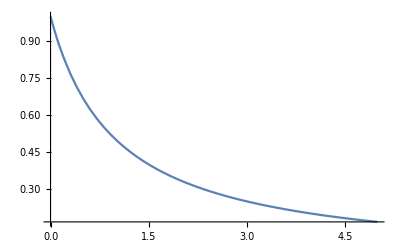

```mathematica
f[x_]:=1/(x+1)
Plot[f[x],{x,0,5}]
```

```mathematica
{Sum[f[k],{k,1,5}],Integrate[f[s],{s,0,5}],Sum[f[k],{k,0,4}]}//N
```

{1.45,1.79176,2.28333}

```mathematica
g[n_]:=Module[{v},If[n==2,
v="A",
If[n==3,
v="B",
v="Neither"
];
];
v
]/;IntegerQ[n]
```

## (* ERROR: - Enumerator for p q r - Dev - BUG *)

```mathematica
enumpq[n_]:=Module[{k=0,lst={}},
For[i=1,i<=n,i++,
For[j=1,j<i,j++,
k++;
lst=Append[lst,Prime[i]*Prime[j]];
];
];
lst
];
```

```mathematica
Select[enumpq[15],#<=100&]
```

{6,10,15,14,21,35,22,33,55,77,26,39,65,91,34,51,85,38,57,95,46,69,58,87,62,93,74,82,86,94}

```mathematica
enumpqr[n_]:=Module[{k=0,lst={}},
For[i=3,i<=n,i++,
For[j=1,j<=Prime[i],j++,
If[Mod[enumpq[[j]],Prime[i]]==0,Break[]];
k++;
Print[{k,l11[[j]]Prime[i]}];
];
]
]
```

## Bakjes-Info-[TBD]

```mathematica
viaPrt[n_]:=Flatten[Map[IntegerPartitions[#]&,Range[n]],1]
viaNum[n_]:=Module[{ls},
lst={};
For[i=2,i<n,i++,
lst=Append[lst,FactorInteger[i][[All,2]]]
];
Sort[DeleteDuplicates[DeleteDuplicates[lst,Sort[#1]==Sort[#2]&]]]
]

viaNum2[n_]:=Module[{ls},
lst={{0}};
For[i=2,i<(n+1),i++,
lst=Append[lst,Reverse[Sort[FactorInteger[i][[All,2]]]]]
];
lst
]

viaNum3[n_]:=Module[{ls},
lst={{0 ,{0}}};
For[i=2,i<(n+1),i++,
	lst=Append[lst,{Reverse[Sort[FactorInteger[i][[All,2]]]]}
]
];
lst
]
```

## Experiments: container (“Bakjes”) size

### Code to Transfer to Number Theory Package

```mathematica
nGetPrimeSignature[n_]:=Sort[FactorInteger[n][[All,2]]]

nBuildPrimeSignatureContainers[n_]:=Module[{assoc},
assoc=<|{0}->{1}|>;
If[
MissingQ[Lookup[assoc,{nGetPrimeSignature[#]}][[1]]],
assoc=AssociateTo[assoc,nGetPrimeSignature[#]->{#}],
assoc=AssociateTo[assoc,nGetPrimeSignature[#]->Append[Key[nGetPrimeSignature[#]][assoc],#]] 
]&/@Range[2,n];
assoc
]
```

### Alpha Tests

```mathematica
ds=nBuildPrimeSignatureContainers[100]//Dataset;
Normal[Values[KeySelect[ds,#=={1,1,1}&]]][[1]]//FactorInteger
```

{{{2,1},{3,1},{5,1}},{{2,1},{3,1},{7,1}},{{2,1},{3,1},{11,1}},{{2,1},{5,1},{7,1}},{{2,1},{3,1},{13,1}}}

### Building Subtrees

```mathematica
Prime[Range[PrimePi[10]]]
Normal[Values[KeySelect[ds,#=={1,1}&]]]
```

{2,3,5,7}

{{6,10,14,15,21,22,26,33,34,35,38,39,46,51,55,57,58,62,65,69,74,77,82,85,86,87,91,93,94,95}}

```mathematica
ls=(KeySelect[ds,#=={1,1}&]//Values//Normal)[[1]]

ls2=Select[ls,Not[Divisible[#,2]]&];
Complement[ls,ls2]

ls3=Select[ls2,Not[Divisible[#,3]]&];
Complement[ls2,ls3]

ls5=Select[ls3,Not[Divisible[#,5]]&];
Complement[ls3,ls5]

ls7=Select[ls5,Not[Divisible[#,7]]&];
Complement[ls5,ls7]

Union[ls,ls2,ls3,ls5,ls7]
FactorInteger[Union[ls,ls2,ls3,ls5,ls7]]
```

{6,10,14,15,21,22,26,33,34,35,38,39,46,51,55,57,58,62,65,69,74,77,82,85,86,87,91,93,94,95}

{6,10,14,22,26,34,38,46,58,62,74,82,86,94}

{15,21,33,39,51,57,69,87,93}

{35,55,65,85,95}

{77,91}

{6,10,14,15,21,22,26,33,34,35,38,39,46,51,55,57,58,62,65,69,74,77,82,85,86,87,91,93,94,95}

{{{2,1},{3,1}},{{2,1},{5,1}},{{2,1},{7,1}},{{3,1},{5,1}},{{3,1},{7,1}},{{2,1},{11,1}},{{2,1},{13,1}},{{3,1},{11,1}},{{2,1},{17,1}},{{5,1},{7,1}},{{2,1},{19,1}},{{3,1},{13,1}},{{2,1},{23,1}},{{3,1},{17,1}},{{5,1},{11,1}},{{3,1},{19,1}},{{2,1},{29,1}},{{2,1},{31,1}},{{5,1},{13,1}},{{3,1},{23,1}},{{2,1},{37,1}},{{7,1},{11,1}},{{2,1},{41,1}},{{5,1},{17,1}},{{2,1},{43,1}},{{3,1},{29,1}},{{7,1},{13,1}},{{3,1},{31,1}},{{2,1},{47,1}},{{5,1},{19,1}}}

## Bakjes R&D Devs

## Prototype-1 ( Without prsig={1,1} )

```mathematica
nGetPrimeSignature[n_]:=Sort[FactorInteger[n][[All,2]]]

nBuildPrimeSignatureContainers[n_]:=Module[{assoc,k,prsig,m},

assoc=<|{0}->{1}|>;
For[k=2,k<=n,k++,
prsig=nGetPrimeSignature[k];
If[
MissingQ[Lookup[assoc,{prsig}][[1]]],
AssociateTo[assoc,prsig->{k}],
assoc=AssociateTo[assoc,prsig->Append[Key[prsig][assoc],k]] ;
];
];
assoc
]                                                                                                                                                                                                                                              

nBuildPrimeSignatureContainers[31]
```

<|{0}→{1},{1}→{2,3,5,7,11,13,17,19,23,29,31},{2}→{4,9,25},{1,1}→{6,10,14,15,21,22,26},{3}→{8,27},{1,2}→{12,18,20,28},{4}→{16},{1,3}→{24},{1,1,1}→{30}|>

## Prototype-2: ( Without prsig = {1,1,1, ...} ) /* Code likely NOT optimal / efficient */

```mathematica
nGetPrimeSignature[n_]:=Sort[FactorInteger[n][[All,2]]]

nBuildPrimeSignatureContainers[n_]:=Module[{assoc,k,prsig,m},
assoc=<|{0}->{1}|>;

For[k=2,k<=n,k++,
prsig=nGetPrimeSignature[k];
m=Sort[FactorInteger[k][[All,1]]][[1]];
If[prsig=={1,1},
If[MissingQ[assoc[[Key[prsig]]]],
assoc=Association[assoc,prsig-><|{m,"p"}->{k}|>];,
If[MissingQ[assoc[prsig][{m,"p"}]],
assoc[prsig]=Association[Key[prsig][assoc],{m,"p"}->{k}],
AppendTo[assoc[prsig][{m,"p"}],k];
];
];,
If[MissingQ[assoc[[Key[prsig]]]],
assoc=Association[assoc,prsig->{k}],
AppendTo[assoc[[Key[prsig]]],k]];
];
];
assoc
]
```

### Demonstrations / Test-runs

```mathematica
data=Timing[nBuildPrimeSignatureContainers[100]]
```

{0.,<|{0}→{1},{1}→{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97},{2}→{4,9,25,49},{1,1}→<|{2,p}→{6,10,14,22,26,34,38,46,58,62,74,82,86,94},{3,p}→{15,21,33,39,51,57,69,87,93},{5,p}→{35,55,65,85,95},{7,p}→{77,91}|>,{3}→{8,27},{1,2}→{12,18,20,28,44,45,50,52,63,68,75,76,92,98,99},{4}→{16,81},{1,3}→{24,40,54,56,88},{1,1,1}→{30,42,66,70,78},{5}→{32},{2,2}→{36,100},{1,4}→{48,80},{1,1,2}→{60,84,90},{6}→{64},{2,3}→{72},{1,5}→{96}|>}

```mathematica
data//Dataset
```

### Other subject---

```mathematica
Table[StirlingS2[n,k],{n,0,12},{k,0,n}]//tf
```

1 |  |  |  |  |  |  |  |  |  |  |  | 
0 | 1 |  |  |  |  |  |  |  |  |  |  | 
0 | 1 | 1 |  |  |  |  |  |  |  |  |  | 
0 | 1 | 3 | 1 |  |  |  |  |  |  |  |  | 
0 | 1 | 7 | 6 | 1 |  |  |  |  |  |  |  | 
0 | 1 | 15 | 25 | 10 | 1 |  |  |  |  |  |  | 
0 | 1 | 31 | 90 | 65 | 15 | 1 |  |  |  |  |  | 
0 | 1 | 63 | 301 | 350 | 140 | 21 | 1 |  |  |  |  | 
0 | 1 | 127 | 966 | 1701 | 1050 | 266 | 28 | 1 |  |  |  | 
0 | 1 | 255 | 3025 | 7770 | 6951 | 2646 | 462 | 36 | 1 |  |  | 
0 | 1 | 511 | 9330 | 34105 | 42525 | 22827 | 5880 | 750 | 45 | 1 |  | 
0 | 1 | 1023 | 28501 | 145750 | 246730 | 179487 | 63987 | 11880 | 1155 | 55 | 1 | 
0 | 1 | 2047 | 86526 | 611501 | 1379400 | 1323652 | 627396 | 159027 | 22275 | 1705 | 66 | 1

```mathematica
2^4 3^4 5^1 7^1
Divisors[2^4 3^4 5^1 7^1]//Length
Divisors[2^4 3^4 5^1 7^1]
11^3 13^4 17^4
Divisors[11^3 13^4 17^4]//Length
Divisors[11^3 13^4 17^4]
Divisors[11^8]//Length
```

45360

100

{1,2,3,4,5,6,7,8,9,10,12,14,15,16,18,20,21,24,27,28,30,35,36,40,42,45,48,54,56,60,63,70,72,80,81,84,90,105,108,112,120,126,135,140,144,162,168,180,189,210,216,240,252,270,280,315,324,336,360,378,405,420,432,504,540,560,567,630,648,720,756,810,840,945,1008,1080,1134,1260,1296,1512,1620,1680,1890,2160,2268,2520,2835,3024,3240,3780,4536,5040,5670,6480,7560,9072,11340,15120,22680,45360}

3175025007011

100

{1,11,13,17,121,143,169,187,221,289,1331,1573,1859,2057,2197,2431,2873,3179,3757,4913,17303,20449,22627,24167,26741,28561,31603,34969,37349,41327,48841,54043,63869,83521,224939,265837,294151,314171,347633,384659,410839,454597,485537,537251,594473,634933,702559,830297,918731,1085773,2924207,3455881,3823963,4519229,5000567,5340907,5909761,6539203,6984263,7728149,8254129,9133267,10106041,10793861,11943503,14115049,38014691,49711519,58749977,65007371,76826893,85009639,90795419,100465937,111166451,118732471,131378533,140320193,155265539,183495637,646249747,845095823,998749609,1105125307,1306057181,1445163863,1543522123,1707920929,2018452007,2385443281,10986245699,14366628991,16978743353,18787130219,22202972077,26239876091,186766176883,244232692847,288638637001,3175025007011}

9

```mathematica
IntegerName[1000000,{"Dutch"}]
IntegerName[1000000000,{"Dutch"}]
IntegerName[1000000000000,{"Dutch"}]
IntegerName[1000000000000000,{"Dutch"}]

IntegerName[1000000]
IntegerName[1000000000]
IntegerName[1000000000000]
IntegerName[1000000000000000]
```

een miljoen

een miljard

een biljoen

een biljard

1 million

1 billion

1 trillion

1 quadrillion

```mathematica
X={a,b,c}
```

{a,b,c}

```mathematica
nGetPrimeSignature[100]
```

{2,2}

```mathematica
FactorInteger[100]
```

{{2,2},{5,2}}

```mathematica
Y={2,2,5,5};
DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]
```

{{{2,2,5,5}},{{2},{2,5,5}},{{2,2},{5,5}},{{5},{2,2,5}},{{2,5},{2,5}},{{2},{2},{5,5}},{{2},{5},{2,5}},{{5},{5},{2,2}},{{2},{2},{5},{5}}}

```mathematica
Array[2&,2]
```

{2,2}

```mathematica
ClearAll[f]
f[{x_,y_}]:=Array[x&,y]
f[{2,3}]
f[{3,2}]
```

{2,2,2}

{3,3}

```mathematica
Y=Flatten[Append[Append[f[{2,3}],f[{3,1}]],f[{5,1}]]]
DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]//Length
```

{2,2,2,3,5}

21

```mathematica
Join[{1},{3,3,4},{5}]
```

{1,3,3,4,5}

```mathematica
Y=Map[f[{#[[1]],#[[2]]}]&,FactorInteger[96]]//Flatten
DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]//Length
Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]]
```

{f[{2,5}],f[{3,1}]}

2

{{{f[{2,5}],f[{3,1}]}},{{f[{2,5}]},{f[{3,1}]}}}

```mathematica
lst={
{{2,2,2,2,2,3}},
{{2},{2,2,2,2,3}},
{{2,2},{2,2,2,3}},
{{2,2,2},{2,2,3}},
{{2,3},{2,2,2,2}},
{{3},{2,2,2,2,2}},
{{2},{2},{2,2,2,3}},
{{2},{2,2},{2,2,3}},
{{2},{2,3},{2,2,2}},
{{2},{3},{2,2,2,2}},
{{2,2},{2,2},{2,3}},
{{3},{2,2},{2,2,2}},{{2},{2},{2},{2,2,3}},{{2},{2},{2,2},{2,3}},{{2},{2},{3},{2,2,2}},{{2},{3},{2,2},{2,2}},{{2},{2},{2},{2},{2,3}},{{2},{2},{2},{3},{2,2}},{{2},{2},{2},{2},{2},{3}}};
```

```mathematica
Map[Apply[Times,#]&,lst,{2}]//tf
```

96 |  |  |  |  | 
2 | 48 |  |  |  | 
4 | 24 |  |  |  | 
8 | 12 |  |  |  | 
6 | 16 |  |  |  | 
3 | 32 |  |  |  | 
2 | 2 | 24 |  |  | 
2 | 4 | 12 |  |  | 
2 | 6 | 8 |  |  | 
2 | 3 | 16 |  |  | 
4 | 4 | 6 |  |  | 
3 | 4 | 8 |  |  | 
2 | 2 | 2 | 12 |  | 
2 | 2 | 4 | 6 |  | 
2 | 2 | 3 | 8 |  | 
2 | 3 | 4 | 4 |  | 
2 | 2 | 2 | 2 | 6 | 
2 | 2 | 2 | 3 | 4 | 
2 | 2 | 2 | 2 | 2 | 3

```mathematica
Apply[Times,{2,3,4}]
```

24

```mathematica
FactorInteger[420]
```

{{2,2},{3,1},{5,1},{7,1}}

```mathematica
(* iets met Function *)
ClearAll[f]
f[{x_,y_}]:=Array[x&,y]
Y=Map[f[{#[[1]],#[[2]]}]&,FactorInteger[2 2 3 3]]//Flatten
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]//Length
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]//tf
```

{2,2,3,3}

9

{{36},{2,18},{4,9},{3,12},{6,6},{2,2,9},{2,3,6},{3,3,4},{2,2,3,3}}

36 |  |  | 
2 | 18 |  | 
4 | 9 |  | 
3 | 12 |  | 
6 | 6 |  | 
2 | 2 | 9 | 
2 | 3 | 6 | 
3 | 3 | 4 | 
2 | 2 | 3 | 3

```mathematica
ClearAll[f]
f[{x_,y_}]:=Array[x&,y]
Y=Map[f[{#[[1]],#[[2]]}]&,FactorInteger[2 2 2 3 3]]//Flatten
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]//Length
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]//tf
```

{2,2,2,3,3}

16

{{72},{2,36},{4,18},{9,8},{3,24},{6,12},{2,2,18},{2,4,9},{2,3,12},{2,6,6},{3,4,6},{3,3,8},{2,2,2,9},{2,2,3,6},{2,3,3,4},{2,2,2,3,3}}

72 |  |  |  | 
2 | 36 |  |  | 
4 | 18 |  |  | 
9 | 8 |  |  | 
3 | 24 |  |  | 
6 | 12 |  |  | 
2 | 2 | 18 |  | 
2 | 4 | 9 |  | 
2 | 3 | 12 |  | 
2 | 6 | 6 |  | 
3 | 4 | 6 |  | 
3 | 3 | 8 |  | 
2 | 2 | 2 | 9 | 
2 | 2 | 3 | 6 | 
2 | 3 | 3 | 4 | 
2 | 2 | 2 | 3 | 3

```mathematica
Y=Map[f[{#[[1]],#[[2]]}]&,FactorInteger[2 3 3 ]]//Flatten
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]
```

{2,3,3}

{{18},{2,9},{3,6},{2,3,3}}

```mathematica
Y=Map[f[{#[[1]],#[[2]]}]&,FactorInteger[6]]//Flatten
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]
```

{2,3}

{{6},{2,3}}

```mathematica
Y=Map[f[{#[[1]],#[[2]]}]&,FactorInteger[12]]//Flatten
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]
```

{2,2,3}

{{12},{2,6},{3,4},{2,2,3}}

### tmp

```mathematica
ClearAll[f]
f[{x_,y_}]:=Array[x&,y]
Y=Map[f[{#[[1]],#[[2]]}]&,FactorInteger[2 2 3 3]]//Flatten
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]//Length
```

```mathematica
ClearAll[f]
f[{x_,y_}]:=Array[x&,y]
Y=Map[f[{#[[1]],#[[2]]}]&,FactorInteger[2 2 3 3]]//Flatten
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]//Length
```

```mathematica
Flatten[Map[Function[x,Array[x[[1]]&,x [[2]]]],FactorInteger[72]]]
```

{{2,2,2},{3,3}}

```mathematica
nFactorListInteger[n_]:=Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Flatten[Map[Function[x,Array[x[[1]]&,x [[2]]]],FactorInteger[n]]]]]]],{2}]
```

```mathematica
Timing[Sort[Map[Sort[#]&,nFactorListInteger[2 3^2 5^2 7^6]]]//Length]
Timing[nFactorListInteger[2 3^2 5^2 7^6]//tf]
```

{5.625,3930}

{5.6875,52942050 |  |  |  |  |  |  |  |  |  | 
2 | 26471025 |  |  |  |  |  |  |  |  | 
6 | 8823675 |  |  |  |  |  |  |  |  | 
3 | 17647350 |  |  |  |  |  |  |  |  | 
18 | 2941225 |  |  |  |  |  |  |  |  | 
9 | 5882450 |  |  |  |  |  |  |  |  | 
90 | 588245 |  |  |  |  |  |  |  |  | 
45 | 1176490 |  |  |  |  |  |  |  |  | 
15 | 3529470 |  |  |  |  |  |  |  |  | 
30 | 1764735 |  |  |  |  |  |  |  |  | 
5 | 10588410 |  |  |  |  |  |  |  |  | 
10 | 5294205 |  |  |  |  |  |  |  |  | 
450 | 117649 |  |  |  |  |  |  |  |  | 
225 | 235298 |  |  |  |  |  |  |  |  | 
75 | 705894 |  |  |  |  |  |  |  |  | 
150 | 352947 |  |  |  |  |  |  |  |  | 
25 | 2117682 |  |  |  |  |  |  |  |  | 
50 | 1058841 |  |  |  |  |  |  |  |  | 
16807 | 3150 |  |  |  |  |  |  |  |  | 
1575 | 33614 |  |  |  |  |  |  |  |  | 
525 | 100842 |  |  |  |  |  |  |  |  | 
1050 | 50421 |  |  |  |  |  |  |  |  | 
175 | 302526 |  |  |  |  |  |  |  |  | 
350 | 151263 |  |  |  |  |  |  |  |  | 
35 | 1512630 |  |  |  |  |  |  |  |  | 
70 | 756315 |  |  |  |  |  |  |  |  | 
210 | 252105 |  |  |  |  |  |  |  |  | 
105 | 504210 |  |  |  |  |  |  |  |  | 
630 | 84035 |  |  |  |  |  |  |  |  | 
315 | 168070 |  |  |  |  |  |  |  |  | 
7 | 7563150 |  |  |  |  |  |  |  |  | 
14 | 3781575 |  |  |  |  |  |  |  |  | 
42 | 1260525 |  |  |  |  |  |  |  |  | 
21 | 2521050 |  |  |  |  |  |  |  |  | 
126 | 420175 |  |  |  |  |  |  |  |  | 
63 | 840350 |  |  |  |  |  |  |  |  | 
2401 | 22050 |  |  |  |  |  |  |  |  | 
4802 | 11025 |  |  |  |  |  |  |  |  | 
3675 | 14406 |  |  |  |  |  |  |  |  | 
7203 | 7350 |  |  |  |  |  |  |  |  | 
1225 | 43218 |  |  |  |  |  |  |  |  | 
2450 | 21609 |  |  |  |  |  |  |  |  | 
245 | 216090 |  |  |  |  |  |  |  |  | 
490 | 108045 |  |  |  |  |  |  |  |  | 
1470 | 36015 |  |  |  |  |  |  |  |  | 
735 | 72030 |  |  |  |  |  |  |  |  | 
12005 | 4410 |  |  |  |  |  |  |  |  | 
2205 | 24010 |  |  |  |  |  |  |  |  | 
49 | 1080450 |  |  |  |  |  |  |  |  | 
98 | 540225 |  |  |  |  |  |  |  |  | 
294 | 180075 |  |  |  |  |  |  |  |  | 
147 | 360150 |  |  |  |  |  |  |  |  | 
882 | 60025 |  |  |  |  |  |  |  |  | 
441 | 120050 |  |  |  |  |  |  |  |  | 
343 | 154350 |  |  |  |  |  |  |  |  | 
686 | 77175 |  |  |  |  |  |  |  |  | 
2058 | 25725 |  |  |  |  |  |  |  |  | 
1029 | 51450 |  |  |  |  |  |  |  |  | 
8575 | 6174 |  |  |  |  |  |  |  |  | 
3087 | 17150 |  |  |  |  |  |  |  |  | 
1715 | 30870 |  |  |  |  |  |  |  |  | 
3430 | 15435 |  |  |  |  |  |  |  |  | 
5145 | 10290 |  |  |  |  |  |  |  |  | 
2 | 3 | 8823675 |  |  |  |  |  |  |  | 
2 | 9 | 2941225 |  |  |  |  |  |  |  | 
2 | 45 | 588245 |  |  |  |  |  |  |  | 
2 | 15 | 1764735 |  |  |  |  |  |  |  | 
2 | 5 | 5294205 |  |  |  |  |  |  |  | 
2 | 225 | 117649 |  |  |  |  |  |  |  | 
2 | 75 | 352947 |  |  |  |  |  |  |  | 
2 | 25 | 1058841 |  |  |  |  |  |  |  | 
2 | 1575 | 16807 |  |  |  |  |  |  |  | 
2 | 525 | 50421 |  |  |  |  |  |  |  | 
2 | 175 | 151263 |  |  |  |  |  |  |  | 
2 | 35 | 756315 |  |  |  |  |  |  |  | 
2 | 105 | 252105 |  |  |  |  |  |  |  | 
2 | 315 | 84035 |  |  |  |  |  |  |  | 
2 | 7 | 3781575 |  |  |  |  |  |  |  | 
2 | 21 | 1260525 |  |  |  |  |  |  |  | 
2 | 63 | 420175 |  |  |  |  |  |  |  | 
2 | 2401 | 11025 |  |  |  |  |  |  |  | 
2 | 3675 | 7203 |  |  |  |  |  |  |  | 
2 | 1225 | 21609 |  |  |  |  |  |  |  | 
2 | 245 | 108045 |  |  |  |  |  |  |  | 
2 | 735 | 36015 |  |  |  |  |  |  |  | 
2 | 2205 | 12005 |  |  |  |  |  |  |  | 
2 | 49 | 540225 |  |  |  |  |  |  |  | 
2 | 147 | 180075 |  |  |  |  |  |  |  | 
2 | 441 | 60025 |  |  |  |  |  |  |  | 
2 | 343 | 77175 |  |  |  |  |  |  |  | 
2 | 1029 | 25725 |  |  |  |  |  |  |  | 
2 | 3087 | 8575 |  |  |  |  |  |  |  | 
2 | 1715 | 15435 |  |  |  |  |  |  |  | 
2 | 5145 | 5145 |  |  |  |  |  |  |  | 
3 | 6 | 2941225 |  |  |  |  |  |  |  | 
3 | 3 | 5882450 |  |  |  |  |  |  |  | 
6 | 15 | 588245 |  |  |  |  |  |  |  | 
3 | 30 | 588245 |  |  |  |  |  |  |  | 
3 | 15 | 1176490 |  |  |  |  |  |  |  | 
5 | 6 | 1764735 |  |  |  |  |  |  |  | 
3 | 5 | 3529470 |  |  |  |  |  |  |  | 
3 | 10 | 1764735 |  |  |  |  |  |  |  | 
6 | 75 | 117649 |  |  |  |  |  |  |  | 
3 | 150 | 117649 |  |  |  |  |  |  |  | 
3 | 75 | 235298 |  |  |  |  |  |  |  | 
6 | 25 | 352947 |  |  |  |  |  |  |  | 
3 | 25 | 705894 |  |  |  |  |  |  |  | 
3 | 50 | 352947 |  |  |  |  |  |  |  | 
6 | 525 | 16807 |  |  |  |  |  |  |  | 
3 | 1050 | 16807 |  |  |  |  |  |  |  | 
3 | 525 | 33614 |  |  |  |  |  |  |  | 
6 | 175 | 50421 |  |  |  |  |  |  |  | 
3 | 175 | 100842 |  |  |  |  |  |  |  | 
3 | 350 | 50421 |  |  |  |  |  |  |  | 
6 | 35 | 252105 |  |  |  |  |  |  |  | 
3 | 35 | 504210 |  |  |  |  |  |  |  | 
3 | 70 | 252105 |  |  |  |  |  |  |  | 
6 | 105 | 84035 |  |  |  |  |  |  |  | 
3 | 210 | 84035 |  |  |  |  |  |  |  | 
3 | 105 | 168070 |  |  |  |  |  |  |  | 
7 | 6 | 1260525 |  |  |  |  |  |  |  | 
3 | 7 | 2521050 |  |  |  |  |  |  |  | 
3 | 14 | 1260525 |  |  |  |  |  |  |  | 
6 | 21 | 420175 |  |  |  |  |  |  |  | 
3 | 42 | 420175 |  |  |  |  |  |  |  | 
3 | 21 | 840350 |  |  |  |  |  |  |  | 
6 | 2401 | 3675 |  |  |  |  |  |  |  | 
3 | 2401 | 7350 |  |  |  |  |  |  |  | 
3 | 4802 | 3675 |  |  |  |  |  |  |  | 
6 | 1225 | 7203 |  |  |  |  |  |  |  | 
3 | 1225 | 14406 |  |  |  |  |  |  |  | 
3 | 2450 | 7203 |  |  |  |  |  |  |  | 
6 | 245 | 36015 |  |  |  |  |  |  |  | 
3 | 245 | 72030 |  |  |  |  |  |  |  | 
3 | 490 | 36015 |  |  |  |  |  |  |  | 
6 | 735 | 12005 |  |  |  |  |  |  |  | 
3 | 1470 | 12005 |  |  |  |  |  |  |  | 
3 | 735 | 24010 |  |  |  |  |  |  |  | 
6 | 49 | 180075 |  |  |  |  |  |  |  | 
3 | 49 | 360150 |  |  |  |  |  |  |  | 
3 | 98 | 180075 |  |  |  |  |  |  |  | 
6 | 147 | 60025 |  |  |  |  |  |  |  | 
3 | 294 | 60025 |  |  |  |  |  |  |  | 
3 | 147 | 120050 |  |  |  |  |  |  |  | 
6 | 343 | 25725 |  |  |  |  |  |  |  | 
3 | 343 | 51450 |  |  |  |  |  |  |  | 
3 | 686 | 25725 |  |  |  |  |  |  |  | 
6 | 1029 | 8575 |  |  |  |  |  |  |  | 
3 | 2058 | 8575 |  |  |  |  |  |  |  | 
3 | 1029 | 17150 |  |  |  |  |  |  |  | 
6 | 1715 | 5145 |  |  |  |  |  |  |  | 
3 | 1715 | 10290 |  |  |  |  |  |  |  | 
3 | 3430 | 5145 |  |  |  |  |  |  |  | 
5 | 18 | 588245 |  |  |  |  |  |  |  | 
10 | 9 | 588245 |  |  |  |  |  |  |  | 
5 | 9 | 1176490 |  |  |  |  |  |  |  | 
25 | 18 | 117649 |  |  |  |  |  |  |  | 
9 | 50 | 117649 |  |  |  |  |  |  |  | 
9 | 25 | 235298 |  |  |  |  |  |  |  | 
18 | 175 | 16807 |  |  |  |  |  |  |  | 
9 | 350 | 16807 |  |  |  |  |  |  |  | 
9 | 175 | 33614 |  |  |  |  |  |  |  | 
35 | 18 | 84035 |  |  |  |  |  |  |  | 
9 | 35 | 168070 |  |  |  |  |  |  |  | 
9 | 70 | 84035 |  |  |  |  |  |  |  | 
7 | 18 | 420175 |  |  |  |  |  |  |  | 
7 | 9 | 840350 |  |  |  |  |  |  |  | 
14 | 9 | 420175 |  |  |  |  |  |  |  | 
18 | 1225 | 2401 |  |  |  |  |  |  |  | 
9 | 2401 | 2450 |  |  |  |  |  |  |  | 
9 | 1225 | 4802 |  |  |  |  |  |  |  | 
18 | 245 | 12005 |  |  |  |  |  |  |  | 
9 | 245 | 24010 |  |  |  |  |  |  |  | 
9 | 490 | 12005 |  |  |  |  |  |  |  | 
49 | 18 | 60025 |  |  |  |  |  |  |  | 
9 | 49 | 120050 |  |  |  |  |  |  |  | 
9 | 98 | 60025 |  |  |  |  |  |  |  | 
18 | 343 | 8575 |  |  |  |  |  |  |  | 
9 | 343 | 17150 |  |  |  |  |  |  |  | 
9 | 686 | 8575 |  |  |  |  |  |  |  | 
18 | 1715 | 1715 |  |  |  |  |  |  |  | 
9 | 1715 | 3430 |  |  |  |  |  |  |  | 
5 | 90 | 117649 |  |  |  |  |  |  |  | 
10 | 45 | 117649 |  |  |  |  |  |  |  | 
5 | 45 | 235298 |  |  |  |  |  |  |  | 
15 | 30 | 117649 |  |  |  |  |  |  |  | 
15 | 15 | 235298 |  |  |  |  |  |  |  | 
5 | 15 | 705894 |  |  |  |  |  |  |  | 
5 | 30 | 352947 |  |  |  |  |  |  |  | 
10 | 15 | 352947 |  |  |  |  |  |  |  | 
5 | 5 | 2117682 |  |  |  |  |  |  |  | 
5 | 10 | 1058841 |  |  |  |  |  |  |  | 
35 | 90 | 16807 |  |  |  |  |  |  |  | 
70 | 45 | 16807 |  |  |  |  |  |  |  | 
35 | 45 | 33614 |  |  |  |  |  |  |  | 
15 | 210 | 16807 |  |  |  |  |  |  |  | 
30 | 105 | 16807 |  |  |  |  |  |  |  | 
15 | 105 | 33614 |  |  |  |  |  |  |  | 
15 | 35 | 100842 |  |  |  |  |  |  |  | 
35 | 30 | 50421 |  |  |  |  |  |  |  | 
15 | 70 | 50421 |  |  |  |  |  |  |  | 
5 | 630 | 16807 |  |  |  |  |  |  |  | 
10 | 315 | 16807 |  |  |  |  |  |  |  | 
5 | 315 | 33614 |  |  |  |  |  |  |  | 
5 | 105 | 100842 |  |  |  |  |  |  |  | 
5 | 210 | 50421 |  |  |  |  |  |  |  | 
10 | 105 | 50421 |  |  |  |  |  |  |  | 
5 | 35 | 302526 |  |  |  |  |  |  |  | 
10 | 35 | 151263 |  |  |  |  |  |  |  | 
5 | 70 | 151263 |  |  |  |  |  |  |  | 
7 | 90 | 84035 |  |  |  |  |  |  |  | 
7 | 45 | 168070 |  |  |  |  |  |  |  | 
14 | 45 | 84035 |  |  |  |  |  |  |  | 
7 | 15 | 504210 |  |  |  |  |  |  |  | 
7 | 30 | 252105 |  |  |  |  |  |  |  | 
14 | 15 | 252105 |  |  |  |  |  |  |  | 
15 | 42 | 84035 |  |  |  |  |  |  |  | 
21 | 30 | 84035 |  |  |  |  |  |  |  | 
15 | 21 | 168070 |  |  |  |  |  |  |  | 
5 | 7 | 1512630 |  |  |  |  |  |  |  | 
7 | 10 | 756315 |  |  |  |  |  |  |  | 
5 | 14 | 756315 |  |  |  |  |  |  |  | 
5 | 42 | 252105 |  |  |  |  |  |  |  | 
5 | 21 | 504210 |  |  |  |  |  |  |  | 
10 | 21 | 252105 |  |  |  |  |  |  |  | 
5 | 126 | 84035 |  |  |  |  |  |  |  | 
10 | 63 | 84035 |  |  |  |  |  |  |  | 
5 | 63 | 168070 |  |  |  |  |  |  |  | 
245 | 90 | 2401 |  |  |  |  |  |  |  | 
45 | 490 | 2401 |  |  |  |  |  |  |  | 
45 | 245 | 4802 |  |  |  |  |  |  |  | 
15 | 2401 | 1470 |  |  |  |  |  |  |  | 
30 | 735 | 2401 |  |  |  |  |  |  |  | 
15 | 735 | 4802 |  |  |  |  |  |  |  | 
15 | 245 | 14406 |  |  |  |  |  |  |  | 
30 | 245 | 7203 |  |  |  |  |  |  |  | 
15 | 490 | 7203 |  |  |  |  |  |  |  | 
5 | 2401 | 4410 |  |  |  |  |  |  |  | 
10 | 2401 | 2205 |  |  |  |  |  |  |  | 
5 | 4802 | 2205 |  |  |  |  |  |  |  | 
5 | 735 | 14406 |  |  |  |  |  |  |  | 
5 | 1470 | 7203 |  |  |  |  |  |  |  | 
10 | 735 | 7203 |  |  |  |  |  |  |  | 
5 | 245 | 43218 |  |  |  |  |  |  |  | 
10 | 245 | 21609 |  |  |  |  |  |  |  | 
5 | 490 | 21609 |  |  |  |  |  |  |  | 
49 | 90 | 12005 |  |  |  |  |  |  |  | 
49 | 45 | 24010 |  |  |  |  |  |  |  | 
98 | 45 | 12005 |  |  |  |  |  |  |  | 
15 | 49 | 72030 |  |  |  |  |  |  |  | 
49 | 30 | 36015 |  |  |  |  |  |  |  | 
15 | 98 | 36015 |  |  |  |  |  |  |  | 
15 | 294 | 12005 |  |  |  |  |  |  |  | 
30 | 147 | 12005 |  |  |  |  |  |  |  | 
15 | 147 | 24010 |  |  |  |  |  |  |  | 
5 | 49 | 216090 |  |  |  |  |  |  |  | 
10 | 49 | 108045 |  |  |  |  |  |  |  | 
5 | 98 | 108045 |  |  |  |  |  |  |  | 
5 | 294 | 36015 |  |  |  |  |  |  |  | 
5 | 147 | 72030 |  |  |  |  |  |  |  | 
10 | 147 | 36015 |  |  |  |  |  |  |  | 
5 | 882 | 12005 |  |  |  |  |  |  |  | 
10 | 441 | 12005 |  |  |  |  |  |  |  | 
5 | 441 | 24010 |  |  |  |  |  |  |  | 
343 | 90 | 1715 |  |  |  |  |  |  |  | 
45 | 343 | 3430 |  |  |  |  |  |  |  | 
45 | 686 | 1715 |  |  |  |  |  |  |  | 
15 | 343 | 10290 |  |  |  |  |  |  |  | 
30 | 343 | 5145 |  |  |  |  |  |  |  | 
15 | 686 | 5145 |  |  |  |  |  |  |  | 
15 | 1715 | 2058 |  |  |  |  |  |  |  | 
30 | 1029 | 1715 |  |  |  |  |  |  |  | 
15 | 1029 | 3430 |  |  |  |  |  |  |  | 
5 | 343 | 30870 |  |  |  |  |  |  |  | 
10 | 343 | 15435 |  |  |  |  |  |  |  | 
5 | 686 | 15435 |  |  |  |  |  |  |  | 
5 | 2058 | 5145 |  |  |  |  |  |  |  | 
5 | 1029 | 10290 |  |  |  |  |  |  |  | 
10 | 1029 | 5145 |  |  |  |  |  |  |  | 
5 | 1715 | 6174 |  |  |  |  |  |  |  | 
10 | 1715 | 3087 |  |  |  |  |  |  |  | 
5 | 3430 | 3087 |  |  |  |  |  |  |  | 
7 | 450 | 16807 |  |  |  |  |  |  |  | 
14 | 225 | 16807 |  |  |  |  |  |  |  | 
7 | 225 | 33614 |  |  |  |  |  |  |  | 
42 | 75 | 16807 |  |  |  |  |  |  |  | 
21 | 150 | 16807 |  |  |  |  |  |  |  | 
21 | 75 | 33614 |  |  |  |  |  |  |  | 
7 | 75 | 100842 |  |  |  |  |  |  |  | 
7 | 150 | 50421 |  |  |  |  |  |  |  | 
14 | 75 | 50421 |  |  |  |  |  |  |  | 
25 | 126 | 16807 |  |  |  |  |  |  |  | 
50 | 63 | 16807 |  |  |  |  |  |  |  | 
25 | 63 | 33614 |  |  |  |  |  |  |  | 
21 | 25 | 100842 |  |  |  |  |  |  |  | 
25 | 42 | 50421 |  |  |  |  |  |  |  | 
21 | 50 | 50421 |  |  |  |  |  |  |  | 
7 | 25 | 302526 |  |  |  |  |  |  |  | 
7 | 50 | 151263 |  |  |  |  |  |  |  | 
14 | 25 | 151263 |  |  |  |  |  |  |  | 
49 | 2401 | 450 |  |  |  |  |  |  |  | 
98 | 225 | 2401 |  |  |  |  |  |  |  | 
49 | 225 | 4802 |  |  |  |  |  |  |  | 
75 | 294 | 2401 |  |  |  |  |  |  |  | 
147 | 150 | 2401 |  |  |  |  |  |  |  | 
75 | 147 | 4802 |  |  |  |  |  |  |  | 
49 | 75 | 14406 |  |  |  |  |  |  |  | 
49 | 150 | 7203 |  |  |  |  |  |  |  | 
98 | 75 | 7203 |  |  |  |  |  |  |  | 
25 | 2401 | 882 |  |  |  |  |  |  |  | 
50 | 441 | 2401 |  |  |  |  |  |  |  | 
25 | 441 | 4802 |  |  |  |  |  |  |  | 
25 | 147 | 14406 |  |  |  |  |  |  |  | 
25 | 294 | 7203 |  |  |  |  |  |  |  | 
50 | 147 | 7203 |  |  |  |  |  |  |  | 
25 | 49 | 43218 |  |  |  |  |  |  |  | 
49 | 50 | 21609 |  |  |  |  |  |  |  | 
25 | 98 | 21609 |  |  |  |  |  |  |  | 
343 | 343 | 450 |  |  |  |  |  |  |  | 
343 | 686 | 225 |  |  |  |  |  |  |  | 
75 | 343 | 2058 |  |  |  |  |  |  |  | 
343 | 150 | 1029 |  |  |  |  |  |  |  | 
75 | 686 | 1029 |  |  |  |  |  |  |  | 
25 | 343 | 6174 |  |  |  |  |  |  |  | 
50 | 343 | 3087 |  |  |  |  |  |  |  | 
25 | 686 | 3087 |  |  |  |  |  |  |  | 
25 | 1029 | 2058 |  |  |  |  |  |  |  | 
50 | 1029 | 1029 |  |  |  |  |  |  |  | 
7 | 2401 | 3150 |  |  |  |  |  |  |  | 
14 | 2401 | 1575 |  |  |  |  |  |  |  | 
7 | 4802 | 1575 |  |  |  |  |  |  |  | 
42 | 525 | 2401 |  |  |  |  |  |  |  | 
21 | 2401 | 1050 |  |  |  |  |  |  |  | 
21 | 525 | 4802 |  |  |  |  |  |  |  | 
7 | 525 | 14406 |  |  |  |  |  |  |  | 
7 | 1050 | 7203 |  |  |  |  |  |  |  | 
14 | 525 | 7203 |  |  |  |  |  |  |  | 
175 | 126 | 2401 |  |  |  |  |  |  |  | 
63 | 350 | 2401 |  |  |  |  |  |  |  | 
63 | 175 | 4802 |  |  |  |  |  |  |  | 
21 | 175 | 14406 |  |  |  |  |  |  |  | 
42 | 175 | 7203 |  |  |  |  |  |  |  | 
21 | 350 | 7203 |  |  |  |  |  |  |  | 
7 | 175 | 43218 |  |  |  |  |  |  |  | 
7 | 350 | 21609 |  |  |  |  |  |  |  | 
14 | 175 | 21609 |  |  |  |  |  |  |  | 
35 | 2401 | 630 |  |  |  |  |  |  |  | 
70 | 315 | 2401 |  |  |  |  |  |  |  | 
35 | 315 | 4802 |  |  |  |  |  |  |  | 
105 | 210 | 2401 |  |  |  |  |  |  |  | 
105 | 105 | 4802 |  |  |  |  |  |  |  | 
35 | 105 | 14406 |  |  |  |  |  |  |  | 
35 | 210 | 7203 |  |  |  |  |  |  |  | 
70 | 105 | 7203 |  |  |  |  |  |  |  | 
35 | 35 | 43218 |  |  |  |  |  |  |  | 
35 | 70 | 21609 |  |  |  |  |  |  |  | 
7 | 35 | 216090 |  |  |  |  |  |  |  | 
7 | 70 | 108045 |  |  |  |  |  |  |  | 
14 | 35 | 108045 |  |  |  |  |  |  |  | 
7 | 210 | 36015 |  |  |  |  |  |  |  | 
7 | 105 | 72030 |  |  |  |  |  |  |  | 
14 | 105 | 36015 |  |  |  |  |  |  |  | 
35 | 42 | 36015 |  |  |  |  |  |  |  | 
21 | 35 | 72030 |  |  |  |  |  |  |  | 
21 | 70 | 36015 |  |  |  |  |  |  |  | 
7 | 630 | 12005 |  |  |  |  |  |  |  | 
7 | 315 | 24010 |  |  |  |  |  |  |  | 
14 | 315 | 12005 |  |  |  |  |  |  |  | 
42 | 105 | 12005 |  |  |  |  |  |  |  | 
21 | 210 | 12005 |  |  |  |  |  |  |  | 
21 | 105 | 24010 |  |  |  |  |  |  |  | 
35 | 126 | 12005 |  |  |  |  |  |  |  | 
35 | 63 | 24010 |  |  |  |  |  |  |  | 
70 | 63 | 12005 |  |  |  |  |  |  |  | 
7 | 7 | 1080450 |  |  |  |  |  |  |  | 
7 | 14 | 540225 |  |  |  |  |  |  |  | 
7 | 42 | 180075 |  |  |  |  |  |  |  | 
7 | 21 | 360150 |  |  |  |  |  |  |  | 
14 | 21 | 180075 |  |  |  |  |  |  |  | 
7 | 126 | 60025 |  |  |  |  |  |  |  | 
7 | 63 | 120050 |  |  |  |  |  |  |  | 
14 | 63 | 60025 |  |  |  |  |  |  |  | 
21 | 42 | 60025 |  |  |  |  |  |  |  | 
21 | 21 | 120050 |  |  |  |  |  |  |  | 
49 | 343 | 3150 |  |  |  |  |  |  |  | 
98 | 343 | 1575 |  |  |  |  |  |  |  | 
49 | 686 | 1575 |  |  |  |  |  |  |  | 
343 | 294 | 525 |  |  |  |  |  |  |  | 
147 | 343 | 1050 |  |  |  |  |  |  |  | 
147 | 686 | 525 |  |  |  |  |  |  |  | 
49 | 525 | 2058 |  |  |  |  |  |  |  | 
49 | 1029 | 1050 |  |  |  |  |  |  |  | 
98 | 525 | 1029 |  |  |  |  |  |  |  | 
175 | 343 | 882 |  |  |  |  |  |  |  | 
343 | 350 | 441 |  |  |  |  |  |  |  | 
175 | 686 | 441 |  |  |  |  |  |  |  | 
147 | 175 | 2058 |  |  |  |  |  |  |  | 
175 | 294 | 1029 |  |  |  |  |  |  |  | 
147 | 350 | 1029 |  |  |  |  |  |  |  | 
49 | 175 | 6174 |  |  |  |  |  |  |  | 
49 | 350 | 3087 |  |  |  |  |  |  |  | 
98 | 175 | 3087 |  |  |  |  |  |  |  | 
35 | 343 | 4410 |  |  |  |  |  |  |  | 
70 | 343 | 2205 |  |  |  |  |  |  |  | 
35 | 686 | 2205 |  |  |  |  |  |  |  | 
343 | 210 | 735 |  |  |  |  |  |  |  | 
105 | 343 | 1470 |  |  |  |  |  |  |  | 
105 | 686 | 735 |  |  |  |  |  |  |  | 
35 | 735 | 2058 |  |  |  |  |  |  |  | 
35 | 1029 | 1470 |  |  |  |  |  |  |  | 
70 | 735 | 1029 |  |  |  |  |  |  |  | 
245 | 343 | 630 |  |  |  |  |  |  |  | 
343 | 490 | 315 |  |  |  |  |  |  |  | 
245 | 686 | 315 |  |  |  |  |  |  |  | 
105 | 245 | 2058 |  |  |  |  |  |  |  | 
245 | 210 | 1029 |  |  |  |  |  |  |  | 
105 | 490 | 1029 |  |  |  |  |  |  |  | 
35 | 245 | 6174 |  |  |  |  |  |  |  | 
35 | 490 | 3087 |  |  |  |  |  |  |  | 
70 | 245 | 3087 |  |  |  |  |  |  |  | 
35 | 49 | 30870 |  |  |  |  |  |  |  | 
49 | 70 | 15435 |  |  |  |  |  |  |  | 
35 | 98 | 15435 |  |  |  |  |  |  |  | 
49 | 210 | 5145 |  |  |  |  |  |  |  | 
49 | 105 | 10290 |  |  |  |  |  |  |  | 
98 | 105 | 5145 |  |  |  |  |  |  |  | 
35 | 294 | 5145 |  |  |  |  |  |  |  | 
35 | 147 | 10290 |  |  |  |  |  |  |  | 
70 | 147 | 5145 |  |  |  |  |  |  |  | 
49 | 1715 | 630 |  |  |  |  |  |  |  | 
49 | 315 | 3430 |  |  |  |  |  |  |  | 
98 | 315 | 1715 |  |  |  |  |  |  |  | 
105 | 294 | 1715 |  |  |  |  |  |  |  | 
147 | 210 | 1715 |  |  |  |  |  |  |  | 
105 | 147 | 3430 |  |  |  |  |  |  |  | 
35 | 1715 | 882 |  |  |  |  |  |  |  | 
35 | 441 | 3430 |  |  |  |  |  |  |  | 
70 | 441 | 1715 |  |  |  |  |  |  |  | 
7 | 343 | 22050 |  |  |  |  |  |  |  | 
14 | 343 | 11025 |  |  |  |  |  |  |  | 
7 | 686 | 11025 |  |  |  |  |  |  |  | 
42 | 343 | 3675 |  |  |  |  |  |  |  | 
21 | 343 | 7350 |  |  |  |  |  |  |  | 
21 | 686 | 3675 |  |  |  |  |  |  |  | 
7 | 2058 | 3675 |  |  |  |  |  |  |  | 
7 | 1029 | 7350 |  |  |  |  |  |  |  | 
14 | 1029 | 3675 |  |  |  |  |  |  |  | 
343 | 126 | 1225 |  |  |  |  |  |  |  | 
63 | 343 | 2450 |  |  |  |  |  |  |  | 
63 | 686 | 1225 |  |  |  |  |  |  |  | 
21 | 1225 | 2058 |  |  |  |  |  |  |  | 
42 | 1029 | 1225 |  |  |  |  |  |  |  | 
21 | 1029 | 2450 |  |  |  |  |  |  |  | 
7 | 1225 | 6174 |  |  |  |  |  |  |  | 
7 | 2450 | 3087 |  |  |  |  |  |  |  | 
14 | 1225 | 3087 |  |  |  |  |  |  |  | 
7 | 245 | 30870 |  |  |  |  |  |  |  | 
7 | 490 | 15435 |  |  |  |  |  |  |  | 
14 | 245 | 15435 |  |  |  |  |  |  |  | 
7 | 1470 | 5145 |  |  |  |  |  |  |  | 
7 | 735 | 10290 |  |  |  |  |  |  |  | 
14 | 735 | 5145 |  |  |  |  |  |  |  | 
42 | 245 | 5145 |  |  |  |  |  |  |  | 
21 | 245 | 10290 |  |  |  |  |  |  |  | 
21 | 490 | 5145 |  |  |  |  |  |  |  | 
7 | 1715 | 4410 |  |  |  |  |  |  |  | 
7 | 3430 | 2205 |  |  |  |  |  |  |  | 
14 | 1715 | 2205 |  |  |  |  |  |  |  | 
42 | 735 | 1715 |  |  |  |  |  |  |  | 
21 | 1715 | 1470 |  |  |  |  |  |  |  | 
21 | 735 | 3430 |  |  |  |  |  |  |  | 
245 | 126 | 1715 |  |  |  |  |  |  |  | 
63 | 245 | 3430 |  |  |  |  |  |  |  | 
63 | 490 | 1715 |  |  |  |  |  |  |  | 
7 | 49 | 154350 |  |  |  |  |  |  |  | 
14 | 49 | 77175 |  |  |  |  |  |  |  | 
7 | 98 | 77175 |  |  |  |  |  |  |  | 
49 | 42 | 25725 |  |  |  |  |  |  |  | 
21 | 49 | 51450 |  |  |  |  |  |  |  | 
21 | 98 | 25725 |  |  |  |  |  |  |  | 
7 | 294 | 25725 |  |  |  |  |  |  |  | 
7 | 147 | 51450 |  |  |  |  |  |  |  | 
14 | 147 | 25725 |  |  |  |  |  |  |  | 
49 | 126 | 8575 |  |  |  |  |  |  |  | 
49 | 63 | 17150 |  |  |  |  |  |  |  | 
98 | 63 | 8575 |  |  |  |  |  |  |  | 
21 | 294 | 8575 |  |  |  |  |  |  |  | 
42 | 147 | 8575 |  |  |  |  |  |  |  | 
21 | 147 | 17150 |  |  |  |  |  |  |  | 
7 | 882 | 8575 |  |  |  |  |  |  |  | 
7 | 441 | 17150 |  |  |  |  |  |  |  | 
14 | 441 | 8575 |  |  |  |  |  |  |  | 
49 | 49 | 22050 |  |  |  |  |  |  |  | 
49 | 98 | 11025 |  |  |  |  |  |  |  | 
49 | 294 | 3675 |  |  |  |  |  |  |  | 
49 | 147 | 7350 |  |  |  |  |  |  |  | 
98 | 147 | 3675 |  |  |  |  |  |  |  | 
49 | 1225 | 882 |  |  |  |  |  |  |  | 
49 | 441 | 2450 |  |  |  |  |  |  |  | 
98 | 441 | 1225 |  |  |  |  |  |  |  | 
147 | 294 | 1225 |  |  |  |  |  |  |  | 
147 | 147 | 2450 |  |  |  |  |  |  |  | 
49 | 245 | 4410 |  |  |  |  |  |  |  | 
49 | 490 | 2205 |  |  |  |  |  |  |  | 
98 | 245 | 2205 |  |  |  |  |  |  |  | 
49 | 735 | 1470 |  |  |  |  |  |  |  | 
98 | 735 | 735 |  |  |  |  |  |  |  | 
245 | 294 | 735 |  |  |  |  |  |  |  | 
147 | 245 | 1470 |  |  |  |  |  |  |  | 
147 | 490 | 735 |  |  |  |  |  |  |  | 
245 | 245 | 882 |  |  |  |  |  |  |  | 
245 | 490 | 441 |  |  |  |  |  |  |  | 
2 | 3 | 3 | 2941225 |  |  |  |  |  |  | 
2 | 3 | 15 | 588245 |  |  |  |  |  |  | 
2 | 3 | 5 | 1764735 |  |  |  |  |  |  | 
2 | 3 | 75 | 117649 |  |  |  |  |  |  | 
2 | 3 | 25 | 352947 |  |  |  |  |  |  | 
2 | 3 | 525 | 16807 |  |  |  |  |  |  | 
2 | 3 | 175 | 50421 |  |  |  |  |  |  | 
2 | 3 | 35 | 252105 |  |  |  |  |  |  | 
2 | 3 | 105 | 84035 |  |  |  |  |  |  | 
2 | 3 | 7 | 1260525 |  |  |  |  |  |  | 
2 | 3 | 21 | 420175 |  |  |  |  |  |  | 
2 | 3 | 2401 | 3675 |  |  |  |  |  |  | 
2 | 3 | 1225 | 7203 |  |  |  |  |  |  | 
2 | 3 | 245 | 36015 |  |  |  |  |  |  | 
2 | 3 | 735 | 12005 |  |  |  |  |  |  | 
2 | 3 | 49 | 180075 |  |  |  |  |  |  | 
2 | 3 | 147 | 60025 |  |  |  |  |  |  | 
2 | 3 | 343 | 25725 |  |  |  |  |  |  | 
2 | 3 | 1029 | 8575 |  |  |  |  |  |  | 
2 | 3 | 1715 | 5145 |  |  |  |  |  |  | 
2 | 5 | 9 | 588245 |  |  |  |  |  |  | 
2 | 9 | 25 | 117649 |  |  |  |  |  |  | 
2 | 9 | 175 | 16807 |  |  |  |  |  |  | 
2 | 9 | 35 | 84035 |  |  |  |  |  |  | 
2 | 7 | 9 | 420175 |  |  |  |  |  |  | 
2 | 9 | 1225 | 2401 |  |  |  |  |  |  | 
2 | 9 | 245 | 12005 |  |  |  |  |  |  | 
2 | 9 | 49 | 60025 |  |  |  |  |  |  | 
2 | 9 | 343 | 8575 |  |  |  |  |  |  | 
2 | 9 | 1715 | 1715 |  |  |  |  |  |  | 
2 | 5 | 45 | 117649 |  |  |  |  |  |  | 
2 | 15 | 15 | 117649 |  |  |  |  |  |  | 
2 | 5 | 15 | 352947 |  |  |  |  |  |  | 
2 | 5 | 5 | 1058841 |  |  |  |  |  |  | 
2 | 35 | 45 | 16807 |  |  |  |  |  |  | 
2 | 15 | 105 | 16807 |  |  |  |  |  |  | 
2 | 15 | 35 | 50421 |  |  |  |  |  |  | 
2 | 5 | 315 | 16807 |  |  |  |  |  |  | 
2 | 5 | 105 | 50421 |  |  |  |  |  |  | 
2 | 5 | 35 | 151263 |  |  |  |  |  |  | 
2 | 7 | 45 | 84035 |  |  |  |  |  |  | 
2 | 7 | 15 | 252105 |  |  |  |  |  |  | 
2 | 15 | 21 | 84035 |  |  |  |  |  |  | 
2 | 5 | 7 | 756315 |  |  |  |  |  |  | 
2 | 5 | 21 | 252105 |  |  |  |  |  |  | 
2 | 5 | 63 | 84035 |  |  |  |  |  |  | 
2 | 45 | 245 | 2401 |  |  |  |  |  |  | 
2 | 15 | 735 | 2401 |  |  |  |  |  |  | 
2 | 15 | 245 | 7203 |  |  |  |  |  |  | 
2 | 5 | 2401 | 2205 |  |  |  |  |  |  | 
2 | 5 | 735 | 7203 |  |  |  |  |  |  | 
2 | 5 | 245 | 21609 |  |  |  |  |  |  | 
2 | 49 | 45 | 12005 |  |  |  |  |  |  | 
2 | 15 | 49 | 36015 |  |  |  |  |  |  | 
2 | 15 | 147 | 12005 |  |  |  |  |  |  | 
2 | 5 | 49 | 108045 |  |  |  |  |  |  | 
2 | 5 | 147 | 36015 |  |  |  |  |  |  | 
2 | 5 | 441 | 12005 |  |  |  |  |  |  | 
2 | 45 | 343 | 1715 |  |  |  |  |  |  | 
2 | 15 | 343 | 5145 |  |  |  |  |  |  | 
2 | 15 | 1029 | 1715 |  |  |  |  |  |  | 
2 | 5 | 343 | 15435 |  |  |  |  |  |  | 
2 | 5 | 1029 | 5145 |  |  |  |  |  |  | 
2 | 5 | 1715 | 3087 |  |  |  |  |  |  | 
2 | 7 | 225 | 16807 |  |  |  |  |  |  | 
2 | 21 | 75 | 16807 |  |  |  |  |  |  | 
2 | 7 | 75 | 50421 |  |  |  |  |  |  | 
2 | 25 | 63 | 16807 |  |  |  |  |  |  | 
2 | 21 | 25 | 50421 |  |  |  |  |  |  | 
2 | 7 | 25 | 151263 |  |  |  |  |  |  | 
2 | 49 | 225 | 2401 |  |  |  |  |  |  | 
2 | 75 | 147 | 2401 |  |  |  |  |  |  | 
2 | 49 | 75 | 7203 |  |  |  |  |  |  | 
2 | 25 | 441 | 2401 |  |  |  |  |  |  | 
2 | 25 | 147 | 7203 |  |  |  |  |  |  | 
2 | 25 | 49 | 21609 |  |  |  |  |  |  | 
2 | 343 | 343 | 225 |  |  |  |  |  |  | 
2 | 75 | 343 | 1029 |  |  |  |  |  |  | 
2 | 25 | 343 | 3087 |  |  |  |  |  |  | 
2 | 25 | 1029 | 1029 |  |  |  |  |  |  | 
2 | 7 | 2401 | 1575 |  |  |  |  |  |  | 
2 | 21 | 525 | 2401 |  |  |  |  |  |  | 
2 | 7 | 525 | 7203 |  |  |  |  |  |  | 
2 | 63 | 175 | 2401 |  |  |  |  |  |  | 
2 | 21 | 175 | 7203 |  |  |  |  |  |  | 
2 | 7 | 175 | 21609 |  |  |  |  |  |  | 
2 | 35 | 315 | 2401 |  |  |  |  |  |  | 
2 | 105 | 105 | 2401 |  |  |  |  |  |  | 
2 | 35 | 105 | 7203 |  |  |  |  |  |  | 
2 | 35 | 35 | 21609 |  |  |  |  |  |  | 
2 | 7 | 35 | 108045 |  |  |  |  |  |  | 
2 | 7 | 105 | 36015 |  |  |  |  |  |  | 
2 | 21 | 35 | 36015 |  |  |  |  |  |  | 
2 | 7 | 315 | 12005 |  |  |  |  |  |  | 
2 | 21 | 105 | 12005 |  |  |  |  |  |  | 
2 | 35 | 63 | 12005 |  |  |  |  |  |  | 
2 | 7 | 7 | 540225 |  |  |  |  |  |  | 
2 | 7 | 21 | 180075 |  |  |  |  |  |  | 
2 | 7 | 63 | 60025 |  |  |  |  |  |  | 
2 | 21 | 21 | 60025 |  |  |  |  |  |  | 
2 | 49 | 343 | 1575 |  |  |  |  |  |  | 
2 | 147 | 343 | 525 |  |  |  |  |  |  | 
2 | 49 | 525 | 1029 |  |  |  |  |  |  | 
2 | 175 | 343 | 441 |  |  |  |  |  |  | 
2 | 147 | 175 | 1029 |  |  |  |  |  |  | 
2 | 49 | 175 | 3087 |  |  |  |  |  |  | 
2 | 35 | 343 | 2205 |  |  |  |  |  |  | 
2 | 105 | 343 | 735 |  |  |  |  |  |  | 
2 | 35 | 735 | 1029 |  |  |  |  |  |  | 
2 | 245 | 343 | 315 |  |  |  |  |  |  | 
2 | 105 | 245 | 1029 |  |  |  |  |  |  | 
2 | 35 | 245 | 3087 |  |  |  |  |  |  | 
2 | 35 | 49 | 15435 |  |  |  |  |  |  | 
2 | 49 | 105 | 5145 |  |  |  |  |  |  | 
2 | 35 | 147 | 5145 |  |  |  |  |  |  | 
2 | 49 | 315 | 1715 |  |  |  |  |  |  | 
2 | 105 | 147 | 1715 |  |  |  |  |  |  | 
2 | 35 | 441 | 1715 |  |  |  |  |  |  | 
2 | 7 | 343 | 11025 |  |  |  |  |  |  | 
2 | 21 | 343 | 3675 |  |  |  |  |  |  | 
2 | 7 | 1029 | 3675 |  |  |  |  |  |  | 
2 | 63 | 343 | 1225 |  |  |  |  |  |  | 
2 | 21 | 1029 | 1225 |  |  |  |  |  |  | 
2 | 7 | 1225 | 3087 |  |  |  |  |  |  | 
2 | 7 | 245 | 15435 |  |  |  |  |  |  | 
2 | 7 | 735 | 5145 |  |  |  |  |  |  | 
2 | 21 | 245 | 5145 |  |  |  |  |  |  | 
2 | 7 | 1715 | 2205 |  |  |  |  |  |  | 
2 | 21 | 735 | 1715 |  |  |  |  |  |  | 
2 | 63 | 245 | 1715 |  |  |  |  |  |  | 
2 | 7 | 49 | 77175 |  |  |  |  |  |  | 
2 | 21 | 49 | 25725 |  |  |  |  |  |  | 
2 | 7 | 147 | 25725 |  |  |  |  |  |  | 
2 | 49 | 63 | 8575 |  |  |  |  |  |  | 
2 | 21 | 147 | 8575 |  |  |  |  |  |  | 
2 | 7 | 441 | 8575 |  |  |  |  |  |  | 
2 | 49 | 49 | 11025 |  |  |  |  |  |  | 
2 | 49 | 147 | 3675 |  |  |  |  |  |  | 
2 | 49 | 441 | 1225 |  |  |  |  |  |  | 
2 | 147 | 147 | 1225 |  |  |  |  |  |  | 
2 | 49 | 245 | 2205 |  |  |  |  |  |  | 
2 | 49 | 735 | 735 |  |  |  |  |  |  | 
2 | 147 | 245 | 735 |  |  |  |  |  |  | 
2 | 245 | 245 | 441 |  |  |  |  |  |  | 
3 | 5 | 6 | 588245 |  |  |  |  |  |  | 
3 | 3 | 10 | 588245 |  |  |  |  |  |  | 
3 | 3 | 5 | 1176490 |  |  |  |  |  |  | 
3 | 6 | 25 | 117649 |  |  |  |  |  |  | 
3 | 3 | 50 | 117649 |  |  |  |  |  |  | 
3 | 3 | 25 | 235298 |  |  |  |  |  |  | 
3 | 6 | 175 | 16807 |  |  |  |  |  |  | 
3 | 3 | 350 | 16807 |  |  |  |  |  |  | 
3 | 3 | 175 | 33614 |  |  |  |  |  |  | 
3 | 6 | 35 | 84035 |  |  |  |  |  |  | 
3 | 3 | 35 | 168070 |  |  |  |  |  |  | 
3 | 3 | 70 | 84035 |  |  |  |  |  |  | 
3 | 7 | 6 | 420175 |  |  |  |  |  |  | 
3 | 3 | 7 | 840350 |  |  |  |  |  |  | 
3 | 3 | 14 | 420175 |  |  |  |  |  |  | 
3 | 6 | 1225 | 2401 |  |  |  |  |  |  | 
3 | 3 | 2401 | 2450 |  |  |  |  |  |  | 
3 | 3 | 1225 | 4802 |  |  |  |  |  |  | 
3 | 6 | 245 | 12005 |  |  |  |  |  |  | 
3 | 3 | 245 | 24010 |  |  |  |  |  |  | 
3 | 3 | 490 | 12005 |  |  |  |  |  |  | 
3 | 6 | 49 | 60025 |  |  |  |  |  |  | 
3 | 3 | 49 | 120050 |  |  |  |  |  |  | 
3 | 3 | 98 | 60025 |  |  |  |  |  |  | 
3 | 6 | 343 | 8575 |  |  |  |  |  |  | 
3 | 3 | 343 | 17150 |  |  |  |  |  |  | 
3 | 3 | 686 | 8575 |  |  |  |  |  |  | 
3 | 6 | 1715 | 1715 |  |  |  |  |  |  | 
3 | 3 | 1715 | 3430 |  |  |  |  |  |  | 
5 | 6 | 15 | 117649 |  |  |  |  |  |  | 
3 | 5 | 30 | 117649 |  |  |  |  |  |  | 
3 | 10 | 15 | 117649 |  |  |  |  |  |  | 
3 | 5 | 15 | 235298 |  |  |  |  |  |  | 
5 | 5 | 6 | 352947 |  |  |  |  |  |  | 
3 | 5 | 5 | 705894 |  |  |  |  |  |  | 
3 | 5 | 10 | 352947 |  |  |  |  |  |  | 
6 | 15 | 35 | 16807 |  |  |  |  |  |  | 
3 | 35 | 30 | 16807 |  |  |  |  |  |  | 
3 | 15 | 70 | 16807 |  |  |  |  |  |  | 
3 | 15 | 35 | 33614 |  |  |  |  |  |  | 
5 | 6 | 105 | 16807 |  |  |  |  |  |  | 
3 | 5 | 210 | 16807 |  |  |  |  |  |  | 
3 | 10 | 105 | 16807 |  |  |  |  |  |  | 
3 | 5 | 105 | 33614 |  |  |  |  |  |  | 
5 | 6 | 35 | 50421 |  |  |  |  |  |  | 
3 | 5 | 35 | 100842 |  |  |  |  |  |  | 
3 | 10 | 35 | 50421 |  |  |  |  |  |  | 
3 | 5 | 70 | 50421 |  |  |  |  |  |  | 
7 | 6 | 15 | 84035 |  |  |  |  |  |  | 
3 | 7 | 30 | 84035 |  |  |  |  |  |  | 
3 | 7 | 15 | 168070 |  |  |  |  |  |  | 
3 | 14 | 15 | 84035 |  |  |  |  |  |  | 
5 | 7 | 6 | 252105 |  |  |  |  |  |  | 
3 | 5 | 7 | 504210 |  |  |  |  |  |  | 
3 | 7 | 10 | 252105 |  |  |  |  |  |  | 
3 | 5 | 14 | 252105 |  |  |  |  |  |  | 
5 | 6 | 21 | 84035 |  |  |  |  |  |  | 
3 | 5 | 42 | 84035 |  |  |  |  |  |  | 
3 | 10 | 21 | 84035 |  |  |  |  |  |  | 
3 | 5 | 21 | 168070 |  |  |  |  |  |  | 
6 | 15 | 245 | 2401 |  |  |  |  |  |  | 
3 | 30 | 245 | 2401 |  |  |  |  |  |  | 
3 | 15 | 490 | 2401 |  |  |  |  |  |  | 
3 | 15 | 245 | 4802 |  |  |  |  |  |  | 
5 | 6 | 735 | 2401 |  |  |  |  |  |  | 
3 | 5 | 2401 | 1470 |  |  |  |  |  |  | 
3 | 10 | 735 | 2401 |  |  |  |  |  |  | 
3 | 5 | 735 | 4802 |  |  |  |  |  |  | 
5 | 6 | 245 | 7203 |  |  |  |  |  |  | 
3 | 5 | 245 | 14406 |  |  |  |  |  |  | 
3 | 10 | 245 | 7203 |  |  |  |  |  |  | 
3 | 5 | 490 | 7203 |  |  |  |  |  |  | 
6 | 15 | 49 | 12005 |  |  |  |  |  |  | 
3 | 49 | 30 | 12005 |  |  |  |  |  |  | 
3 | 15 | 49 | 24010 |  |  |  |  |  |  | 
3 | 15 | 98 | 12005 |  |  |  |  |  |  | 
5 | 6 | 49 | 36015 |  |  |  |  |  |  | 
3 | 5 | 49 | 72030 |  |  |  |  |  |  | 
3 | 10 | 49 | 36015 |  |  |  |  |  |  | 
3 | 5 | 98 | 36015 |  |  |  |  |  |  | 
5 | 6 | 147 | 12005 |  |  |  |  |  |  | 
3 | 5 | 294 | 12005 |  |  |  |  |  |  | 
3 | 10 | 147 | 12005 |  |  |  |  |  |  | 
3 | 5 | 147 | 24010 |  |  |  |  |  |  | 
6 | 15 | 343 | 1715 |  |  |  |  |  |  | 
3 | 30 | 343 | 1715 |  |  |  |  |  |  | 
3 | 15 | 343 | 3430 |  |  |  |  |  |  | 
3 | 15 | 686 | 1715 |  |  |  |  |  |  | 
5 | 6 | 343 | 5145 |  |  |  |  |  |  | 
3 | 5 | 343 | 10290 |  |  |  |  |  |  | 
3 | 10 | 343 | 5145 |  |  |  |  |  |  | 
3 | 5 | 686 | 5145 |  |  |  |  |  |  | 
5 | 6 | 1029 | 1715 |  |  |  |  |  |  | 
3 | 5 | 1715 | 2058 |  |  |  |  |  |  | 
3 | 10 | 1029 | 1715 |  |  |  |  |  |  | 
3 | 5 | 1029 | 3430 |  |  |  |  |  |  | 
7 | 6 | 75 | 16807 |  |  |  |  |  |  | 
3 | 7 | 150 | 16807 |  |  |  |  |  |  | 
3 | 14 | 75 | 16807 |  |  |  |  |  |  | 
3 | 7 | 75 | 33614 |  |  |  |  |  |  | 
6 | 21 | 25 | 16807 |  |  |  |  |  |  | 
3 | 25 | 42 | 16807 |  |  |  |  |  |  | 
3 | 21 | 50 | 16807 |  |  |  |  |  |  | 
3 | 21 | 25 | 33614 |  |  |  |  |  |  | 
7 | 6 | 25 | 50421 |  |  |  |  |  |  | 
3 | 7 | 25 | 100842 |  |  |  |  |  |  | 
3 | 7 | 50 | 50421 |  |  |  |  |  |  | 
3 | 14 | 25 | 50421 |  |  |  |  |  |  | 
6 | 49 | 75 | 2401 |  |  |  |  |  |  | 
3 | 49 | 150 | 2401 |  |  |  |  |  |  | 
3 | 98 | 75 | 2401 |  |  |  |  |  |  | 
3 | 49 | 75 | 4802 |  |  |  |  |  |  | 
6 | 25 | 147 | 2401 |  |  |  |  |  |  | 
3 | 25 | 294 | 2401 |  |  |  |  |  |  | 
3 | 50 | 147 | 2401 |  |  |  |  |  |  | 
3 | 25 | 147 | 4802 |  |  |  |  |  |  | 
6 | 25 | 49 | 7203 |  |  |  |  |  |  | 
3 | 25 | 49 | 14406 |  |  |  |  |  |  | 
3 | 49 | 50 | 7203 |  |  |  |  |  |  | 
3 | 25 | 98 | 7203 |  |  |  |  |  |  | 
6 | 75 | 343 | 343 |  |  |  |  |  |  | 
3 | 343 | 343 | 150 |  |  |  |  |  |  | 
3 | 75 | 343 | 686 |  |  |  |  |  |  | 
6 | 25 | 343 | 1029 |  |  |  |  |  |  | 
3 | 25 | 343 | 2058 |  |  |  |  |  |  | 
3 | 50 | 343 | 1029 |  |  |  |  |  |  | 
3 | 25 | 686 | 1029 |  |  |  |  |  |  | 
7 | 6 | 525 | 2401 |  |  |  |  |  |  | 
3 | 7 | 2401 | 1050 |  |  |  |  |  |  | 
3 | 14 | 525 | 2401 |  |  |  |  |  |  | 
3 | 7 | 525 | 4802 |  |  |  |  |  |  | 
6 | 21 | 175 | 2401 |  |  |  |  |  |  | 
3 | 42 | 175 | 2401 |  |  |  |  |  |  | 
3 | 21 | 350 | 2401 |  |  |  |  |  |  | 
3 | 21 | 175 | 4802 |  |  |  |  |  |  | 
7 | 6 | 175 | 7203 |  |  |  |  |  |  | 
3 | 7 | 175 | 14406 |  |  |  |  |  |  | 
3 | 7 | 350 | 7203 |  |  |  |  |  |  | 
3 | 14 | 175 | 7203 |  |  |  |  |  |  | 
6 | 35 | 105 | 2401 |  |  |  |  |  |  | 
3 | 35 | 210 | 2401 |  |  |  |  |  |  | 
3 | 70 | 105 | 2401 |  |  |  |  |  |  | 
3 | 35 | 105 | 4802 |  |  |  |  |  |  | 
6 | 35 | 35 | 7203 |  |  |  |  |  |  | 
3 | 35 | 35 | 14406 |  |  |  |  |  |  | 
3 | 35 | 70 | 7203 |  |  |  |  |  |  | 
7 | 6 | 35 | 36015 |  |  |  |  |  |  | 
3 | 7 | 35 | 72030 |  |  |  |  |  |  | 
3 | 7 | 70 | 36015 |  |  |  |  |  |  | 
3 | 14 | 35 | 36015 |  |  |  |  |  |  | 
7 | 6 | 105 | 12005 |  |  |  |  |  |  | 
3 | 7 | 210 | 12005 |  |  |  |  |  |  | 
3 | 7 | 105 | 24010 |  |  |  |  |  |  | 
3 | 14 | 105 | 12005 |  |  |  |  |  |  | 
6 | 21 | 35 | 12005 |  |  |  |  |  |  | 
3 | 35 | 42 | 12005 |  |  |  |  |  |  | 
3 | 21 | 35 | 24010 |  |  |  |  |  |  | 
3 | 21 | 70 | 12005 |  |  |  |  |  |  | 
7 | 7 | 6 | 180075 |  |  |  |  |  |  | 
3 | 7 | 7 | 360150 |  |  |  |  |  |  | 
3 | 7 | 14 | 180075 |  |  |  |  |  |  | 
7 | 6 | 21 | 60025 |  |  |  |  |  |  | 
3 | 7 | 42 | 60025 |  |  |  |  |  |  | 
3 | 7 | 21 | 120050 |  |  |  |  |  |  | 
3 | 14 | 21 | 60025 |  |  |  |  |  |  | 
6 | 49 | 343 | 525 |  |  |  |  |  |  | 
3 | 49 | 343 | 1050 |  |  |  |  |  |  | 
3 | 98 | 343 | 525 |  |  |  |  |  |  | 
3 | 49 | 686 | 525 |  |  |  |  |  |  | 
6 | 147 | 175 | 343 |  |  |  |  |  |  | 
3 | 175 | 343 | 294 |  |  |  |  |  |  | 
3 | 147 | 343 | 350 |  |  |  |  |  |  | 
3 | 147 | 175 | 686 |  |  |  |  |  |  | 
6 | 49 | 175 | 1029 |  |  |  |  |  |  | 
3 | 49 | 175 | 2058 |  |  |  |  |  |  | 
3 | 49 | 350 | 1029 |  |  |  |  |  |  | 
3 | 98 | 175 | 1029 |  |  |  |  |  |  | 
6 | 35 | 343 | 735 |  |  |  |  |  |  | 
3 | 35 | 343 | 1470 |  |  |  |  |  |  | 
3 | 70 | 343 | 735 |  |  |  |  |  |  | 
3 | 35 | 686 | 735 |  |  |  |  |  |  | 
6 | 105 | 245 | 343 |  |  |  |  |  |  | 
3 | 245 | 343 | 210 |  |  |  |  |  |  | 
3 | 105 | 343 | 490 |  |  |  |  |  |  | 
3 | 105 | 245 | 686 |  |  |  |  |  |  | 
6 | 35 | 245 | 1029 |  |  |  |  |  |  | 
3 | 35 | 245 | 2058 |  |  |  |  |  |  | 
3 | 35 | 490 | 1029 |  |  |  |  |  |  | 
3 | 70 | 245 | 1029 |  |  |  |  |  |  | 
6 | 35 | 49 | 5145 |  |  |  |  |  |  | 
3 | 35 | 49 | 10290 |  |  |  |  |  |  | 
3 | 49 | 70 | 5145 |  |  |  |  |  |  | 
3 | 35 | 98 | 5145 |  |  |  |  |  |  | 
6 | 49 | 105 | 1715 |  |  |  |  |  |  | 
3 | 49 | 210 | 1715 |  |  |  |  |  |  | 
3 | 49 | 105 | 3430 |  |  |  |  |  |  | 
3 | 98 | 105 | 1715 |  |  |  |  |  |  | 
6 | 35 | 147 | 1715 |  |  |  |  |  |  | 
3 | 35 | 294 | 1715 |  |  |  |  |  |  | 
3 | 35 | 147 | 3430 |  |  |  |  |  |  | 
3 | 70 | 147 | 1715 |  |  |  |  |  |  | 
7 | 6 | 343 | 3675 |  |  |  |  |  |  | 
3 | 7 | 343 | 7350 |  |  |  |  |  |  | 
3 | 14 | 343 | 3675 |  |  |  |  |  |  | 
3 | 7 | 686 | 3675 |  |  |  |  |  |  | 
6 | 21 | 343 | 1225 |  |  |  |  |  |  | 
3 | 42 | 343 | 1225 |  |  |  |  |  |  | 
3 | 21 | 343 | 2450 |  |  |  |  |  |  | 
3 | 21 | 686 | 1225 |  |  |  |  |  |  | 
7 | 6 | 1029 | 1225 |  |  |  |  |  |  | 
3 | 7 | 1225 | 2058 |  |  |  |  |  |  | 
3 | 7 | 1029 | 2450 |  |  |  |  |  |  | 
3 | 14 | 1029 | 1225 |  |  |  |  |  |  | 
7 | 6 | 245 | 5145 |  |  |  |  |  |  | 
3 | 7 | 245 | 10290 |  |  |  |  |  |  | 
3 | 7 | 490 | 5145 |  |  |  |  |  |  | 
3 | 14 | 245 | 5145 |  |  |  |  |  |  | 
7 | 6 | 735 | 1715 |  |  |  |  |  |  | 
3 | 7 | 1715 | 1470 |  |  |  |  |  |  | 
3 | 7 | 735 | 3430 |  |  |  |  |  |  | 
3 | 14 | 735 | 1715 |  |  |  |  |  |  | 
6 | 21 | 245 | 1715 |  |  |  |  |  |  | 
3 | 42 | 245 | 1715 |  |  |  |  |  |  | 
3 | 21 | 245 | 3430 |  |  |  |  |  |  | 
3 | 21 | 490 | 1715 |  |  |  |  |  |  | 
7 | 6 | 49 | 25725 |  |  |  |  |  |  | 
3 | 7 | 49 | 51450 |  |  |  |  |  |  | 
3 | 14 | 49 | 25725 |  |  |  |  |  |  | 
3 | 7 | 98 | 25725 |  |  |  |  |  |  | 
6 | 21 | 49 | 8575 |  |  |  |  |  |  | 
3 | 49 | 42 | 8575 |  |  |  |  |  |  | 
3 | 21 | 49 | 17150 |  |  |  |  |  |  | 
3 | 21 | 98 | 8575 |  |  |  |  |  |  | 
7 | 6 | 147 | 8575 |  |  |  |  |  |  | 
3 | 7 | 294 | 8575 |  |  |  |  |  |  | 
3 | 7 | 147 | 17150 |  |  |  |  |  |  | 
3 | 14 | 147 | 8575 |  |  |  |  |  |  | 
6 | 49 | 49 | 3675 |  |  |  |  |  |  | 
3 | 49 | 49 | 7350 |  |  |  |  |  |  | 
3 | 49 | 98 | 3675 |  |  |  |  |  |  | 
6 | 49 | 147 | 1225 |  |  |  |  |  |  | 
3 | 49 | 294 | 1225 |  |  |  |  |  |  | 
3 | 49 | 147 | 2450 |  |  |  |  |  |  | 
3 | 98 | 147 | 1225 |  |  |  |  |  |  | 
6 | 49 | 245 | 735 |  |  |  |  |  |  | 
3 | 49 | 245 | 1470 |  |  |  |  |  |  | 
3 | 49 | 490 | 735 |  |  |  |  |  |  | 
3 | 98 | 245 | 735 |  |  |  |  |  |  | 
6 | 147 | 245 | 245 |  |  |  |  |  |  | 
3 | 245 | 245 | 294 |  |  |  |  |  |  | 
3 | 147 | 245 | 490 |  |  |  |  |  |  | 
5 | 5 | 18 | 117649 |  |  |  |  |  |  | 
5 | 10 | 9 | 117649 |  |  |  |  |  |  | 
5 | 5 | 9 | 235298 |  |  |  |  |  |  | 
5 | 35 | 18 | 16807 |  |  |  |  |  |  | 
10 | 9 | 35 | 16807 |  |  |  |  |  |  | 
5 | 9 | 70 | 16807 |  |  |  |  |  |  | 
5 | 9 | 35 | 33614 |  |  |  |  |  |  | 
5 | 7 | 18 | 84035 |  |  |  |  |  |  | 
7 | 10 | 9 | 84035 |  |  |  |  |  |  | 
5 | 7 | 9 | 168070 |  |  |  |  |  |  | 
5 | 14 | 9 | 84035 |  |  |  |  |  |  | 
5 | 18 | 245 | 2401 |  |  |  |  |  |  | 
10 | 9 | 245 | 2401 |  |  |  |  |  |  | 
5 | 9 | 490 | 2401 |  |  |  |  |  |  | 
5 | 9 | 245 | 4802 |  |  |  |  |  |  | 
5 | 49 | 18 | 12005 |  |  |  |  |  |  | 
10 | 9 | 49 | 12005 |  |  |  |  |  |  | 
5 | 9 | 49 | 24010 |  |  |  |  |  |  | 
5 | 9 | 98 | 12005 |  |  |  |  |  |  | 
5 | 18 | 343 | 1715 |  |  |  |  |  |  | 
10 | 9 | 343 | 1715 |  |  |  |  |  |  | 
5 | 9 | 343 | 3430 |  |  |  |  |  |  | 
5 | 9 | 686 | 1715 |  |  |  |  |  |  | 
7 | 25 | 18 | 16807 |  |  |  |  |  |  | 
7 | 9 | 50 | 16807 |  |  |  |  |  |  | 
14 | 9 | 25 | 16807 |  |  |  |  |  |  | 
7 | 9 | 25 | 33614 |  |  |  |  |  |  | 
25 | 49 | 18 | 2401 |  |  |  |  |  |  | 
9 | 49 | 50 | 2401 |  |  |  |  |  |  | 
9 | 25 | 98 | 2401 |  |  |  |  |  |  | 
9 | 25 | 49 | 4802 |  |  |  |  |  |  | 
25 | 18 | 343 | 343 |  |  |  |  |  |  | 
9 | 50 | 343 | 343 |  |  |  |  |  |  | 
9 | 25 | 343 | 686 |  |  |  |  |  |  | 
7 | 18 | 175 | 2401 |  |  |  |  |  |  | 
7 | 9 | 350 | 2401 |  |  |  |  |  |  | 
14 | 9 | 175 | 2401 |  |  |  |  |  |  | 
7 | 9 | 175 | 4802 |  |  |  |  |  |  | 
35 | 35 | 18 | 2401 |  |  |  |  |  |  | 
9 | 35 | 70 | 2401 |  |  |  |  |  |  | 
9 | 35 | 35 | 4802 |  |  |  |  |  |  | 
7 | 35 | 18 | 12005 |  |  |  |  |  |  | 
7 | 9 | 35 | 24010 |  |  |  |  |  |  | 
7 | 9 | 70 | 12005 |  |  |  |  |  |  | 
14 | 9 | 35 | 12005 |  |  |  |  |  |  | 
7 | 7 | 18 | 60025 |  |  |  |  |  |  | 
7 | 7 | 9 | 120050 |  |  |  |  |  |  | 
7 | 14 | 9 | 60025 |  |  |  |  |  |  | 
49 | 18 | 175 | 343 |  |  |  |  |  |  | 
9 | 49 | 343 | 350 |  |  |  |  |  |  | 
9 | 98 | 175 | 343 |  |  |  |  |  |  | 
9 | 49 | 175 | 686 |  |  |  |  |  |  | 
35 | 18 | 245 | 343 |  |  |  |  |  |  | 
9 | 35 | 343 | 490 |  |  |  |  |  |  | 
9 | 70 | 245 | 343 |  |  |  |  |  |  | 
9 | 35 | 245 | 686 |  |  |  |  |  |  | 
35 | 49 | 18 | 1715 |  |  |  |  |  |  | 
9 | 35 | 49 | 3430 |  |  |  |  |  |  | 
9 | 49 | 70 | 1715 |  |  |  |  |  |  | 
9 | 35 | 98 | 1715 |  |  |  |  |  |  | 
7 | 18 | 343 | 1225 |  |  |  |  |  |  | 
7 | 9 | 343 | 2450 |  |  |  |  |  |  | 
14 | 9 | 343 | 1225 |  |  |  |  |  |  | 
7 | 9 | 686 | 1225 |  |  |  |  |  |  | 
7 | 18 | 245 | 1715 |  |  |  |  |  |  | 
7 | 9 | 245 | 3430 |  |  |  |  |  |  | 
7 | 9 | 490 | 1715 |  |  |  |  |  |  | 
14 | 9 | 245 | 1715 |  |  |  |  |  |  | 
7 | 49 | 18 | 8575 |  |  |  |  |  |  | 
7 | 9 | 49 | 17150 |  |  |  |  |  |  | 
14 | 9 | 49 | 8575 |  |  |  |  |  |  | 
7 | 9 | 98 | 8575 |  |  |  |  |  |  | 
49 | 49 | 18 | 1225 |  |  |  |  |  |  | 
9 | 49 | 49 | 2450 |  |  |  |  |  |  | 
9 | 49 | 98 | 1225 |  |  |  |  |  |  | 
49 | 18 | 245 | 245 |  |  |  |  |  |  | 
9 | 49 | 245 | 490 |  |  |  |  |  |  | 
9 | 98 | 245 | 245 |  |  |  |  |  |  | 
5 | 7 | 90 | 16807 |  |  |  |  |  |  | 
7 | 10 | 45 | 16807 |  |  |  |  |  |  | 
5 | 14 | 45 | 16807 |  |  |  |  |  |  | 
5 | 7 | 45 | 33614 |  |  |  |  |  |  | 
7 | 15 | 30 | 16807 |  |  |  |  |  |  | 
14 | 15 | 15 | 16807 |  |  |  |  |  |  | 
7 | 15 | 15 | 33614 |  |  |  |  |  |  | 
5 | 15 | 42 | 16807 |  |  |  |  |  |  | 
5 | 21 | 30 | 16807 |  |  |  |  |  |  | 
10 | 15 | 21 | 16807 |  |  |  |  |  |  | 
5 | 15 | 21 | 33614 |  |  |  |  |  |  | 
5 | 7 | 15 | 100842 |  |  |  |  |  |  | 
5 | 7 | 30 | 50421 |  |  |  |  |  |  | 
7 | 10 | 15 | 50421 |  |  |  |  |  |  | 
5 | 14 | 15 | 50421 |  |  |  |  |  |  | 
5 | 5 | 126 | 16807 |  |  |  |  |  |  | 
5 | 10 | 63 | 16807 |  |  |  |  |  |  | 
5 | 5 | 63 | 33614 |  |  |  |  |  |  | 
5 | 5 | 21 | 100842 |  |  |  |  |  |  | 
5 | 5 | 42 | 50421 |  |  |  |  |  |  | 
5 | 10 | 21 | 50421 |  |  |  |  |  |  | 
5 | 5 | 7 | 302526 |  |  |  |  |  |  | 
5 | 7 | 10 | 151263 |  |  |  |  |  |  | 
5 | 5 | 14 | 151263 |  |  |  |  |  |  | 
5 | 49 | 90 | 2401 |  |  |  |  |  |  | 
10 | 49 | 45 | 2401 |  |  |  |  |  |  | 
5 | 98 | 45 | 2401 |  |  |  |  |  |  | 
5 | 49 | 45 | 4802 |  |  |  |  |  |  | 
15 | 49 | 30 | 2401 |  |  |  |  |  |  | 
15 | 15 | 98 | 2401 |  |  |  |  |  |  | 
15 | 15 | 49 | 4802 |  |  |  |  |  |  | 
5 | 15 | 294 | 2401 |  |  |  |  |  |  | 
5 | 30 | 147 | 2401 |  |  |  |  |  |  | 
10 | 15 | 147 | 2401 |  |  |  |  |  |  | 
5 | 15 | 147 | 4802 |  |  |  |  |  |  | 
5 | 15 | 49 | 14406 |  |  |  |  |  |  | 
5 | 49 | 30 | 7203 |  |  |  |  |  |  | 
10 | 15 | 49 | 7203 |  |  |  |  |  |  | 
5 | 15 | 98 | 7203 |  |  |  |  |  |  | 
5 | 5 | 2401 | 882 |  |  |  |  |  |  | 
5 | 10 | 441 | 2401 |  |  |  |  |  |  | 
5 | 5 | 441 | 4802 |  |  |  |  |  |  | 
5 | 5 | 147 | 14406 |  |  |  |  |  |  | 
5 | 5 | 294 | 7203 |  |  |  |  |  |  | 
5 | 10 | 147 | 7203 |  |  |  |  |  |  | 
5 | 5 | 49 | 43218 |  |  |  |  |  |  | 
5 | 10 | 49 | 21609 |  |  |  |  |  |  | 
5 | 5 | 98 | 21609 |  |  |  |  |  |  | 
5 | 343 | 343 | 90 |  |  |  |  |  |  | 
10 | 45 | 343 | 343 |  |  |  |  |  |  | 
5 | 45 | 343 | 686 |  |  |  |  |  |  | 
15 | 30 | 343 | 343 |  |  |  |  |  |  | 
15 | 15 | 343 | 686 |  |  |  |  |  |  | 
5 | 15 | 343 | 2058 |  |  |  |  |  |  | 
5 | 30 | 343 | 1029 |  |  |  |  |  |  | 
10 | 15 | 343 | 1029 |  |  |  |  |  |  | 
5 | 15 | 686 | 1029 |  |  |  |  |  |  | 
5 | 5 | 343 | 6174 |  |  |  |  |  |  | 
5 | 10 | 343 | 3087 |  |  |  |  |  |  | 
5 | 5 | 686 | 3087 |  |  |  |  |  |  | 
5 | 5 | 1029 | 2058 |  |  |  |  |  |  | 
5 | 10 | 1029 | 1029 |  |  |  |  |  |  | 
7 | 35 | 90 | 2401 |  |  |  |  |  |  | 
7 | 70 | 45 | 2401 |  |  |  |  |  |  | 
14 | 35 | 45 | 2401 |  |  |  |  |  |  | 
7 | 35 | 45 | 4802 |  |  |  |  |  |  | 
7 | 15 | 210 | 2401 |  |  |  |  |  |  | 
7 | 30 | 105 | 2401 |  |  |  |  |  |  | 
14 | 15 | 105 | 2401 |  |  |  |  |  |  | 
7 | 15 | 105 | 4802 |  |  |  |  |  |  | 
15 | 35 | 42 | 2401 |  |  |  |  |  |  | 
21 | 35 | 30 | 2401 |  |  |  |  |  |  | 
15 | 21 | 70 | 2401 |  |  |  |  |  |  | 
15 | 21 | 35 | 4802 |  |  |  |  |  |  | 
7 | 15 | 35 | 14406 |  |  |  |  |  |  | 
7 | 35 | 30 | 7203 |  |  |  |  |  |  | 
7 | 15 | 70 | 7203 |  |  |  |  |  |  | 
14 | 15 | 35 | 7203 |  |  |  |  |  |  | 
5 | 7 | 2401 | 630 |  |  |  |  |  |  | 
7 | 10 | 315 | 2401 |  |  |  |  |  |  | 
5 | 14 | 315 | 2401 |  |  |  |  |  |  | 
5 | 7 | 315 | 4802 |  |  |  |  |  |  | 
5 | 42 | 105 | 2401 |  |  |  |  |  |  | 
5 | 21 | 210 | 2401 |  |  |  |  |  |  | 
10 | 21 | 105 | 2401 |  |  |  |  |  |  | 
5 | 21 | 105 | 4802 |  |  |  |  |  |  | 
5 | 7 | 105 | 14406 |  |  |  |  |  |  | 
5 | 7 | 210 | 7203 |  |  |  |  |  |  | 
7 | 10 | 105 | 7203 |  |  |  |  |  |  | 
5 | 14 | 105 | 7203 |  |  |  |  |  |  | 
5 | 35 | 126 | 2401 |  |  |  |  |  |  | 
10 | 35 | 63 | 2401 |  |  |  |  |  |  | 
5 | 70 | 63 | 2401 |  |  |  |  |  |  | 
5 | 35 | 63 | 4802 |  |  |  |  |  |  | 
5 | 21 | 35 | 14406 |  |  |  |  |  |  | 
5 | 35 | 42 | 7203 |  |  |  |  |  |  | 
10 | 21 | 35 | 7203 |  |  |  |  |  |  | 
5 | 21 | 70 | 7203 |  |  |  |  |  |  | 
5 | 7 | 35 | 43218 |  |  |  |  |  |  | 
7 | 10 | 35 | 21609 |  |  |  |  |  |  | 
5 | 7 | 70 | 21609 |  |  |  |  |  |  | 
5 | 14 | 35 | 21609 |  |  |  |  |  |  | 
7 | 7 | 90 | 12005 |  |  |  |  |  |  | 
7 | 7 | 45 | 24010 |  |  |  |  |  |  | 
7 | 14 | 45 | 12005 |  |  |  |  |  |  | 
7 | 7 | 15 | 72030 |  |  |  |  |  |  | 
7 | 7 | 30 | 36015 |  |  |  |  |  |  | 
7 | 14 | 15 | 36015 |  |  |  |  |  |  | 
7 | 15 | 42 | 12005 |  |  |  |  |  |  | 
7 | 21 | 30 | 12005 |  |  |  |  |  |  | 
7 | 15 | 21 | 24010 |  |  |  |  |  |  | 
14 | 15 | 21 | 12005 |  |  |  |  |  |  | 
5 | 7 | 7 | 216090 |  |  |  |  |  |  | 
7 | 7 | 10 | 108045 |  |  |  |  |  |  | 
5 | 7 | 14 | 108045 |  |  |  |  |  |  | 
5 | 7 | 42 | 36015 |  |  |  |  |  |  | 
5 | 7 | 21 | 72030 |  |  |  |  |  |  | 
7 | 10 | 21 | 36015 |  |  |  |  |  |  | 
5 | 14 | 21 | 36015 |  |  |  |  |  |  | 
5 | 7 | 126 | 12005 |  |  |  |  |  |  | 
7 | 10 | 63 | 12005 |  |  |  |  |  |  | 
5 | 7 | 63 | 24010 |  |  |  |  |  |  | 
5 | 14 | 63 | 12005 |  |  |  |  |  |  | 
5 | 21 | 42 | 12005 |  |  |  |  |  |  | 
10 | 21 | 21 | 12005 |  |  |  |  |  |  | 
5 | 21 | 21 | 24010 |  |  |  |  |  |  | 
35 | 49 | 343 | 90 |  |  |  |  |  |  | 
49 | 70 | 45 | 343 |  |  |  |  |  |  | 
35 | 98 | 45 | 343 |  |  |  |  |  |  | 
35 | 49 | 45 | 686 |  |  |  |  |  |  | 
15 | 49 | 343 | 210 |  |  |  |  |  |  | 
49 | 30 | 105 | 343 |  |  |  |  |  |  | 
15 | 98 | 105 | 343 |  |  |  |  |  |  | 
15 | 49 | 105 | 686 |  |  |  |  |  |  | 
15 | 35 | 343 | 294 |  |  |  |  |  |  | 
35 | 30 | 147 | 343 |  |  |  |  |  |  | 
15 | 70 | 147 | 343 |  |  |  |  |  |  | 
15 | 35 | 147 | 686 |  |  |  |  |  |  | 
15 | 35 | 49 | 2058 |  |  |  |  |  |  | 
35 | 49 | 30 | 1029 |  |  |  |  |  |  | 
15 | 49 | 70 | 1029 |  |  |  |  |  |  | 
15 | 35 | 98 | 1029 |  |  |  |  |  |  | 
5 | 49 | 343 | 630 |  |  |  |  |  |  | 
10 | 49 | 343 | 315 |  |  |  |  |  |  | 
5 | 98 | 343 | 315 |  |  |  |  |  |  | 
5 | 49 | 686 | 315 |  |  |  |  |  |  | 
5 | 105 | 343 | 294 |  |  |  |  |  |  | 
5 | 147 | 343 | 210 |  |  |  |  |  |  | 
10 | 105 | 147 | 343 |  |  |  |  |  |  | 
5 | 105 | 147 | 686 |  |  |  |  |  |  | 
5 | 49 | 105 | 2058 |  |  |  |  |  |  | 
5 | 49 | 210 | 1029 |  |  |  |  |  |  | 
10 | 49 | 105 | 1029 |  |  |  |  |  |  | 
5 | 98 | 105 | 1029 |  |  |  |  |  |  | 
5 | 35 | 343 | 882 |  |  |  |  |  |  | 
10 | 35 | 343 | 441 |  |  |  |  |  |  | 
5 | 70 | 343 | 441 |  |  |  |  |  |  | 
5 | 35 | 686 | 441 |  |  |  |  |  |  | 
5 | 35 | 147 | 2058 |  |  |  |  |  |  | 
5 | 35 | 294 | 1029 |  |  |  |  |  |  | 
10 | 35 | 147 | 1029 |  |  |  |  |  |  | 
5 | 70 | 147 | 1029 |  |  |  |  |  |  | 
5 | 35 | 49 | 6174 |  |  |  |  |  |  | 
10 | 35 | 49 | 3087 |  |  |  |  |  |  | 
5 | 49 | 70 | 3087 |  |  |  |  |  |  | 
5 | 35 | 98 | 3087 |  |  |  |  |  |  | 
7 | 245 | 343 | 90 |  |  |  |  |  |  | 
7 | 45 | 343 | 490 |  |  |  |  |  |  | 
14 | 45 | 245 | 343 |  |  |  |  |  |  | 
7 | 45 | 245 | 686 |  |  |  |  |  |  | 
7 | 15 | 343 | 1470 |  |  |  |  |  |  | 
7 | 30 | 343 | 735 |  |  |  |  |  |  | 
14 | 15 | 343 | 735 |  |  |  |  |  |  | 
7 | 15 | 686 | 735 |  |  |  |  |  |  | 
15 | 42 | 245 | 343 |  |  |  |  |  |  | 
21 | 30 | 245 | 343 |  |  |  |  |  |  | 
15 | 21 | 343 | 490 |  |  |  |  |  |  | 
15 | 21 | 245 | 686 |  |  |  |  |  |  | 
7 | 15 | 245 | 2058 |  |  |  |  |  |  | 
7 | 30 | 245 | 1029 |  |  |  |  |  |  | 
7 | 15 | 490 | 1029 |  |  |  |  |  |  | 
14 | 15 | 245 | 1029 |  |  |  |  |  |  | 
5 | 7 | 343 | 4410 |  |  |  |  |  |  | 
7 | 10 | 343 | 2205 |  |  |  |  |  |  | 
5 | 14 | 343 | 2205 |  |  |  |  |  |  | 
5 | 7 | 686 | 2205 |  |  |  |  |  |  | 
5 | 42 | 343 | 735 |  |  |  |  |  |  | 
5 | 21 | 343 | 1470 |  |  |  |  |  |  | 
10 | 21 | 343 | 735 |  |  |  |  |  |  | 
5 | 21 | 686 | 735 |  |  |  |  |  |  | 
5 | 7 | 735 | 2058 |  |  |  |  |  |  | 
5 | 7 | 1029 | 1470 |  |  |  |  |  |  | 
7 | 10 | 735 | 1029 |  |  |  |  |  |  | 
5 | 14 | 735 | 1029 |  |  |  |  |  |  | 
5 | 245 | 343 | 126 |  |  |  |  |  |  | 
10 | 63 | 245 | 343 |  |  |  |  |  |  | 
5 | 63 | 343 | 490 |  |  |  |  |  |  | 
5 | 63 | 245 | 686 |  |  |  |  |  |  | 
5 | 21 | 245 | 2058 |  |  |  |  |  |  | 
5 | 42 | 245 | 1029 |  |  |  |  |  |  | 
10 | 21 | 245 | 1029 |  |  |  |  |  |  | 
5 | 21 | 490 | 1029 |  |  |  |  |  |  | 
5 | 7 | 245 | 6174 |  |  |  |  |  |  | 
7 | 10 | 245 | 3087 |  |  |  |  |  |  | 
5 | 7 | 490 | 3087 |  |  |  |  |  |  | 
5 | 14 | 245 | 3087 |  |  |  |  |  |  | 
7 | 49 | 90 | 1715 |  |  |  |  |  |  | 
7 | 49 | 45 | 3430 |  |  |  |  |  |  | 
14 | 49 | 45 | 1715 |  |  |  |  |  |  | 
7 | 98 | 45 | 1715 |  |  |  |  |  |  | 
7 | 15 | 49 | 10290 |  |  |  |  |  |  | 
7 | 49 | 30 | 5145 |  |  |  |  |  |  | 
14 | 15 | 49 | 5145 |  |  |  |  |  |  | 
7 | 15 | 98 | 5145 |  |  |  |  |  |  | 
15 | 49 | 42 | 1715 |  |  |  |  |  |  | 
21 | 49 | 30 | 1715 |  |  |  |  |  |  | 
15 | 21 | 49 | 3430 |  |  |  |  |  |  | 
15 | 21 | 98 | 1715 |  |  |  |  |  |  | 
7 | 15 | 294 | 1715 |  |  |  |  |  |  | 
7 | 30 | 147 | 1715 |  |  |  |  |  |  | 
7 | 15 | 147 | 3430 |  |  |  |  |  |  | 
14 | 15 | 147 | 1715 |  |  |  |  |  |  | 
5 | 7 | 49 | 30870 |  |  |  |  |  |  | 
7 | 10 | 49 | 15435 |  |  |  |  |  |  | 
5 | 14 | 49 | 15435 |  |  |  |  |  |  | 
5 | 7 | 98 | 15435 |  |  |  |  |  |  | 
5 | 49 | 42 | 5145 |  |  |  |  |  |  | 
5 | 21 | 49 | 10290 |  |  |  |  |  |  | 
10 | 21 | 49 | 5145 |  |  |  |  |  |  | 
5 | 21 | 98 | 5145 |  |  |  |  |  |  | 
5 | 7 | 294 | 5145 |  |  |  |  |  |  | 
5 | 7 | 147 | 10290 |  |  |  |  |  |  | 
7 | 10 | 147 | 5145 |  |  |  |  |  |  | 
5 | 14 | 147 | 5145 |  |  |  |  |  |  | 
5 | 49 | 126 | 1715 |  |  |  |  |  |  | 
10 | 49 | 63 | 1715 |  |  |  |  |  |  | 
5 | 49 | 63 | 3430 |  |  |  |  |  |  | 
5 | 98 | 63 | 1715 |  |  |  |  |  |  | 
5 | 21 | 294 | 1715 |  |  |  |  |  |  | 
5 | 42 | 147 | 1715 |  |  |  |  |  |  | 
10 | 21 | 147 | 1715 |  |  |  |  |  |  | 
5 | 21 | 147 | 3430 |  |  |  |  |  |  | 
5 | 7 | 1715 | 882 |  |  |  |  |  |  | 
7 | 10 | 441 | 1715 |  |  |  |  |  |  | 
5 | 7 | 441 | 3430 |  |  |  |  |  |  | 
5 | 14 | 441 | 1715 |  |  |  |  |  |  | 
49 | 49 | 245 | 90 |  |  |  |  |  |  | 
49 | 49 | 45 | 490 |  |  |  |  |  |  | 
49 | 98 | 45 | 245 |  |  |  |  |  |  | 
15 | 49 | 49 | 1470 |  |  |  |  |  |  | 
49 | 49 | 30 | 735 |  |  |  |  |  |  | 
15 | 49 | 98 | 735 |  |  |  |  |  |  | 
15 | 49 | 245 | 294 |  |  |  |  |  |  | 
49 | 30 | 147 | 245 |  |  |  |  |  |  | 
15 | 49 | 147 | 490 |  |  |  |  |  |  | 
15 | 98 | 147 | 245 |  |  |  |  |  |  | 
5 | 49 | 49 | 4410 |  |  |  |  |  |  | 
10 | 49 | 49 | 2205 |  |  |  |  |  |  | 
5 | 49 | 98 | 2205 |  |  |  |  |  |  | 
5 | 49 | 294 | 735 |  |  |  |  |  |  | 
5 | 49 | 147 | 1470 |  |  |  |  |  |  | 
10 | 49 | 147 | 735 |  |  |  |  |  |  | 
5 | 98 | 147 | 735 |  |  |  |  |  |  | 
5 | 49 | 245 | 882 |  |  |  |  |  |  | 
10 | 49 | 245 | 441 |  |  |  |  |  |  | 
5 | 49 | 490 | 441 |  |  |  |  |  |  | 
5 | 98 | 245 | 441 |  |  |  |  |  |  | 
5 | 147 | 245 | 294 |  |  |  |  |  |  | 
10 | 147 | 147 | 245 |  |  |  |  |  |  | 
5 | 147 | 147 | 490 |  |  |  |  |  |  | 
7 | 7 | 2401 | 450 |  |  |  |  |  |  | 
7 | 14 | 225 | 2401 |  |  |  |  |  |  | 
7 | 7 | 225 | 4802 |  |  |  |  |  |  | 
7 | 42 | 75 | 2401 |  |  |  |  |  |  | 
7 | 21 | 150 | 2401 |  |  |  |  |  |  | 
14 | 21 | 75 | 2401 |  |  |  |  |  |  | 
7 | 21 | 75 | 4802 |  |  |  |  |  |  | 
7 | 7 | 75 | 14406 |  |  |  |  |  |  | 
7 | 7 | 150 | 7203 |  |  |  |  |  |  | 
7 | 14 | 75 | 7203 |  |  |  |  |  |  | 
7 | 25 | 126 | 2401 |  |  |  |  |  |  | 
7 | 50 | 63 | 2401 |  |  |  |  |  |  | 
14 | 25 | 63 | 2401 |  |  |  |  |  |  | 
7 | 25 | 63 | 4802 |  |  |  |  |  |  | 
21 | 25 | 42 | 2401 |  |  |  |  |  |  | 
21 | 21 | 50 | 2401 |  |  |  |  |  |  | 
21 | 21 | 25 | 4802 |  |  |  |  |  |  | 
7 | 21 | 25 | 14406 |  |  |  |  |  |  | 
7 | 25 | 42 | 7203 |  |  |  |  |  |  | 
7 | 21 | 50 | 7203 |  |  |  |  |  |  | 
14 | 21 | 25 | 7203 |  |  |  |  |  |  | 
7 | 7 | 25 | 43218 |  |  |  |  |  |  | 
7 | 7 | 50 | 21609 |  |  |  |  |  |  | 
7 | 14 | 25 | 21609 |  |  |  |  |  |  | 
7 | 49 | 343 | 450 |  |  |  |  |  |  | 
14 | 49 | 343 | 225 |  |  |  |  |  |  | 
7 | 98 | 343 | 225 |  |  |  |  |  |  | 
7 | 49 | 686 | 225 |  |  |  |  |  |  | 
49 | 42 | 75 | 343 |  |  |  |  |  |  | 
21 | 49 | 343 | 150 |  |  |  |  |  |  | 
21 | 98 | 75 | 343 |  |  |  |  |  |  | 
21 | 49 | 75 | 686 |  |  |  |  |  |  | 
7 | 75 | 343 | 294 |  |  |  |  |  |  | 
7 | 147 | 343 | 150 |  |  |  |  |  |  | 
14 | 75 | 147 | 343 |  |  |  |  |  |  | 
7 | 75 | 147 | 686 |  |  |  |  |  |  | 
7 | 49 | 75 | 2058 |  |  |  |  |  |  | 
7 | 49 | 150 | 1029 |  |  |  |  |  |  | 
14 | 49 | 75 | 1029 |  |  |  |  |  |  | 
7 | 98 | 75 | 1029 |  |  |  |  |  |  | 
25 | 49 | 343 | 126 |  |  |  |  |  |  | 
49 | 50 | 63 | 343 |  |  |  |  |  |  | 
25 | 98 | 63 | 343 |  |  |  |  |  |  | 
25 | 49 | 63 | 686 |  |  |  |  |  |  | 
21 | 25 | 343 | 294 |  |  |  |  |  |  | 
25 | 42 | 147 | 343 |  |  |  |  |  |  | 
21 | 50 | 147 | 343 |  |  |  |  |  |  | 
21 | 25 | 147 | 686 |  |  |  |  |  |  | 
21 | 25 | 49 | 2058 |  |  |  |  |  |  | 
25 | 49 | 42 | 1029 |  |  |  |  |  |  | 
21 | 49 | 50 | 1029 |  |  |  |  |  |  | 
21 | 25 | 98 | 1029 |  |  |  |  |  |  | 
7 | 25 | 343 | 882 |  |  |  |  |  |  | 
7 | 50 | 343 | 441 |  |  |  |  |  |  | 
14 | 25 | 343 | 441 |  |  |  |  |  |  | 
7 | 25 | 686 | 441 |  |  |  |  |  |  | 
7 | 25 | 147 | 2058 |  |  |  |  |  |  | 
7 | 25 | 294 | 1029 |  |  |  |  |  |  | 
7 | 50 | 147 | 1029 |  |  |  |  |  |  | 
14 | 25 | 147 | 1029 |  |  |  |  |  |  | 
7 | 25 | 49 | 6174 |  |  |  |  |  |  | 
7 | 49 | 50 | 3087 |  |  |  |  |  |  | 
14 | 25 | 49 | 3087 |  |  |  |  |  |  | 
7 | 25 | 98 | 3087 |  |  |  |  |  |  | 
49 | 49 | 49 | 450 |  |  |  |  |  |  | 
49 | 49 | 98 | 225 |  |  |  |  |  |  | 
49 | 49 | 75 | 294 |  |  |  |  |  |  | 
49 | 49 | 147 | 150 |  |  |  |  |  |  | 
49 | 98 | 75 | 147 |  |  |  |  |  |  | 
25 | 49 | 49 | 882 |  |  |  |  |  |  | 
49 | 49 | 50 | 441 |  |  |  |  |  |  | 
25 | 49 | 98 | 441 |  |  |  |  |  |  | 
25 | 49 | 147 | 294 |  |  |  |  |  |  | 
49 | 50 | 147 | 147 |  |  |  |  |  |  | 
25 | 98 | 147 | 147 |  |  |  |  |  |  | 
7 | 7 | 343 | 3150 |  |  |  |  |  |  | 
7 | 14 | 343 | 1575 |  |  |  |  |  |  | 
7 | 7 | 686 | 1575 |  |  |  |  |  |  | 
7 | 42 | 343 | 525 |  |  |  |  |  |  | 
7 | 21 | 343 | 1050 |  |  |  |  |  |  | 
14 | 21 | 343 | 525 |  |  |  |  |  |  | 
7 | 21 | 686 | 525 |  |  |  |  |  |  | 
7 | 7 | 525 | 2058 |  |  |  |  |  |  | 
7 | 7 | 1029 | 1050 |  |  |  |  |  |  | 
7 | 14 | 525 | 1029 |  |  |  |  |  |  | 
7 | 175 | 343 | 126 |  |  |  |  |  |  | 
7 | 63 | 343 | 350 |  |  |  |  |  |  | 
14 | 63 | 175 | 343 |  |  |  |  |  |  | 
7 | 63 | 175 | 686 |  |  |  |  |  |  | 
21 | 42 | 175 | 343 |  |  |  |  |  |  | 
21 | 21 | 343 | 350 |  |  |  |  |  |  | 
21 | 21 | 175 | 686 |  |  |  |  |  |  | 
7 | 21 | 175 | 2058 |  |  |  |  |  |  | 
7 | 42 | 175 | 1029 |  |  |  |  |  |  | 
7 | 21 | 350 | 1029 |  |  |  |  |  |  | 
14 | 21 | 175 | 1029 |  |  |  |  |  |  | 
7 | 7 | 175 | 6174 |  |  |  |  |  |  | 
7 | 7 | 350 | 3087 |  |  |  |  |  |  | 
7 | 14 | 175 | 3087 |  |  |  |  |  |  | 
7 | 35 | 343 | 630 |  |  |  |  |  |  | 
7 | 70 | 343 | 315 |  |  |  |  |  |  | 
14 | 35 | 343 | 315 |  |  |  |  |  |  | 
7 | 35 | 686 | 315 |  |  |  |  |  |  | 
7 | 105 | 343 | 210 |  |  |  |  |  |  | 
14 | 105 | 105 | 343 |  |  |  |  |  |  | 
7 | 105 | 105 | 686 |  |  |  |  |  |  | 
35 | 42 | 105 | 343 |  |  |  |  |  |  | 
21 | 35 | 343 | 210 |  |  |  |  |  |  | 
21 | 70 | 105 | 343 |  |  |  |  |  |  | 
21 | 35 | 105 | 686 |  |  |  |  |  |  | 
7 | 35 | 105 | 2058 |  |  |  |  |  |  | 
7 | 35 | 210 | 1029 |  |  |  |  |  |  | 
7 | 70 | 105 | 1029 |  |  |  |  |  |  | 
14 | 35 | 105 | 1029 |  |  |  |  |  |  | 
35 | 35 | 343 | 126 |  |  |  |  |  |  | 
35 | 70 | 63 | 343 |  |  |  |  |  |  | 
35 | 35 | 63 | 686 |  |  |  |  |  |  | 
21 | 35 | 35 | 2058 |  |  |  |  |  |  | 
35 | 35 | 42 | 1029 |  |  |  |  |  |  | 
21 | 35 | 70 | 1029 |  |  |  |  |  |  | 
7 | 35 | 35 | 6174 |  |  |  |  |  |  | 
7 | 35 | 70 | 3087 |  |  |  |  |  |  | 
14 | 35 | 35 | 3087 |  |  |  |  |  |  | 
7 | 7 | 35 | 30870 |  |  |  |  |  |  | 
7 | 7 | 70 | 15435 |  |  |  |  |  |  | 
7 | 14 | 35 | 15435 |  |  |  |  |  |  | 
7 | 7 | 210 | 5145 |  |  |  |  |  |  | 
7 | 7 | 105 | 10290 |  |  |  |  |  |  | 
7 | 14 | 105 | 5145 |  |  |  |  |  |  | 
7 | 35 | 42 | 5145 |  |  |  |  |  |  | 
7 | 21 | 35 | 10290 |  |  |  |  |  |  | 
7 | 21 | 70 | 5145 |  |  |  |  |  |  | 
14 | 21 | 35 | 5145 |  |  |  |  |  |  | 
7 | 7 | 1715 | 630 |  |  |  |  |  |  | 
7 | 7 | 315 | 3430 |  |  |  |  |  |  | 
7 | 14 | 315 | 1715 |  |  |  |  |  |  | 
7 | 42 | 105 | 1715 |  |  |  |  |  |  | 
7 | 21 | 210 | 1715 |  |  |  |  |  |  | 
7 | 21 | 105 | 3430 |  |  |  |  |  |  | 
14 | 21 | 105 | 1715 |  |  |  |  |  |  | 
7 | 35 | 126 | 1715 |  |  |  |  |  |  | 
7 | 35 | 63 | 3430 |  |  |  |  |  |  | 
7 | 70 | 63 | 1715 |  |  |  |  |  |  | 
14 | 35 | 63 | 1715 |  |  |  |  |  |  | 
21 | 35 | 42 | 1715 |  |  |  |  |  |  | 
21 | 21 | 35 | 3430 |  |  |  |  |  |  | 
21 | 21 | 70 | 1715 |  |  |  |  |  |  | 
7 | 7 | 7 | 154350 |  |  |  |  |  |  | 
7 | 7 | 14 | 77175 |  |  |  |  |  |  | 
7 | 7 | 42 | 25725 |  |  |  |  |  |  | 
7 | 7 | 21 | 51450 |  |  |  |  |  |  | 
7 | 14 | 21 | 25725 |  |  |  |  |  |  | 
7 | 7 | 126 | 8575 |  |  |  |  |  |  | 
7 | 7 | 63 | 17150 |  |  |  |  |  |  | 
7 | 14 | 63 | 8575 |  |  |  |  |  |  | 
7 | 21 | 42 | 8575 |  |  |  |  |  |  | 
7 | 21 | 21 | 17150 |  |  |  |  |  |  | 
14 | 21 | 21 | 8575 |  |  |  |  |  |  | 
7 | 49 | 49 | 3150 |  |  |  |  |  |  | 
14 | 49 | 49 | 1575 |  |  |  |  |  |  | 
7 | 49 | 98 | 1575 |  |  |  |  |  |  | 
49 | 49 | 42 | 525 |  |  |  |  |  |  | 
21 | 49 | 49 | 1050 |  |  |  |  |  |  | 
21 | 49 | 98 | 525 |  |  |  |  |  |  | 
7 | 49 | 294 | 525 |  |  |  |  |  |  | 
7 | 49 | 147 | 1050 |  |  |  |  |  |  | 
14 | 49 | 147 | 525 |  |  |  |  |  |  | 
7 | 98 | 147 | 525 |  |  |  |  |  |  | 
49 | 49 | 175 | 126 |  |  |  |  |  |  | 
49 | 49 | 63 | 350 |  |  |  |  |  |  | 
49 | 98 | 63 | 175 |  |  |  |  |  |  | 
21 | 49 | 175 | 294 |  |  |  |  |  |  | 
49 | 42 | 147 | 175 |  |  |  |  |  |  | 
21 | 49 | 147 | 350 |  |  |  |  |  |  | 
21 | 98 | 147 | 175 |  |  |  |  |  |  | 
7 | 49 | 175 | 882 |  |  |  |  |  |  | 
7 | 49 | 350 | 441 |  |  |  |  |  |  | 
14 | 49 | 175 | 441 |  |  |  |  |  |  | 
7 | 98 | 175 | 441 |  |  |  |  |  |  | 
7 | 147 | 175 | 294 |  |  |  |  |  |  | 
7 | 147 | 147 | 350 |  |  |  |  |  |  | 
14 | 147 | 147 | 175 |  |  |  |  |  |  | 
35 | 49 | 49 | 630 |  |  |  |  |  |  | 
49 | 49 | 70 | 315 |  |  |  |  |  |  | 
35 | 49 | 98 | 315 |  |  |  |  |  |  | 
49 | 49 | 105 | 210 |  |  |  |  |  |  | 
49 | 98 | 105 | 105 |  |  |  |  |  |  | 
35 | 49 | 105 | 294 |  |  |  |  |  |  | 
35 | 49 | 147 | 210 |  |  |  |  |  |  | 
49 | 70 | 105 | 147 |  |  |  |  |  |  | 
35 | 98 | 105 | 147 |  |  |  |  |  |  | 
35 | 35 | 49 | 882 |  |  |  |  |  |  | 
35 | 49 | 70 | 441 |  |  |  |  |  |  | 
35 | 35 | 98 | 441 |  |  |  |  |  |  | 
35 | 35 | 147 | 294 |  |  |  |  |  |  | 
35 | 70 | 147 | 147 |  |  |  |  |  |  | 
7 | 35 | 49 | 4410 |  |  |  |  |  |  | 
7 | 49 | 70 | 2205 |  |  |  |  |  |  | 
14 | 35 | 49 | 2205 |  |  |  |  |  |  | 
7 | 35 | 98 | 2205 |  |  |  |  |  |  | 
7 | 49 | 210 | 735 |  |  |  |  |  |  | 
7 | 49 | 105 | 1470 |  |  |  |  |  |  | 
14 | 49 | 105 | 735 |  |  |  |  |  |  | 
7 | 98 | 105 | 735 |  |  |  |  |  |  | 
35 | 49 | 42 | 735 |  |  |  |  |  |  | 
21 | 35 | 49 | 1470 |  |  |  |  |  |  | 
21 | 49 | 70 | 735 |  |  |  |  |  |  | 
21 | 35 | 98 | 735 |  |  |  |  |  |  | 
7 | 35 | 294 | 735 |  |  |  |  |  |  | 
7 | 35 | 147 | 1470 |  |  |  |  |  |  | 
7 | 70 | 147 | 735 |  |  |  |  |  |  | 
14 | 35 | 147 | 735 |  |  |  |  |  |  | 
7 | 49 | 245 | 630 |  |  |  |  |  |  | 
7 | 49 | 490 | 315 |  |  |  |  |  |  | 
14 | 49 | 245 | 315 |  |  |  |  |  |  | 
7 | 98 | 245 | 315 |  |  |  |  |  |  | 
49 | 42 | 105 | 245 |  |  |  |  |  |  | 
21 | 49 | 245 | 210 |  |  |  |  |  |  | 
21 | 49 | 105 | 490 |  |  |  |  |  |  | 
21 | 98 | 105 | 245 |  |  |  |  |  |  | 
7 | 105 | 245 | 294 |  |  |  |  |  |  | 
7 | 147 | 245 | 210 |  |  |  |  |  |  | 
7 | 105 | 147 | 490 |  |  |  |  |  |  | 
14 | 105 | 147 | 245 |  |  |  |  |  |  | 
35 | 49 | 245 | 126 |  |  |  |  |  |  | 
35 | 49 | 63 | 490 |  |  |  |  |  |  | 
49 | 70 | 63 | 245 |  |  |  |  |  |  | 
35 | 98 | 63 | 245 |  |  |  |  |  |  | 
21 | 35 | 245 | 294 |  |  |  |  |  |  | 
35 | 42 | 147 | 245 |  |  |  |  |  |  | 
21 | 35 | 147 | 490 |  |  |  |  |  |  | 
21 | 70 | 147 | 245 |  |  |  |  |  |  | 
7 | 35 | 245 | 882 |  |  |  |  |  |  | 
7 | 35 | 490 | 441 |  |  |  |  |  |  | 
7 | 70 | 245 | 441 |  |  |  |  |  |  | 
14 | 35 | 245 | 441 |  |  |  |  |  |  | 
7 | 7 | 49 | 22050 |  |  |  |  |  |  | 
7 | 14 | 49 | 11025 |  |  |  |  |  |  | 
7 | 7 | 98 | 11025 |  |  |  |  |  |  | 
7 | 49 | 42 | 3675 |  |  |  |  |  |  | 
7 | 21 | 49 | 7350 |  |  |  |  |  |  | 
14 | 21 | 49 | 3675 |  |  |  |  |  |  | 
7 | 21 | 98 | 3675 |  |  |  |  |  |  | 
7 | 7 | 294 | 3675 |  |  |  |  |  |  | 
7 | 7 | 147 | 7350 |  |  |  |  |  |  | 
7 | 14 | 147 | 3675 |  |  |  |  |  |  | 
7 | 49 | 126 | 1225 |  |  |  |  |  |  | 
7 | 49 | 63 | 2450 |  |  |  |  |  |  | 
14 | 49 | 63 | 1225 |  |  |  |  |  |  | 
7 | 98 | 63 | 1225 |  |  |  |  |  |  | 
21 | 49 | 42 | 1225 |  |  |  |  |  |  | 
21 | 21 | 49 | 2450 |  |  |  |  |  |  | 
21 | 21 | 98 | 1225 |  |  |  |  |  |  | 
7 | 21 | 294 | 1225 |  |  |  |  |  |  | 
7 | 42 | 147 | 1225 |  |  |  |  |  |  | 
7 | 21 | 147 | 2450 |  |  |  |  |  |  | 
14 | 21 | 147 | 1225 |  |  |  |  |  |  | 
7 | 7 | 1225 | 882 |  |  |  |  |  |  | 
7 | 7 | 441 | 2450 |  |  |  |  |  |  | 
7 | 14 | 441 | 1225 |  |  |  |  |  |  | 
7 | 7 | 245 | 4410 |  |  |  |  |  |  | 
7 | 7 | 490 | 2205 |  |  |  |  |  |  | 
7 | 14 | 245 | 2205 |  |  |  |  |  |  | 
7 | 7 | 735 | 1470 |  |  |  |  |  |  | 
7 | 14 | 735 | 735 |  |  |  |  |  |  | 
7 | 42 | 245 | 735 |  |  |  |  |  |  | 
7 | 21 | 245 | 1470 |  |  |  |  |  |  | 
7 | 21 | 490 | 735 |  |  |  |  |  |  | 
14 | 21 | 245 | 735 |  |  |  |  |  |  | 
7 | 245 | 245 | 126 |  |  |  |  |  |  | 
7 | 63 | 245 | 490 |  |  |  |  |  |  | 
14 | 63 | 245 | 245 |  |  |  |  |  |  | 
21 | 42 | 245 | 245 |  |  |  |  |  |  | 
21 | 21 | 245 | 490 |  |  |  |  |  |  | 
2 | 3 | 3 | 5 | 588245 |  |  |  |  |  | 
2 | 3 | 3 | 25 | 117649 |  |  |  |  |  | 
2 | 3 | 3 | 175 | 16807 |  |  |  |  |  | 
2 | 3 | 3 | 35 | 84035 |  |  |  |  |  | 
2 | 3 | 3 | 7 | 420175 |  |  |  |  |  | 
2 | 3 | 3 | 1225 | 2401 |  |  |  |  |  | 
2 | 3 | 3 | 245 | 12005 |  |  |  |  |  | 
2 | 3 | 3 | 49 | 60025 |  |  |  |  |  | 
2 | 3 | 3 | 343 | 8575 |  |  |  |  |  | 
2 | 3 | 3 | 1715 | 1715 |  |  |  |  |  | 
2 | 3 | 5 | 15 | 117649 |  |  |  |  |  | 
2 | 3 | 5 | 5 | 352947 |  |  |  |  |  | 
2 | 3 | 15 | 35 | 16807 |  |  |  |  |  | 
2 | 3 | 5 | 105 | 16807 |  |  |  |  |  | 
2 | 3 | 5 | 35 | 50421 |  |  |  |  |  | 
2 | 3 | 7 | 15 | 84035 |  |  |  |  |  | 
2 | 3 | 5 | 7 | 252105 |  |  |  |  |  | 
2 | 3 | 5 | 21 | 84035 |  |  |  |  |  | 
2 | 3 | 15 | 245 | 2401 |  |  |  |  |  | 
2 | 3 | 5 | 735 | 2401 |  |  |  |  |  | 
2 | 3 | 5 | 245 | 7203 |  |  |  |  |  | 
2 | 3 | 15 | 49 | 12005 |  |  |  |  |  | 
2 | 3 | 5 | 49 | 36015 |  |  |  |  |  | 
2 | 3 | 5 | 147 | 12005 |  |  |  |  |  | 
2 | 3 | 15 | 343 | 1715 |  |  |  |  |  | 
2 | 3 | 5 | 343 | 5145 |  |  |  |  |  | 
2 | 3 | 5 | 1029 | 1715 |  |  |  |  |  | 
2 | 3 | 7 | 75 | 16807 |  |  |  |  |  | 
2 | 3 | 21 | 25 | 16807 |  |  |  |  |  | 
2 | 3 | 7 | 25 | 50421 |  |  |  |  |  | 
2 | 3 | 49 | 75 | 2401 |  |  |  |  |  | 
2 | 3 | 25 | 147 | 2401 |  |  |  |  |  | 
2 | 3 | 25 | 49 | 7203 |  |  |  |  |  | 
2 | 3 | 75 | 343 | 343 |  |  |  |  |  | 
2 | 3 | 25 | 343 | 1029 |  |  |  |  |  | 
2 | 3 | 7 | 525 | 2401 |  |  |  |  |  | 
2 | 3 | 21 | 175 | 2401 |  |  |  |  |  | 
2 | 3 | 7 | 175 | 7203 |  |  |  |  |  | 
2 | 3 | 35 | 105 | 2401 |  |  |  |  |  | 
2 | 3 | 35 | 35 | 7203 |  |  |  |  |  | 
2 | 3 | 7 | 35 | 36015 |  |  |  |  |  | 
2 | 3 | 7 | 105 | 12005 |  |  |  |  |  | 
2 | 3 | 21 | 35 | 12005 |  |  |  |  |  | 
2 | 3 | 7 | 7 | 180075 |  |  |  |  |  | 
2 | 3 | 7 | 21 | 60025 |  |  |  |  |  | 
2 | 3 | 49 | 343 | 525 |  |  |  |  |  | 
2 | 3 | 147 | 175 | 343 |  |  |  |  |  | 
2 | 3 | 49 | 175 | 1029 |  |  |  |  |  | 
2 | 3 | 35 | 343 | 735 |  |  |  |  |  | 
2 | 3 | 105 | 245 | 343 |  |  |  |  |  | 
2 | 3 | 35 | 245 | 1029 |  |  |  |  |  | 
2 | 3 | 35 | 49 | 5145 |  |  |  |  |  | 
2 | 3 | 49 | 105 | 1715 |  |  |  |  |  | 
2 | 3 | 35 | 147 | 1715 |  |  |  |  |  | 
2 | 3 | 7 | 343 | 3675 |  |  |  |  |  | 
2 | 3 | 21 | 343 | 1225 |  |  |  |  |  | 
2 | 3 | 7 | 1029 | 1225 |  |  |  |  |  | 
2 | 3 | 7 | 245 | 5145 |  |  |  |  |  | 
2 | 3 | 7 | 735 | 1715 |  |  |  |  |  | 
2 | 3 | 21 | 245 | 1715 |  |  |  |  |  | 
2 | 3 | 7 | 49 | 25725 |  |  |  |  |  | 
2 | 3 | 21 | 49 | 8575 |  |  |  |  |  | 
2 | 3 | 7 | 147 | 8575 |  |  |  |  |  | 
2 | 3 | 49 | 49 | 3675 |  |  |  |  |  | 
2 | 3 | 49 | 147 | 1225 |  |  |  |  |  | 
2 | 3 | 49 | 245 | 735 |  |  |  |  |  | 
2 | 3 | 147 | 245 | 245 |  |  |  |  |  | 
2 | 5 | 5 | 9 | 117649 |  |  |  |  |  | 
2 | 5 | 9 | 35 | 16807 |  |  |  |  |  | 
2 | 5 | 7 | 9 | 84035 |  |  |  |  |  | 
2 | 5 | 9 | 245 | 2401 |  |  |  |  |  | 
2 | 5 | 9 | 49 | 12005 |  |  |  |  |  | 
2 | 5 | 9 | 343 | 1715 |  |  |  |  |  | 
2 | 7 | 9 | 25 | 16807 |  |  |  |  |  | 
2 | 9 | 25 | 49 | 2401 |  |  |  |  |  | 
2 | 9 | 25 | 343 | 343 |  |  |  |  |  | 
2 | 7 | 9 | 175 | 2401 |  |  |  |  |  | 
2 | 9 | 35 | 35 | 2401 |  |  |  |  |  | 
2 | 7 | 9 | 35 | 12005 |  |  |  |  |  | 
2 | 7 | 7 | 9 | 60025 |  |  |  |  |  | 
2 | 9 | 49 | 175 | 343 |  |  |  |  |  | 
2 | 9 | 35 | 245 | 343 |  |  |  |  |  | 
2 | 9 | 35 | 49 | 1715 |  |  |  |  |  | 
2 | 7 | 9 | 343 | 1225 |  |  |  |  |  | 
2 | 7 | 9 | 245 | 1715 |  |  |  |  |  | 
2 | 7 | 9 | 49 | 8575 |  |  |  |  |  | 
2 | 9 | 49 | 49 | 1225 |  |  |  |  |  | 
2 | 9 | 49 | 245 | 245 |  |  |  |  |  | 
2 | 5 | 7 | 45 | 16807 |  |  |  |  |  | 
2 | 7 | 15 | 15 | 16807 |  |  |  |  |  | 
2 | 5 | 15 | 21 | 16807 |  |  |  |  |  | 
2 | 5 | 7 | 15 | 50421 |  |  |  |  |  | 
2 | 5 | 5 | 63 | 16807 |  |  |  |  |  | 
2 | 5 | 5 | 21 | 50421 |  |  |  |  |  | 
2 | 5 | 5 | 7 | 151263 |  |  |  |  |  | 
2 | 5 | 49 | 45 | 2401 |  |  |  |  |  | 
2 | 15 | 15 | 49 | 2401 |  |  |  |  |  | 
2 | 5 | 15 | 147 | 2401 |  |  |  |  |  | 
2 | 5 | 15 | 49 | 7203 |  |  |  |  |  | 
2 | 5 | 5 | 441 | 2401 |  |  |  |  |  | 
2 | 5 | 5 | 147 | 7203 |  |  |  |  |  | 
2 | 5 | 5 | 49 | 21609 |  |  |  |  |  | 
2 | 5 | 45 | 343 | 343 |  |  |  |  |  | 
2 | 15 | 15 | 343 | 343 |  |  |  |  |  | 
2 | 5 | 15 | 343 | 1029 |  |  |  |  |  | 
2 | 5 | 5 | 343 | 3087 |  |  |  |  |  | 
2 | 5 | 5 | 1029 | 1029 |  |  |  |  |  | 
2 | 7 | 35 | 45 | 2401 |  |  |  |  |  | 
2 | 7 | 15 | 105 | 2401 |  |  |  |  |  | 
2 | 15 | 21 | 35 | 2401 |  |  |  |  |  | 
2 | 7 | 15 | 35 | 7203 |  |  |  |  |  | 
2 | 5 | 7 | 315 | 2401 |  |  |  |  |  | 
2 | 5 | 21 | 105 | 2401 |  |  |  |  |  | 
2 | 5 | 7 | 105 | 7203 |  |  |  |  |  | 
2 | 5 | 35 | 63 | 2401 |  |  |  |  |  | 
2 | 5 | 21 | 35 | 7203 |  |  |  |  |  | 
2 | 5 | 7 | 35 | 21609 |  |  |  |  |  | 
2 | 7 | 7 | 45 | 12005 |  |  |  |  |  | 
2 | 7 | 7 | 15 | 36015 |  |  |  |  |  | 
2 | 7 | 15 | 21 | 12005 |  |  |  |  |  | 
2 | 5 | 7 | 7 | 108045 |  |  |  |  |  | 
2 | 5 | 7 | 21 | 36015 |  |  |  |  |  | 
2 | 5 | 7 | 63 | 12005 |  |  |  |  |  | 
2 | 5 | 21 | 21 | 12005 |  |  |  |  |  | 
2 | 35 | 49 | 45 | 343 |  |  |  |  |  | 
2 | 15 | 49 | 105 | 343 |  |  |  |  |  | 
2 | 15 | 35 | 147 | 343 |  |  |  |  |  | 
2 | 15 | 35 | 49 | 1029 |  |  |  |  |  | 
2 | 5 | 49 | 343 | 315 |  |  |  |  |  | 
2 | 5 | 105 | 147 | 343 |  |  |  |  |  | 
2 | 5 | 49 | 105 | 1029 |  |  |  |  |  | 
2 | 5 | 35 | 343 | 441 |  |  |  |  |  | 
2 | 5 | 35 | 147 | 1029 |  |  |  |  |  | 
2 | 5 | 35 | 49 | 3087 |  |  |  |  |  | 
2 | 7 | 45 | 245 | 343 |  |  |  |  |  | 
2 | 7 | 15 | 343 | 735 |  |  |  |  |  | 
2 | 15 | 21 | 245 | 343 |  |  |  |  |  | 
2 | 7 | 15 | 245 | 1029 |  |  |  |  |  | 
2 | 5 | 7 | 343 | 2205 |  |  |  |  |  | 
2 | 5 | 21 | 343 | 735 |  |  |  |  |  | 
2 | 5 | 7 | 735 | 1029 |  |  |  |  |  | 
2 | 5 | 63 | 245 | 343 |  |  |  |  |  | 
2 | 5 | 21 | 245 | 1029 |  |  |  |  |  | 
2 | 5 | 7 | 245 | 3087 |  |  |  |  |  | 
2 | 7 | 49 | 45 | 1715 |  |  |  |  |  | 
2 | 7 | 15 | 49 | 5145 |  |  |  |  |  | 
2 | 15 | 21 | 49 | 1715 |  |  |  |  |  | 
2 | 7 | 15 | 147 | 1715 |  |  |  |  |  | 
2 | 5 | 7 | 49 | 15435 |  |  |  |  |  | 
2 | 5 | 21 | 49 | 5145 |  |  |  |  |  | 
2 | 5 | 7 | 147 | 5145 |  |  |  |  |  | 
2 | 5 | 49 | 63 | 1715 |  |  |  |  |  | 
2 | 5 | 21 | 147 | 1715 |  |  |  |  |  | 
2 | 5 | 7 | 441 | 1715 |  |  |  |  |  | 
2 | 49 | 49 | 45 | 245 |  |  |  |  |  | 
2 | 15 | 49 | 49 | 735 |  |  |  |  |  | 
2 | 15 | 49 | 147 | 245 |  |  |  |  |  | 
2 | 5 | 49 | 49 | 2205 |  |  |  |  |  | 
2 | 5 | 49 | 147 | 735 |  |  |  |  |  | 
2 | 5 | 49 | 245 | 441 |  |  |  |  |  | 
2 | 5 | 147 | 147 | 245 |  |  |  |  |  | 
2 | 7 | 7 | 225 | 2401 |  |  |  |  |  | 
2 | 7 | 21 | 75 | 2401 |  |  |  |  |  | 
2 | 7 | 7 | 75 | 7203 |  |  |  |  |  | 
2 | 7 | 25 | 63 | 2401 |  |  |  |  |  | 
2 | 21 | 21 | 25 | 2401 |  |  |  |  |  | 
2 | 7 | 21 | 25 | 7203 |  |  |  |  |  | 
2 | 7 | 7 | 25 | 21609 |  |  |  |  |  | 
2 | 7 | 49 | 343 | 225 |  |  |  |  |  | 
2 | 21 | 49 | 75 | 343 |  |  |  |  |  | 
2 | 7 | 75 | 147 | 343 |  |  |  |  |  | 
2 | 7 | 49 | 75 | 1029 |  |  |  |  |  | 
2 | 25 | 49 | 63 | 343 |  |  |  |  |  | 
2 | 21 | 25 | 147 | 343 |  |  |  |  |  | 
2 | 21 | 25 | 49 | 1029 |  |  |  |  |  | 
2 | 7 | 25 | 343 | 441 |  |  |  |  |  | 
2 | 7 | 25 | 147 | 1029 |  |  |  |  |  | 
2 | 7 | 25 | 49 | 3087 |  |  |  |  |  | 
2 | 49 | 49 | 49 | 225 |  |  |  |  |  | 
2 | 49 | 49 | 75 | 147 |  |  |  |  |  | 
2 | 25 | 49 | 49 | 441 |  |  |  |  |  | 
2 | 25 | 49 | 147 | 147 |  |  |  |  |  | 
2 | 7 | 7 | 343 | 1575 |  |  |  |  |  | 
2 | 7 | 21 | 343 | 525 |  |  |  |  |  | 
2 | 7 | 7 | 525 | 1029 |  |  |  |  |  | 
2 | 7 | 63 | 175 | 343 |  |  |  |  |  | 
2 | 21 | 21 | 175 | 343 |  |  |  |  |  | 
2 | 7 | 21 | 175 | 1029 |  |  |  |  |  | 
2 | 7 | 7 | 175 | 3087 |  |  |  |  |  | 
2 | 7 | 35 | 343 | 315 |  |  |  |  |  | 
2 | 7 | 105 | 105 | 343 |  |  |  |  |  | 
2 | 21 | 35 | 105 | 343 |  |  |  |  |  | 
2 | 7 | 35 | 105 | 1029 |  |  |  |  |  | 
2 | 35 | 35 | 63 | 343 |  |  |  |  |  | 
2 | 21 | 35 | 35 | 1029 |  |  |  |  |  | 
2 | 7 | 35 | 35 | 3087 |  |  |  |  |  | 
2 | 7 | 7 | 35 | 15435 |  |  |  |  |  | 
2 | 7 | 7 | 105 | 5145 |  |  |  |  |  | 
2 | 7 | 21 | 35 | 5145 |  |  |  |  |  | 
2 | 7 | 7 | 315 | 1715 |  |  |  |  |  | 
2 | 7 | 21 | 105 | 1715 |  |  |  |  |  | 
2 | 7 | 35 | 63 | 1715 |  |  |  |  |  | 
2 | 21 | 21 | 35 | 1715 |  |  |  |  |  | 
2 | 7 | 7 | 7 | 77175 |  |  |  |  |  | 
2 | 7 | 7 | 21 | 25725 |  |  |  |  |  | 
2 | 7 | 7 | 63 | 8575 |  |  |  |  |  | 
2 | 7 | 21 | 21 | 8575 |  |  |  |  |  | 
2 | 7 | 49 | 49 | 1575 |  |  |  |  |  | 
2 | 21 | 49 | 49 | 525 |  |  |  |  |  | 
2 | 7 | 49 | 147 | 525 |  |  |  |  |  | 
2 | 49 | 49 | 63 | 175 |  |  |  |  |  | 
2 | 21 | 49 | 147 | 175 |  |  |  |  |  | 
2 | 7 | 49 | 175 | 441 |  |  |  |  |  | 
2 | 7 | 147 | 147 | 175 |  |  |  |  |  | 
2 | 35 | 49 | 49 | 315 |  |  |  |  |  | 
2 | 49 | 49 | 105 | 105 |  |  |  |  |  | 
2 | 35 | 49 | 105 | 147 |  |  |  |  |  | 
2 | 35 | 35 | 49 | 441 |  |  |  |  |  | 
2 | 35 | 35 | 147 | 147 |  |  |  |  |  | 
2 | 7 | 35 | 49 | 2205 |  |  |  |  |  | 
2 | 7 | 49 | 105 | 735 |  |  |  |  |  | 
2 | 21 | 35 | 49 | 735 |  |  |  |  |  | 
2 | 7 | 35 | 147 | 735 |  |  |  |  |  | 
2 | 7 | 49 | 245 | 315 |  |  |  |  |  | 
2 | 21 | 49 | 105 | 245 |  |  |  |  |  | 
2 | 7 | 105 | 147 | 245 |  |  |  |  |  | 
2 | 35 | 49 | 63 | 245 |  |  |  |  |  | 
2 | 21 | 35 | 147 | 245 |  |  |  |  |  | 
2 | 7 | 35 | 245 | 441 |  |  |  |  |  | 
2 | 7 | 7 | 49 | 11025 |  |  |  |  |  | 
2 | 7 | 21 | 49 | 3675 |  |  |  |  |  | 
2 | 7 | 7 | 147 | 3675 |  |  |  |  |  | 
2 | 7 | 49 | 63 | 1225 |  |  |  |  |  | 
2 | 21 | 21 | 49 | 1225 |  |  |  |  |  | 
2 | 7 | 21 | 147 | 1225 |  |  |  |  |  | 
2 | 7 | 7 | 441 | 1225 |  |  |  |  |  | 
2 | 7 | 7 | 245 | 2205 |  |  |  |  |  | 
2 | 7 | 7 | 735 | 735 |  |  |  |  |  | 
2 | 7 | 21 | 245 | 735 |  |  |  |  |  | 
2 | 7 | 63 | 245 | 245 |  |  |  |  |  | 
2 | 21 | 21 | 245 | 245 |  |  |  |  |  | 
3 | 5 | 5 | 6 | 117649 |  |  |  |  |  | 
3 | 3 | 5 | 10 | 117649 |  |  |  |  |  | 
3 | 3 | 5 | 5 | 235298 |  |  |  |  |  | 
3 | 5 | 6 | 35 | 16807 |  |  |  |  |  | 
3 | 3 | 10 | 35 | 16807 |  |  |  |  |  | 
3 | 3 | 5 | 70 | 16807 |  |  |  |  |  | 
3 | 3 | 5 | 35 | 33614 |  |  |  |  |  | 
3 | 5 | 7 | 6 | 84035 |  |  |  |  |  | 
3 | 3 | 7 | 10 | 84035 |  |  |  |  |  | 
3 | 3 | 5 | 7 | 168070 |  |  |  |  |  | 
3 | 3 | 5 | 14 | 84035 |  |  |  |  |  | 
3 | 5 | 6 | 245 | 2401 |  |  |  |  |  | 
3 | 3 | 10 | 245 | 2401 |  |  |  |  |  | 
3 | 3 | 5 | 490 | 2401 |  |  |  |  |  | 
3 | 3 | 5 | 245 | 4802 |  |  |  |  |  | 
3 | 5 | 6 | 49 | 12005 |  |  |  |  |  | 
3 | 3 | 10 | 49 | 12005 |  |  |  |  |  | 
3 | 3 | 5 | 49 | 24010 |  |  |  |  |  | 
3 | 3 | 5 | 98 | 12005 |  |  |  |  |  | 
3 | 5 | 6 | 343 | 1715 |  |  |  |  |  | 
3 | 3 | 10 | 343 | 1715 |  |  |  |  |  | 
3 | 3 | 5 | 343 | 3430 |  |  |  |  |  | 
3 | 3 | 5 | 686 | 1715 |  |  |  |  |  | 
3 | 7 | 6 | 25 | 16807 |  |  |  |  |  | 
3 | 3 | 7 | 50 | 16807 |  |  |  |  |  | 
3 | 3 | 14 | 25 | 16807 |  |  |  |  |  | 
3 | 3 | 7 | 25 | 33614 |  |  |  |  |  | 
3 | 6 | 25 | 49 | 2401 |  |  |  |  |  | 
3 | 3 | 49 | 50 | 2401 |  |  |  |  |  | 
3 | 3 | 25 | 98 | 2401 |  |  |  |  |  | 
3 | 3 | 25 | 49 | 4802 |  |  |  |  |  | 
3 | 6 | 25 | 343 | 343 |  |  |  |  |  | 
3 | 3 | 50 | 343 | 343 |  |  |  |  |  | 
3 | 3 | 25 | 343 | 686 |  |  |  |  |  | 
3 | 7 | 6 | 175 | 2401 |  |  |  |  |  | 
3 | 3 | 7 | 350 | 2401 |  |  |  |  |  | 
3 | 3 | 14 | 175 | 2401 |  |  |  |  |  | 
3 | 3 | 7 | 175 | 4802 |  |  |  |  |  | 
3 | 6 | 35 | 35 | 2401 |  |  |  |  |  | 
3 | 3 | 35 | 70 | 2401 |  |  |  |  |  | 
3 | 3 | 35 | 35 | 4802 |  |  |  |  |  | 
3 | 7 | 6 | 35 | 12005 |  |  |  |  |  | 
3 | 3 | 7 | 35 | 24010 |  |  |  |  |  | 
3 | 3 | 7 | 70 | 12005 |  |  |  |  |  | 
3 | 3 | 14 | 35 | 12005 |  |  |  |  |  | 
3 | 7 | 7 | 6 | 60025 |  |  |  |  |  | 
3 | 3 | 7 | 7 | 120050 |  |  |  |  |  | 
3 | 3 | 7 | 14 | 60025 |  |  |  |  |  | 
3 | 6 | 49 | 175 | 343 |  |  |  |  |  | 
3 | 3 | 49 | 343 | 350 |  |  |  |  |  | 
3 | 3 | 98 | 175 | 343 |  |  |  |  |  | 
3 | 3 | 49 | 175 | 686 |  |  |  |  |  | 
3 | 6 | 35 | 245 | 343 |  |  |  |  |  | 
3 | 3 | 35 | 343 | 490 |  |  |  |  |  | 
3 | 3 | 70 | 245 | 343 |  |  |  |  |  | 
3 | 3 | 35 | 245 | 686 |  |  |  |  |  | 
3 | 6 | 35 | 49 | 1715 |  |  |  |  |  | 
3 | 3 | 35 | 49 | 3430 |  |  |  |  |  | 
3 | 3 | 49 | 70 | 1715 |  |  |  |  |  | 
3 | 3 | 35 | 98 | 1715 |  |  |  |  |  | 
3 | 7 | 6 | 343 | 1225 |  |  |  |  |  | 
3 | 3 | 7 | 343 | 2450 |  |  |  |  |  | 
3 | 3 | 14 | 343 | 1225 |  |  |  |  |  | 
3 | 3 | 7 | 686 | 1225 |  |  |  |  |  | 
3 | 7 | 6 | 245 | 1715 |  |  |  |  |  | 
3 | 3 | 7 | 245 | 3430 |  |  |  |  |  | 
3 | 3 | 7 | 490 | 1715 |  |  |  |  |  | 
3 | 3 | 14 | 245 | 1715 |  |  |  |  |  | 
3 | 7 | 6 | 49 | 8575 |  |  |  |  |  | 
3 | 3 | 7 | 49 | 17150 |  |  |  |  |  | 
3 | 3 | 14 | 49 | 8575 |  |  |  |  |  | 
3 | 3 | 7 | 98 | 8575 |  |  |  |  |  | 
3 | 6 | 49 | 49 | 1225 |  |  |  |  |  | 
3 | 3 | 49 | 49 | 2450 |  |  |  |  |  | 
3 | 3 | 49 | 98 | 1225 |  |  |  |  |  | 
3 | 6 | 49 | 245 | 245 |  |  |  |  |  | 
3 | 3 | 49 | 245 | 490 |  |  |  |  |  | 
3 | 3 | 98 | 245 | 245 |  |  |  |  |  | 
5 | 7 | 6 | 15 | 16807 |  |  |  |  |  | 
3 | 5 | 7 | 30 | 16807 |  |  |  |  |  | 
3 | 7 | 10 | 15 | 16807 |  |  |  |  |  | 
3 | 5 | 14 | 15 | 16807 |  |  |  |  |  | 
3 | 5 | 7 | 15 | 33614 |  |  |  |  |  | 
5 | 5 | 6 | 21 | 16807 |  |  |  |  |  | 
3 | 5 | 5 | 42 | 16807 |  |  |  |  |  | 
3 | 5 | 10 | 21 | 16807 |  |  |  |  |  | 
3 | 5 | 5 | 21 | 33614 |  |  |  |  |  | 
5 | 5 | 7 | 6 | 50421 |  |  |  |  |  | 
3 | 5 | 5 | 7 | 100842 |  |  |  |  |  | 
3 | 5 | 7 | 10 | 50421 |  |  |  |  |  | 
3 | 5 | 5 | 14 | 50421 |  |  |  |  |  | 
5 | 6 | 15 | 49 | 2401 |  |  |  |  |  | 
3 | 5 | 49 | 30 | 2401 |  |  |  |  |  | 
3 | 10 | 15 | 49 | 2401 |  |  |  |  |  | 
3 | 5 | 15 | 98 | 2401 |  |  |  |  |  | 
3 | 5 | 15 | 49 | 4802 |  |  |  |  |  | 
5 | 5 | 6 | 147 | 2401 |  |  |  |  |  | 
3 | 5 | 5 | 294 | 2401 |  |  |  |  |  | 
3 | 5 | 10 | 147 | 2401 |  |  |  |  |  | 
3 | 5 | 5 | 147 | 4802 |  |  |  |  |  | 
5 | 5 | 6 | 49 | 7203 |  |  |  |  |  | 
3 | 5 | 5 | 49 | 14406 |  |  |  |  |  | 
3 | 5 | 10 | 49 | 7203 |  |  |  |  |  | 
3 | 5 | 5 | 98 | 7203 |  |  |  |  |  | 
5 | 6 | 15 | 343 | 343 |  |  |  |  |  | 
3 | 5 | 30 | 343 | 343 |  |  |  |  |  | 
3 | 10 | 15 | 343 | 343 |  |  |  |  |  | 
3 | 5 | 15 | 343 | 686 |  |  |  |  |  | 
5 | 5 | 6 | 343 | 1029 |  |  |  |  |  | 
3 | 5 | 5 | 343 | 2058 |  |  |  |  |  | 
3 | 5 | 10 | 343 | 1029 |  |  |  |  |  | 
3 | 5 | 5 | 686 | 1029 |  |  |  |  |  | 
7 | 6 | 15 | 35 | 2401 |  |  |  |  |  | 
3 | 7 | 35 | 30 | 2401 |  |  |  |  |  | 
3 | 7 | 15 | 70 | 2401 |  |  |  |  |  | 
3 | 14 | 15 | 35 | 2401 |  |  |  |  |  | 
3 | 7 | 15 | 35 | 4802 |  |  |  |  |  | 
5 | 7 | 6 | 105 | 2401 |  |  |  |  |  | 
3 | 5 | 7 | 210 | 2401 |  |  |  |  |  | 
3 | 7 | 10 | 105 | 2401 |  |  |  |  |  | 
3 | 5 | 14 | 105 | 2401 |  |  |  |  |  | 
3 | 5 | 7 | 105 | 4802 |  |  |  |  |  | 
5 | 6 | 21 | 35 | 2401 |  |  |  |  |  | 
3 | 5 | 35 | 42 | 2401 |  |  |  |  |  | 
3 | 10 | 21 | 35 | 2401 |  |  |  |  |  | 
3 | 5 | 21 | 70 | 2401 |  |  |  |  |  | 
3 | 5 | 21 | 35 | 4802 |  |  |  |  |  | 
5 | 7 | 6 | 35 | 7203 |  |  |  |  |  | 
3 | 5 | 7 | 35 | 14406 |  |  |  |  |  | 
3 | 7 | 10 | 35 | 7203 |  |  |  |  |  | 
3 | 5 | 7 | 70 | 7203 |  |  |  |  |  | 
3 | 5 | 14 | 35 | 7203 |  |  |  |  |  | 
7 | 7 | 6 | 15 | 12005 |  |  |  |  |  | 
3 | 7 | 7 | 30 | 12005 |  |  |  |  |  | 
3 | 7 | 7 | 15 | 24010 |  |  |  |  |  | 
3 | 7 | 14 | 15 | 12005 |  |  |  |  |  | 
5 | 7 | 7 | 6 | 36015 |  |  |  |  |  | 
3 | 5 | 7 | 7 | 72030 |  |  |  |  |  | 
3 | 7 | 7 | 10 | 36015 |  |  |  |  |  | 
3 | 5 | 7 | 14 | 36015 |  |  |  |  |  | 
5 | 7 | 6 | 21 | 12005 |  |  |  |  |  | 
3 | 5 | 7 | 42 | 12005 |  |  |  |  |  | 
3 | 7 | 10 | 21 | 12005 |  |  |  |  |  | 
3 | 5 | 7 | 21 | 24010 |  |  |  |  |  | 
3 | 5 | 14 | 21 | 12005 |  |  |  |  |  | 
6 | 15 | 35 | 49 | 343 |  |  |  |  |  | 
3 | 35 | 49 | 30 | 343 |  |  |  |  |  | 
3 | 15 | 49 | 70 | 343 |  |  |  |  |  | 
3 | 15 | 35 | 98 | 343 |  |  |  |  |  | 
3 | 15 | 35 | 49 | 686 |  |  |  |  |  | 
5 | 6 | 49 | 105 | 343 |  |  |  |  |  | 
3 | 5 | 49 | 343 | 210 |  |  |  |  |  | 
3 | 10 | 49 | 105 | 343 |  |  |  |  |  | 
3 | 5 | 98 | 105 | 343 |  |  |  |  |  | 
3 | 5 | 49 | 105 | 686 |  |  |  |  |  | 
5 | 6 | 35 | 147 | 343 |  |  |  |  |  | 
3 | 5 | 35 | 343 | 294 |  |  |  |  |  | 
3 | 10 | 35 | 147 | 343 |  |  |  |  |  | 
3 | 5 | 70 | 147 | 343 |  |  |  |  |  | 
3 | 5 | 35 | 147 | 686 |  |  |  |  |  | 
5 | 6 | 35 | 49 | 1029 |  |  |  |  |  | 
3 | 5 | 35 | 49 | 2058 |  |  |  |  |  | 
3 | 10 | 35 | 49 | 1029 |  |  |  |  |  | 
3 | 5 | 49 | 70 | 1029 |  |  |  |  |  | 
3 | 5 | 35 | 98 | 1029 |  |  |  |  |  | 
7 | 6 | 15 | 245 | 343 |  |  |  |  |  | 
3 | 7 | 30 | 245 | 343 |  |  |  |  |  | 
3 | 7 | 15 | 343 | 490 |  |  |  |  |  | 
3 | 14 | 15 | 245 | 343 |  |  |  |  |  | 
3 | 7 | 15 | 245 | 686 |  |  |  |  |  | 
5 | 7 | 6 | 343 | 735 |  |  |  |  |  | 
3 | 5 | 7 | 343 | 1470 |  |  |  |  |  | 
3 | 7 | 10 | 343 | 735 |  |  |  |  |  | 
3 | 5 | 14 | 343 | 735 |  |  |  |  |  | 
3 | 5 | 7 | 686 | 735 |  |  |  |  |  | 
5 | 6 | 21 | 245 | 343 |  |  |  |  |  | 
3 | 5 | 42 | 245 | 343 |  |  |  |  |  | 
3 | 10 | 21 | 245 | 343 |  |  |  |  |  | 
3 | 5 | 21 | 343 | 490 |  |  |  |  |  | 
3 | 5 | 21 | 245 | 686 |  |  |  |  |  | 
5 | 7 | 6 | 245 | 1029 |  |  |  |  |  | 
3 | 5 | 7 | 245 | 2058 |  |  |  |  |  | 
3 | 7 | 10 | 245 | 1029 |  |  |  |  |  | 
3 | 5 | 7 | 490 | 1029 |  |  |  |  |  | 
3 | 5 | 14 | 245 | 1029 |  |  |  |  |  | 
7 | 6 | 15 | 49 | 1715 |  |  |  |  |  | 
3 | 7 | 49 | 30 | 1715 |  |  |  |  |  | 
3 | 7 | 15 | 49 | 3430 |  |  |  |  |  | 
3 | 14 | 15 | 49 | 1715 |  |  |  |  |  | 
3 | 7 | 15 | 98 | 1715 |  |  |  |  |  | 
5 | 7 | 6 | 49 | 5145 |  |  |  |  |  | 
3 | 5 | 7 | 49 | 10290 |  |  |  |  |  | 
3 | 7 | 10 | 49 | 5145 |  |  |  |  |  | 
3 | 5 | 14 | 49 | 5145 |  |  |  |  |  | 
3 | 5 | 7 | 98 | 5145 |  |  |  |  |  | 
5 | 6 | 21 | 49 | 1715 |  |  |  |  |  | 
3 | 5 | 49 | 42 | 1715 |  |  |  |  |  | 
3 | 10 | 21 | 49 | 1715 |  |  |  |  |  | 
3 | 5 | 21 | 49 | 3430 |  |  |  |  |  | 
3 | 5 | 21 | 98 | 1715 |  |  |  |  |  | 
5 | 7 | 6 | 147 | 1715 |  |  |  |  |  | 
3 | 5 | 7 | 294 | 1715 |  |  |  |  |  | 
3 | 7 | 10 | 147 | 1715 |  |  |  |  |  | 
3 | 5 | 7 | 147 | 3430 |  |  |  |  |  | 
3 | 5 | 14 | 147 | 1715 |  |  |  |  |  | 
6 | 15 | 49 | 49 | 245 |  |  |  |  |  | 
3 | 49 | 49 | 30 | 245 |  |  |  |  |  | 
3 | 15 | 49 | 49 | 490 |  |  |  |  |  | 
3 | 15 | 49 | 98 | 245 |  |  |  |  |  | 
5 | 6 | 49 | 49 | 735 |  |  |  |  |  | 
3 | 5 | 49 | 49 | 1470 |  |  |  |  |  | 
3 | 10 | 49 | 49 | 735 |  |  |  |  |  | 
3 | 5 | 49 | 98 | 735 |  |  |  |  |  | 
5 | 6 | 49 | 147 | 245 |  |  |  |  |  | 
3 | 5 | 49 | 245 | 294 |  |  |  |  |  | 
3 | 10 | 49 | 147 | 245 |  |  |  |  |  | 
3 | 5 | 49 | 147 | 490 |  |  |  |  |  | 
3 | 5 | 98 | 147 | 245 |  |  |  |  |  | 
7 | 7 | 6 | 75 | 2401 |  |  |  |  |  | 
3 | 7 | 7 | 150 | 2401 |  |  |  |  |  | 
3 | 7 | 14 | 75 | 2401 |  |  |  |  |  | 
3 | 7 | 7 | 75 | 4802 |  |  |  |  |  | 
7 | 6 | 21 | 25 | 2401 |  |  |  |  |  | 
3 | 7 | 25 | 42 | 2401 |  |  |  |  |  | 
3 | 7 | 21 | 50 | 2401 |  |  |  |  |  | 
3 | 14 | 21 | 25 | 2401 |  |  |  |  |  | 
3 | 7 | 21 | 25 | 4802 |  |  |  |  |  | 
7 | 7 | 6 | 25 | 7203 |  |  |  |  |  | 
3 | 7 | 7 | 25 | 14406 |  |  |  |  |  | 
3 | 7 | 7 | 50 | 7203 |  |  |  |  |  | 
3 | 7 | 14 | 25 | 7203 |  |  |  |  |  | 
7 | 6 | 49 | 75 | 343 |  |  |  |  |  | 
3 | 7 | 49 | 343 | 150 |  |  |  |  |  | 
3 | 14 | 49 | 75 | 343 |  |  |  |  |  | 
3 | 7 | 98 | 75 | 343 |  |  |  |  |  | 
3 | 7 | 49 | 75 | 686 |  |  |  |  |  | 
6 | 21 | 25 | 49 | 343 |  |  |  |  |  | 
3 | 25 | 49 | 42 | 343 |  |  |  |  |  | 
3 | 21 | 49 | 50 | 343 |  |  |  |  |  | 
3 | 21 | 25 | 98 | 343 |  |  |  |  |  | 
3 | 21 | 25 | 49 | 686 |  |  |  |  |  | 
7 | 6 | 25 | 147 | 343 |  |  |  |  |  | 
3 | 7 | 25 | 343 | 294 |  |  |  |  |  | 
3 | 7 | 50 | 147 | 343 |  |  |  |  |  | 
3 | 14 | 25 | 147 | 343 |  |  |  |  |  | 
3 | 7 | 25 | 147 | 686 |  |  |  |  |  | 
7 | 6 | 25 | 49 | 1029 |  |  |  |  |  | 
3 | 7 | 25 | 49 | 2058 |  |  |  |  |  | 
3 | 7 | 49 | 50 | 1029 |  |  |  |  |  | 
3 | 14 | 25 | 49 | 1029 |  |  |  |  |  | 
3 | 7 | 25 | 98 | 1029 |  |  |  |  |  | 
6 | 49 | 49 | 49 | 75 |  |  |  |  |  | 
3 | 49 | 49 | 49 | 150 |  |  |  |  |  | 
3 | 49 | 49 | 98 | 75 |  |  |  |  |  | 
6 | 25 | 49 | 49 | 147 |  |  |  |  |  | 
3 | 25 | 49 | 49 | 294 |  |  |  |  |  | 
3 | 49 | 49 | 50 | 147 |  |  |  |  |  | 
3 | 25 | 49 | 98 | 147 |  |  |  |  |  | 
7 | 7 | 6 | 343 | 525 |  |  |  |  |  | 
3 | 7 | 7 | 343 | 1050 |  |  |  |  |  | 
3 | 7 | 14 | 343 | 525 |  |  |  |  |  | 
3 | 7 | 7 | 686 | 525 |  |  |  |  |  | 
7 | 6 | 21 | 175 | 343 |  |  |  |  |  | 
3 | 7 | 42 | 175 | 343 |  |  |  |  |  | 
3 | 7 | 21 | 343 | 350 |  |  |  |  |  | 
3 | 14 | 21 | 175 | 343 |  |  |  |  |  | 
3 | 7 | 21 | 175 | 686 |  |  |  |  |  | 
7 | 7 | 6 | 175 | 1029 |  |  |  |  |  | 
3 | 7 | 7 | 175 | 2058 |  |  |  |  |  | 
3 | 7 | 7 | 350 | 1029 |  |  |  |  |  | 
3 | 7 | 14 | 175 | 1029 |  |  |  |  |  | 
7 | 6 | 35 | 105 | 343 |  |  |  |  |  | 
3 | 7 | 35 | 343 | 210 |  |  |  |  |  | 
3 | 7 | 70 | 105 | 343 |  |  |  |  |  | 
3 | 14 | 35 | 105 | 343 |  |  |  |  |  | 
3 | 7 | 35 | 105 | 686 |  |  |  |  |  | 
6 | 21 | 35 | 35 | 343 |  |  |  |  |  | 
3 | 35 | 35 | 42 | 343 |  |  |  |  |  | 
3 | 21 | 35 | 70 | 343 |  |  |  |  |  | 
3 | 21 | 35 | 35 | 686 |  |  |  |  |  | 
7 | 6 | 35 | 35 | 1029 |  |  |  |  |  | 
3 | 7 | 35 | 35 | 2058 |  |  |  |  |  | 
3 | 7 | 35 | 70 | 1029 |  |  |  |  |  | 
3 | 14 | 35 | 35 | 1029 |  |  |  |  |  | 
7 | 7 | 6 | 35 | 5145 |  |  |  |  |  | 
3 | 7 | 7 | 35 | 10290 |  |  |  |  |  | 
3 | 7 | 7 | 70 | 5145 |  |  |  |  |  | 
3 | 7 | 14 | 35 | 5145 |  |  |  |  |  | 
7 | 7 | 6 | 105 | 1715 |  |  |  |  |  | 
3 | 7 | 7 | 210 | 1715 |  |  |  |  |  | 
3 | 7 | 7 | 105 | 3430 |  |  |  |  |  | 
3 | 7 | 14 | 105 | 1715 |  |  |  |  |  | 
7 | 6 | 21 | 35 | 1715 |  |  |  |  |  | 
3 | 7 | 35 | 42 | 1715 |  |  |  |  |  | 
3 | 7 | 21 | 35 | 3430 |  |  |  |  |  | 
3 | 7 | 21 | 70 | 1715 |  |  |  |  |  | 
3 | 14 | 21 | 35 | 1715 |  |  |  |  |  | 
7 | 7 | 7 | 6 | 25725 |  |  |  |  |  | 
3 | 7 | 7 | 7 | 51450 |  |  |  |  |  | 
3 | 7 | 7 | 14 | 25725 |  |  |  |  |  | 
7 | 7 | 6 | 21 | 8575 |  |  |  |  |  | 
3 | 7 | 7 | 42 | 8575 |  |  |  |  |  | 
3 | 7 | 7 | 21 | 17150 |  |  |  |  |  | 
3 | 7 | 14 | 21 | 8575 |  |  |  |  |  | 
7 | 6 | 49 | 49 | 525 |  |  |  |  |  | 
3 | 7 | 49 | 49 | 1050 |  |  |  |  |  | 
3 | 14 | 49 | 49 | 525 |  |  |  |  |  | 
3 | 7 | 49 | 98 | 525 |  |  |  |  |  | 
6 | 21 | 49 | 49 | 175 |  |  |  |  |  | 
3 | 49 | 49 | 42 | 175 |  |  |  |  |  | 
3 | 21 | 49 | 49 | 350 |  |  |  |  |  | 
3 | 21 | 49 | 98 | 175 |  |  |  |  |  | 
7 | 6 | 49 | 147 | 175 |  |  |  |  |  | 
3 | 7 | 49 | 175 | 294 |  |  |  |  |  | 
3 | 7 | 49 | 147 | 350 |  |  |  |  |  | 
3 | 14 | 49 | 147 | 175 |  |  |  |  |  | 
3 | 7 | 98 | 147 | 175 |  |  |  |  |  | 
6 | 35 | 49 | 49 | 105 |  |  |  |  |  | 
3 | 35 | 49 | 49 | 210 |  |  |  |  |  | 
3 | 49 | 49 | 70 | 105 |  |  |  |  |  | 
3 | 35 | 49 | 98 | 105 |  |  |  |  |  | 
6 | 35 | 35 | 49 | 147 |  |  |  |  |  | 
3 | 35 | 35 | 49 | 294 |  |  |  |  |  | 
3 | 35 | 49 | 70 | 147 |  |  |  |  |  | 
3 | 35 | 35 | 98 | 147 |  |  |  |  |  | 
7 | 6 | 35 | 49 | 735 |  |  |  |  |  | 
3 | 7 | 35 | 49 | 1470 |  |  |  |  |  | 
3 | 7 | 49 | 70 | 735 |  |  |  |  |  | 
3 | 14 | 35 | 49 | 735 |  |  |  |  |  | 
3 | 7 | 35 | 98 | 735 |  |  |  |  |  | 
7 | 6 | 49 | 105 | 245 |  |  |  |  |  | 
3 | 7 | 49 | 245 | 210 |  |  |  |  |  | 
3 | 7 | 49 | 105 | 490 |  |  |  |  |  | 
3 | 14 | 49 | 105 | 245 |  |  |  |  |  | 
3 | 7 | 98 | 105 | 245 |  |  |  |  |  | 
6 | 21 | 35 | 49 | 245 |  |  |  |  |  | 
3 | 35 | 49 | 42 | 245 |  |  |  |  |  | 
3 | 21 | 35 | 49 | 490 |  |  |  |  |  | 
3 | 21 | 49 | 70 | 245 |  |  |  |  |  | 
3 | 21 | 35 | 98 | 245 |  |  |  |  |  | 
7 | 6 | 35 | 147 | 245 |  |  |  |  |  | 
3 | 7 | 35 | 245 | 294 |  |  |  |  |  | 
3 | 7 | 35 | 147 | 490 |  |  |  |  |  | 
3 | 7 | 70 | 147 | 245 |  |  |  |  |  | 
3 | 14 | 35 | 147 | 245 |  |  |  |  |  | 
7 | 7 | 6 | 49 | 3675 |  |  |  |  |  | 
3 | 7 | 7 | 49 | 7350 |  |  |  |  |  | 
3 | 7 | 14 | 49 | 3675 |  |  |  |  |  | 
3 | 7 | 7 | 98 | 3675 |  |  |  |  |  | 
7 | 6 | 21 | 49 | 1225 |  |  |  |  |  | 
3 | 7 | 49 | 42 | 1225 |  |  |  |  |  | 
3 | 7 | 21 | 49 | 2450 |  |  |  |  |  | 
3 | 14 | 21 | 49 | 1225 |  |  |  |  |  | 
3 | 7 | 21 | 98 | 1225 |  |  |  |  |  | 
7 | 7 | 6 | 147 | 1225 |  |  |  |  |  | 
3 | 7 | 7 | 294 | 1225 |  |  |  |  |  | 
3 | 7 | 7 | 147 | 2450 |  |  |  |  |  | 
3 | 7 | 14 | 147 | 1225 |  |  |  |  |  | 
7 | 7 | 6 | 245 | 735 |  |  |  |  |  | 
3 | 7 | 7 | 245 | 1470 |  |  |  |  |  | 
3 | 7 | 7 | 490 | 735 |  |  |  |  |  | 
3 | 7 | 14 | 245 | 735 |  |  |  |  |  | 
7 | 6 | 21 | 245 | 245 |  |  |  |  |  | 
3 | 7 | 42 | 245 | 245 |  |  |  |  |  | 
3 | 7 | 21 | 245 | 490 |  |  |  |  |  | 
3 | 14 | 21 | 245 | 245 |  |  |  |  |  | 
5 | 5 | 7 | 18 | 16807 |  |  |  |  |  | 
5 | 7 | 10 | 9 | 16807 |  |  |  |  |  | 
5 | 5 | 14 | 9 | 16807 |  |  |  |  |  | 
5 | 5 | 7 | 9 | 33614 |  |  |  |  |  | 
5 | 5 | 49 | 18 | 2401 |  |  |  |  |  | 
5 | 10 | 9 | 49 | 2401 |  |  |  |  |  | 
5 | 5 | 9 | 98 | 2401 |  |  |  |  |  | 
5 | 5 | 9 | 49 | 4802 |  |  |  |  |  | 
5 | 5 | 18 | 343 | 343 |  |  |  |  |  | 
5 | 10 | 9 | 343 | 343 |  |  |  |  |  | 
5 | 5 | 9 | 343 | 686 |  |  |  |  |  | 
5 | 7 | 35 | 18 | 2401 |  |  |  |  |  | 
7 | 10 | 9 | 35 | 2401 |  |  |  |  |  | 
5 | 7 | 9 | 70 | 2401 |  |  |  |  |  | 
5 | 14 | 9 | 35 | 2401 |  |  |  |  |  | 
5 | 7 | 9 | 35 | 4802 |  |  |  |  |  | 
5 | 7 | 7 | 18 | 12005 |  |  |  |  |  | 
7 | 7 | 10 | 9 | 12005 |  |  |  |  |  | 
5 | 7 | 7 | 9 | 24010 |  |  |  |  |  | 
5 | 7 | 14 | 9 | 12005 |  |  |  |  |  | 
5 | 35 | 49 | 18 | 343 |  |  |  |  |  | 
10 | 9 | 35 | 49 | 343 |  |  |  |  |  | 
5 | 9 | 49 | 70 | 343 |  |  |  |  |  | 
5 | 9 | 35 | 98 | 343 |  |  |  |  |  | 
5 | 9 | 35 | 49 | 686 |  |  |  |  |  | 
5 | 7 | 18 | 245 | 343 |  |  |  |  |  | 
7 | 10 | 9 | 245 | 343 |  |  |  |  |  | 
5 | 7 | 9 | 343 | 490 |  |  |  |  |  | 
5 | 14 | 9 | 245 | 343 |  |  |  |  |  | 
5 | 7 | 9 | 245 | 686 |  |  |  |  |  | 
5 | 7 | 49 | 18 | 1715 |  |  |  |  |  | 
7 | 10 | 9 | 49 | 1715 |  |  |  |  |  | 
5 | 7 | 9 | 49 | 3430 |  |  |  |  |  | 
5 | 14 | 9 | 49 | 1715 |  |  |  |  |  | 
5 | 7 | 9 | 98 | 1715 |  |  |  |  |  | 
5 | 49 | 49 | 18 | 245 |  |  |  |  |  | 
10 | 9 | 49 | 49 | 245 |  |  |  |  |  | 
5 | 9 | 49 | 49 | 490 |  |  |  |  |  | 
5 | 9 | 49 | 98 | 245 |  |  |  |  |  | 
7 | 7 | 25 | 18 | 2401 |  |  |  |  |  | 
7 | 7 | 9 | 50 | 2401 |  |  |  |  |  | 
7 | 14 | 9 | 25 | 2401 |  |  |  |  |  | 
7 | 7 | 9 | 25 | 4802 |  |  |  |  |  | 
7 | 25 | 49 | 18 | 343 |  |  |  |  |  | 
7 | 9 | 49 | 50 | 343 |  |  |  |  |  | 
14 | 9 | 25 | 49 | 343 |  |  |  |  |  | 
7 | 9 | 25 | 98 | 343 |  |  |  |  |  | 
7 | 9 | 25 | 49 | 686 |  |  |  |  |  | 
25 | 49 | 49 | 49 | 18 |  |  |  |  |  | 
9 | 49 | 49 | 49 | 50 |  |  |  |  |  | 
9 | 25 | 49 | 49 | 98 |  |  |  |  |  | 
7 | 7 | 18 | 175 | 343 |  |  |  |  |  | 
7 | 7 | 9 | 343 | 350 |  |  |  |  |  | 
7 | 14 | 9 | 175 | 343 |  |  |  |  |  | 
7 | 7 | 9 | 175 | 686 |  |  |  |  |  | 
7 | 35 | 35 | 18 | 343 |  |  |  |  |  | 
7 | 9 | 35 | 70 | 343 |  |  |  |  |  | 
14 | 9 | 35 | 35 | 343 |  |  |  |  |  | 
7 | 9 | 35 | 35 | 686 |  |  |  |  |  | 
7 | 7 | 35 | 18 | 1715 |  |  |  |  |  | 
7 | 7 | 9 | 35 | 3430 |  |  |  |  |  | 
7 | 7 | 9 | 70 | 1715 |  |  |  |  |  | 
7 | 14 | 9 | 35 | 1715 |  |  |  |  |  | 
7 | 7 | 7 | 18 | 8575 |  |  |  |  |  | 
7 | 7 | 7 | 9 | 17150 |  |  |  |  |  | 
7 | 7 | 14 | 9 | 8575 |  |  |  |  |  | 
7 | 49 | 49 | 18 | 175 |  |  |  |  |  | 
7 | 9 | 49 | 49 | 350 |  |  |  |  |  | 
14 | 9 | 49 | 49 | 175 |  |  |  |  |  | 
7 | 9 | 49 | 98 | 175 |  |  |  |  |  | 
35 | 35 | 49 | 49 | 18 |  |  |  |  |  | 
9 | 35 | 49 | 49 | 70 |  |  |  |  |  | 
9 | 35 | 35 | 49 | 98 |  |  |  |  |  | 
7 | 35 | 49 | 18 | 245 |  |  |  |  |  | 
7 | 9 | 35 | 49 | 490 |  |  |  |  |  | 
7 | 9 | 49 | 70 | 245 |  |  |  |  |  | 
14 | 9 | 35 | 49 | 245 |  |  |  |  |  | 
7 | 9 | 35 | 98 | 245 |  |  |  |  |  | 
7 | 7 | 49 | 18 | 1225 |  |  |  |  |  | 
7 | 7 | 9 | 49 | 2450 |  |  |  |  |  | 
7 | 14 | 9 | 49 | 1225 |  |  |  |  |  | 
7 | 7 | 9 | 98 | 1225 |  |  |  |  |  | 
7 | 7 | 18 | 245 | 245 |  |  |  |  |  | 
7 | 7 | 9 | 245 | 490 |  |  |  |  |  | 
7 | 14 | 9 | 245 | 245 |  |  |  |  |  | 
5 | 7 | 7 | 90 | 2401 |  |  |  |  |  | 
7 | 7 | 10 | 45 | 2401 |  |  |  |  |  | 
5 | 7 | 14 | 45 | 2401 |  |  |  |  |  | 
5 | 7 | 7 | 45 | 4802 |  |  |  |  |  | 
7 | 7 | 15 | 30 | 2401 |  |  |  |  |  | 
7 | 14 | 15 | 15 | 2401 |  |  |  |  |  | 
7 | 7 | 15 | 15 | 4802 |  |  |  |  |  | 
5 | 7 | 15 | 42 | 2401 |  |  |  |  |  | 
5 | 7 | 21 | 30 | 2401 |  |  |  |  |  | 
7 | 10 | 15 | 21 | 2401 |  |  |  |  |  | 
5 | 14 | 15 | 21 | 2401 |  |  |  |  |  | 
5 | 7 | 15 | 21 | 4802 |  |  |  |  |  | 
5 | 7 | 7 | 15 | 14406 |  |  |  |  |  | 
5 | 7 | 7 | 30 | 7203 |  |  |  |  |  | 
7 | 7 | 10 | 15 | 7203 |  |  |  |  |  | 
5 | 7 | 14 | 15 | 7203 |  |  |  |  |  | 
5 | 5 | 7 | 126 | 2401 |  |  |  |  |  | 
5 | 7 | 10 | 63 | 2401 |  |  |  |  |  | 
5 | 5 | 14 | 63 | 2401 |  |  |  |  |  | 
5 | 5 | 7 | 63 | 4802 |  |  |  |  |  | 
5 | 5 | 21 | 42 | 2401 |  |  |  |  |  | 
5 | 10 | 21 | 21 | 2401 |  |  |  |  |  | 
5 | 5 | 21 | 21 | 4802 |  |  |  |  |  | 
5 | 5 | 7 | 21 | 14406 |  |  |  |  |  | 
5 | 5 | 7 | 42 | 7203 |  |  |  |  |  | 
5 | 7 | 10 | 21 | 7203 |  |  |  |  |  | 
5 | 5 | 14 | 21 | 7203 |  |  |  |  |  | 
5 | 5 | 7 | 7 | 43218 |  |  |  |  |  | 
5 | 7 | 7 | 10 | 21609 |  |  |  |  |  | 
5 | 5 | 7 | 14 | 21609 |  |  |  |  |  | 
5 | 7 | 49 | 343 | 90 |  |  |  |  |  | 
7 | 10 | 49 | 45 | 343 |  |  |  |  |  | 
5 | 14 | 49 | 45 | 343 |  |  |  |  |  | 
5 | 7 | 98 | 45 | 343 |  |  |  |  |  | 
5 | 7 | 49 | 45 | 686 |  |  |  |  |  | 
7 | 15 | 49 | 30 | 343 |  |  |  |  |  | 
14 | 15 | 15 | 49 | 343 |  |  |  |  |  | 
7 | 15 | 15 | 98 | 343 |  |  |  |  |  | 
7 | 15 | 15 | 49 | 686 |  |  |  |  |  | 
5 | 15 | 49 | 42 | 343 |  |  |  |  |  | 
5 | 21 | 49 | 30 | 343 |  |  |  |  |  | 
10 | 15 | 21 | 49 | 343 |  |  |  |  |  | 
5 | 15 | 21 | 98 | 343 |  |  |  |  |  | 
5 | 15 | 21 | 49 | 686 |  |  |  |  |  | 
5 | 7 | 15 | 343 | 294 |  |  |  |  |  | 
5 | 7 | 30 | 147 | 343 |  |  |  |  |  | 
7 | 10 | 15 | 147 | 343 |  |  |  |  |  | 
5 | 14 | 15 | 147 | 343 |  |  |  |  |  | 
5 | 7 | 15 | 147 | 686 |  |  |  |  |  | 
5 | 7 | 15 | 49 | 2058 |  |  |  |  |  | 
5 | 7 | 49 | 30 | 1029 |  |  |  |  |  | 
7 | 10 | 15 | 49 | 1029 |  |  |  |  |  | 
5 | 14 | 15 | 49 | 1029 |  |  |  |  |  | 
5 | 7 | 15 | 98 | 1029 |  |  |  |  |  | 
5 | 5 | 49 | 343 | 126 |  |  |  |  |  | 
5 | 10 | 49 | 63 | 343 |  |  |  |  |  | 
5 | 5 | 98 | 63 | 343 |  |  |  |  |  | 
5 | 5 | 49 | 63 | 686 |  |  |  |  |  | 
5 | 5 | 21 | 343 | 294 |  |  |  |  |  | 
5 | 5 | 42 | 147 | 343 |  |  |  |  |  | 
5 | 10 | 21 | 147 | 343 |  |  |  |  |  | 
5 | 5 | 21 | 147 | 686 |  |  |  |  |  | 
5 | 5 | 21 | 49 | 2058 |  |  |  |  |  | 
5 | 5 | 49 | 42 | 1029 |  |  |  |  |  | 
5 | 10 | 21 | 49 | 1029 |  |  |  |  |  | 
5 | 5 | 21 | 98 | 1029 |  |  |  |  |  | 
5 | 5 | 7 | 343 | 882 |  |  |  |  |  | 
5 | 7 | 10 | 343 | 441 |  |  |  |  |  | 
5 | 5 | 14 | 343 | 441 |  |  |  |  |  | 
5 | 5 | 7 | 686 | 441 |  |  |  |  |  | 
5 | 5 | 7 | 147 | 2058 |  |  |  |  |  | 
5 | 5 | 7 | 294 | 1029 |  |  |  |  |  | 
5 | 7 | 10 | 147 | 1029 |  |  |  |  |  | 
5 | 5 | 14 | 147 | 1029 |  |  |  |  |  | 
5 | 5 | 7 | 49 | 6174 |  |  |  |  |  | 
5 | 7 | 10 | 49 | 3087 |  |  |  |  |  | 
5 | 5 | 14 | 49 | 3087 |  |  |  |  |  | 
5 | 5 | 7 | 98 | 3087 |  |  |  |  |  | 
5 | 49 | 49 | 49 | 90 |  |  |  |  |  | 
10 | 49 | 49 | 49 | 45 |  |  |  |  |  | 
5 | 49 | 49 | 98 | 45 |  |  |  |  |  | 
15 | 49 | 49 | 49 | 30 |  |  |  |  |  | 
15 | 15 | 49 | 49 | 98 |  |  |  |  |  | 
5 | 15 | 49 | 49 | 294 |  |  |  |  |  | 
5 | 49 | 49 | 30 | 147 |  |  |  |  |  | 
10 | 15 | 49 | 49 | 147 |  |  |  |  |  | 
5 | 15 | 49 | 98 | 147 |  |  |  |  |  | 
5 | 5 | 49 | 49 | 882 |  |  |  |  |  | 
5 | 10 | 49 | 49 | 441 |  |  |  |  |  | 
5 | 5 | 49 | 98 | 441 |  |  |  |  |  | 
5 | 5 | 49 | 147 | 294 |  |  |  |  |  | 
5 | 10 | 49 | 147 | 147 |  |  |  |  |  | 
5 | 5 | 98 | 147 | 147 |  |  |  |  |  | 
7 | 7 | 35 | 343 | 90 |  |  |  |  |  | 
7 | 7 | 70 | 45 | 343 |  |  |  |  |  | 
7 | 14 | 35 | 45 | 343 |  |  |  |  |  | 
7 | 7 | 35 | 45 | 686 |  |  |  |  |  | 
7 | 7 | 15 | 343 | 210 |  |  |  |  |  | 
7 | 7 | 30 | 105 | 343 |  |  |  |  |  | 
7 | 14 | 15 | 105 | 343 |  |  |  |  |  | 
7 | 7 | 15 | 105 | 686 |  |  |  |  |  | 
7 | 15 | 35 | 42 | 343 |  |  |  |  |  | 
7 | 21 | 35 | 30 | 343 |  |  |  |  |  | 
7 | 15 | 21 | 70 | 343 |  |  |  |  |  | 
14 | 15 | 21 | 35 | 343 |  |  |  |  |  | 
7 | 15 | 21 | 35 | 686 |  |  |  |  |  | 
7 | 7 | 15 | 35 | 2058 |  |  |  |  |  | 
7 | 7 | 35 | 30 | 1029 |  |  |  |  |  | 
7 | 7 | 15 | 70 | 1029 |  |  |  |  |  | 
7 | 14 | 15 | 35 | 1029 |  |  |  |  |  | 
5 | 7 | 7 | 343 | 630 |  |  |  |  |  | 
7 | 7 | 10 | 343 | 315 |  |  |  |  |  | 
5 | 7 | 14 | 343 | 315 |  |  |  |  |  | 
5 | 7 | 7 | 686 | 315 |  |  |  |  |  | 
5 | 7 | 42 | 105 | 343 |  |  |  |  |  | 
5 | 7 | 21 | 343 | 210 |  |  |  |  |  | 
7 | 10 | 21 | 105 | 343 |  |  |  |  |  | 
5 | 14 | 21 | 105 | 343 |  |  |  |  |  | 
5 | 7 | 21 | 105 | 686 |  |  |  |  |  | 
5 | 7 | 7 | 105 | 2058 |  |  |  |  |  | 
5 | 7 | 7 | 210 | 1029 |  |  |  |  |  | 
7 | 7 | 10 | 105 | 1029 |  |  |  |  |  | 
5 | 7 | 14 | 105 | 1029 |  |  |  |  |  | 
5 | 7 | 35 | 343 | 126 |  |  |  |  |  | 
7 | 10 | 35 | 63 | 343 |  |  |  |  |  | 
5 | 7 | 70 | 63 | 343 |  |  |  |  |  | 
5 | 14 | 35 | 63 | 343 |  |  |  |  |  | 
5 | 7 | 35 | 63 | 686 |  |  |  |  |  | 
5 | 21 | 35 | 42 | 343 |  |  |  |  |  | 
10 | 21 | 21 | 35 | 343 |  |  |  |  |  | 
5 | 21 | 21 | 70 | 343 |  |  |  |  |  | 
5 | 21 | 21 | 35 | 686 |  |  |  |  |  | 
5 | 7 | 21 | 35 | 2058 |  |  |  |  |  | 
5 | 7 | 35 | 42 | 1029 |  |  |  |  |  | 
7 | 10 | 21 | 35 | 1029 |  |  |  |  |  | 
5 | 7 | 21 | 70 | 1029 |  |  |  |  |  | 
5 | 14 | 21 | 35 | 1029 |  |  |  |  |  | 
5 | 7 | 7 | 35 | 6174 |  |  |  |  |  | 
7 | 7 | 10 | 35 | 3087 |  |  |  |  |  | 
5 | 7 | 7 | 70 | 3087 |  |  |  |  |  | 
5 | 7 | 14 | 35 | 3087 |  |  |  |  |  | 
7 | 7 | 7 | 90 | 1715 |  |  |  |  |  | 
7 | 7 | 7 | 45 | 3430 |  |  |  |  |  | 
7 | 7 | 14 | 45 | 1715 |  |  |  |  |  | 
7 | 7 | 7 | 15 | 10290 |  |  |  |  |  | 
7 | 7 | 7 | 30 | 5145 |  |  |  |  |  | 
7 | 7 | 14 | 15 | 5145 |  |  |  |  |  | 
7 | 7 | 15 | 42 | 1715 |  |  |  |  |  | 
7 | 7 | 21 | 30 | 1715 |  |  |  |  |  | 
7 | 7 | 15 | 21 | 3430 |  |  |  |  |  | 
7 | 14 | 15 | 21 | 1715 |  |  |  |  |  | 
5 | 7 | 7 | 7 | 30870 |  |  |  |  |  | 
7 | 7 | 7 | 10 | 15435 |  |  |  |  |  | 
5 | 7 | 7 | 14 | 15435 |  |  |  |  |  | 
5 | 7 | 7 | 42 | 5145 |  |  |  |  |  | 
5 | 7 | 7 | 21 | 10290 |  |  |  |  |  | 
7 | 7 | 10 | 21 | 5145 |  |  |  |  |  | 
5 | 7 | 14 | 21 | 5145 |  |  |  |  |  | 
5 | 7 | 7 | 126 | 1715 |  |  |  |  |  | 
7 | 7 | 10 | 63 | 1715 |  |  |  |  |  | 
5 | 7 | 7 | 63 | 3430 |  |  |  |  |  | 
5 | 7 | 14 | 63 | 1715 |  |  |  |  |  | 
5 | 7 | 21 | 42 | 1715 |  |  |  |  |  | 
7 | 10 | 21 | 21 | 1715 |  |  |  |  |  | 
5 | 7 | 21 | 21 | 3430 |  |  |  |  |  | 
5 | 14 | 21 | 21 | 1715 |  |  |  |  |  | 
7 | 35 | 49 | 49 | 90 |  |  |  |  |  | 
7 | 49 | 49 | 70 | 45 |  |  |  |  |  | 
14 | 35 | 49 | 49 | 45 |  |  |  |  |  | 
7 | 35 | 49 | 98 | 45 |  |  |  |  |  | 
7 | 15 | 49 | 49 | 210 |  |  |  |  |  | 
7 | 49 | 49 | 30 | 105 |  |  |  |  |  | 
14 | 15 | 49 | 49 | 105 |  |  |  |  |  | 
7 | 15 | 49 | 98 | 105 |  |  |  |  |  | 
15 | 35 | 49 | 49 | 42 |  |  |  |  |  | 
21 | 35 | 49 | 49 | 30 |  |  |  |  |  | 
15 | 21 | 49 | 49 | 70 |  |  |  |  |  | 
15 | 21 | 35 | 49 | 98 |  |  |  |  |  | 
7 | 15 | 35 | 49 | 294 |  |  |  |  |  | 
7 | 35 | 49 | 30 | 147 |  |  |  |  |  | 
7 | 15 | 49 | 70 | 147 |  |  |  |  |  | 
14 | 15 | 35 | 49 | 147 |  |  |  |  |  | 
7 | 15 | 35 | 98 | 147 |  |  |  |  |  | 
5 | 7 | 49 | 49 | 630 |  |  |  |  |  | 
7 | 10 | 49 | 49 | 315 |  |  |  |  |  | 
5 | 14 | 49 | 49 | 315 |  |  |  |  |  | 
5 | 7 | 49 | 98 | 315 |  |  |  |  |  | 
5 | 49 | 49 | 42 | 105 |  |  |  |  |  | 
5 | 21 | 49 | 49 | 210 |  |  |  |  |  | 
10 | 21 | 49 | 49 | 105 |  |  |  |  |  | 
5 | 21 | 49 | 98 | 105 |  |  |  |  |  | 
5 | 7 | 49 | 105 | 294 |  |  |  |  |  | 
5 | 7 | 49 | 147 | 210 |  |  |  |  |  | 
7 | 10 | 49 | 105 | 147 |  |  |  |  |  | 
5 | 14 | 49 | 105 | 147 |  |  |  |  |  | 
5 | 7 | 98 | 105 | 147 |  |  |  |  |  | 
5 | 35 | 49 | 49 | 126 |  |  |  |  |  | 
10 | 35 | 49 | 49 | 63 |  |  |  |  |  | 
5 | 49 | 49 | 70 | 63 |  |  |  |  |  | 
5 | 35 | 49 | 98 | 63 |  |  |  |  |  | 
5 | 21 | 35 | 49 | 294 |  |  |  |  |  | 
5 | 35 | 49 | 42 | 147 |  |  |  |  |  | 
10 | 21 | 35 | 49 | 147 |  |  |  |  |  | 
5 | 21 | 49 | 70 | 147 |  |  |  |  |  | 
5 | 21 | 35 | 98 | 147 |  |  |  |  |  | 
5 | 7 | 35 | 49 | 882 |  |  |  |  |  | 
7 | 10 | 35 | 49 | 441 |  |  |  |  |  | 
5 | 7 | 49 | 70 | 441 |  |  |  |  |  | 
5 | 14 | 35 | 49 | 441 |  |  |  |  |  | 
5 | 7 | 35 | 98 | 441 |  |  |  |  |  | 
5 | 7 | 35 | 147 | 294 |  |  |  |  |  | 
7 | 10 | 35 | 147 | 147 |  |  |  |  |  | 
5 | 7 | 70 | 147 | 147 |  |  |  |  |  | 
5 | 14 | 35 | 147 | 147 |  |  |  |  |  | 
7 | 7 | 49 | 245 | 90 |  |  |  |  |  | 
7 | 7 | 49 | 45 | 490 |  |  |  |  |  | 
7 | 14 | 49 | 45 | 245 |  |  |  |  |  | 
7 | 7 | 98 | 45 | 245 |  |  |  |  |  | 
7 | 7 | 15 | 49 | 1470 |  |  |  |  |  | 
7 | 7 | 49 | 30 | 735 |  |  |  |  |  | 
7 | 14 | 15 | 49 | 735 |  |  |  |  |  | 
7 | 7 | 15 | 98 | 735 |  |  |  |  |  | 
7 | 15 | 49 | 42 | 245 |  |  |  |  |  | 
7 | 21 | 49 | 30 | 245 |  |  |  |  |  | 
7 | 15 | 21 | 49 | 490 |  |  |  |  |  | 
14 | 15 | 21 | 49 | 245 |  |  |  |  |  | 
7 | 15 | 21 | 98 | 245 |  |  |  |  |  | 
7 | 7 | 15 | 245 | 294 |  |  |  |  |  | 
7 | 7 | 30 | 147 | 245 |  |  |  |  |  | 
7 | 7 | 15 | 147 | 490 |  |  |  |  |  | 
7 | 14 | 15 | 147 | 245 |  |  |  |  |  | 
5 | 7 | 7 | 49 | 4410 |  |  |  |  |  | 
7 | 7 | 10 | 49 | 2205 |  |  |  |  |  | 
5 | 7 | 14 | 49 | 2205 |  |  |  |  |  | 
5 | 7 | 7 | 98 | 2205 |  |  |  |  |  | 
5 | 7 | 49 | 42 | 735 |  |  |  |  |  | 
5 | 7 | 21 | 49 | 1470 |  |  |  |  |  | 
7 | 10 | 21 | 49 | 735 |  |  |  |  |  | 
5 | 14 | 21 | 49 | 735 |  |  |  |  |  | 
5 | 7 | 21 | 98 | 735 |  |  |  |  |  | 
5 | 7 | 7 | 294 | 735 |  |  |  |  |  | 
5 | 7 | 7 | 147 | 1470 |  |  |  |  |  | 
7 | 7 | 10 | 147 | 735 |  |  |  |  |  | 
5 | 7 | 14 | 147 | 735 |  |  |  |  |  | 
5 | 7 | 49 | 245 | 126 |  |  |  |  |  | 
7 | 10 | 49 | 63 | 245 |  |  |  |  |  | 
5 | 7 | 49 | 63 | 490 |  |  |  |  |  | 
5 | 14 | 49 | 63 | 245 |  |  |  |  |  | 
5 | 7 | 98 | 63 | 245 |  |  |  |  |  | 
5 | 21 | 49 | 42 | 245 |  |  |  |  |  | 
10 | 21 | 21 | 49 | 245 |  |  |  |  |  | 
5 | 21 | 21 | 49 | 490 |  |  |  |  |  | 
5 | 21 | 21 | 98 | 245 |  |  |  |  |  | 
5 | 7 | 21 | 245 | 294 |  |  |  |  |  | 
5 | 7 | 42 | 147 | 245 |  |  |  |  |  | 
7 | 10 | 21 | 147 | 245 |  |  |  |  |  | 
5 | 7 | 21 | 147 | 490 |  |  |  |  |  | 
5 | 14 | 21 | 147 | 245 |  |  |  |  |  | 
5 | 7 | 7 | 245 | 882 |  |  |  |  |  | 
7 | 7 | 10 | 245 | 441 |  |  |  |  |  | 
5 | 7 | 7 | 490 | 441 |  |  |  |  |  | 
5 | 7 | 14 | 245 | 441 |  |  |  |  |  | 
7 | 7 | 7 | 343 | 450 |  |  |  |  |  | 
7 | 7 | 14 | 343 | 225 |  |  |  |  |  | 
7 | 7 | 7 | 686 | 225 |  |  |  |  |  | 
7 | 7 | 42 | 75 | 343 |  |  |  |  |  | 
7 | 7 | 21 | 343 | 150 |  |  |  |  |  | 
7 | 14 | 21 | 75 | 343 |  |  |  |  |  | 
7 | 7 | 21 | 75 | 686 |  |  |  |  |  | 
7 | 7 | 7 | 75 | 2058 |  |  |  |  |  | 
7 | 7 | 7 | 150 | 1029 |  |  |  |  |  | 
7 | 7 | 14 | 75 | 1029 |  |  |  |  |  | 
7 | 7 | 25 | 343 | 126 |  |  |  |  |  | 
7 | 7 | 50 | 63 | 343 |  |  |  |  |  | 
7 | 14 | 25 | 63 | 343 |  |  |  |  |  | 
7 | 7 | 25 | 63 | 686 |  |  |  |  |  | 
7 | 21 | 25 | 42 | 343 |  |  |  |  |  | 
7 | 21 | 21 | 50 | 343 |  |  |  |  |  | 
14 | 21 | 21 | 25 | 343 |  |  |  |  |  | 
7 | 21 | 21 | 25 | 686 |  |  |  |  |  | 
7 | 7 | 21 | 25 | 2058 |  |  |  |  |  | 
7 | 7 | 25 | 42 | 1029 |  |  |  |  |  | 
7 | 7 | 21 | 50 | 1029 |  |  |  |  |  | 
7 | 14 | 21 | 25 | 1029 |  |  |  |  |  | 
7 | 7 | 7 | 25 | 6174 |  |  |  |  |  | 
7 | 7 | 7 | 50 | 3087 |  |  |  |  |  | 
7 | 7 | 14 | 25 | 3087 |  |  |  |  |  | 
7 | 7 | 49 | 49 | 450 |  |  |  |  |  | 
7 | 14 | 49 | 49 | 225 |  |  |  |  |  | 
7 | 7 | 49 | 98 | 225 |  |  |  |  |  | 
7 | 49 | 49 | 42 | 75 |  |  |  |  |  | 
7 | 21 | 49 | 49 | 150 |  |  |  |  |  | 
14 | 21 | 49 | 49 | 75 |  |  |  |  |  | 
7 | 21 | 49 | 98 | 75 |  |  |  |  |  | 
7 | 7 | 49 | 75 | 294 |  |  |  |  |  | 
7 | 7 | 49 | 147 | 150 |  |  |  |  |  | 
7 | 14 | 49 | 75 | 147 |  |  |  |  |  | 
7 | 7 | 98 | 75 | 147 |  |  |  |  |  | 
7 | 25 | 49 | 49 | 126 |  |  |  |  |  | 
7 | 49 | 49 | 50 | 63 |  |  |  |  |  | 
14 | 25 | 49 | 49 | 63 |  |  |  |  |  | 
7 | 25 | 49 | 98 | 63 |  |  |  |  |  | 
21 | 25 | 49 | 49 | 42 |  |  |  |  |  | 
21 | 21 | 49 | 49 | 50 |  |  |  |  |  | 
21 | 21 | 25 | 49 | 98 |  |  |  |  |  | 
7 | 21 | 25 | 49 | 294 |  |  |  |  |  | 
7 | 25 | 49 | 42 | 147 |  |  |  |  |  | 
7 | 21 | 49 | 50 | 147 |  |  |  |  |  | 
14 | 21 | 25 | 49 | 147 |  |  |  |  |  | 
7 | 21 | 25 | 98 | 147 |  |  |  |  |  | 
7 | 7 | 25 | 49 | 882 |  |  |  |  |  | 
7 | 7 | 49 | 50 | 441 |  |  |  |  |  | 
7 | 14 | 25 | 49 | 441 |  |  |  |  |  | 
7 | 7 | 25 | 98 | 441 |  |  |  |  |  | 
7 | 7 | 25 | 147 | 294 |  |  |  |  |  | 
7 | 7 | 50 | 147 | 147 |  |  |  |  |  | 
7 | 14 | 25 | 147 | 147 |  |  |  |  |  | 
7 | 7 | 7 | 49 | 3150 |  |  |  |  |  | 
7 | 7 | 14 | 49 | 1575 |  |  |  |  |  | 
7 | 7 | 7 | 98 | 1575 |  |  |  |  |  | 
7 | 7 | 49 | 42 | 525 |  |  |  |  |  | 
7 | 7 | 21 | 49 | 1050 |  |  |  |  |  | 
7 | 14 | 21 | 49 | 525 |  |  |  |  |  | 
7 | 7 | 21 | 98 | 525 |  |  |  |  |  | 
7 | 7 | 7 | 294 | 525 |  |  |  |  |  | 
7 | 7 | 7 | 147 | 1050 |  |  |  |  |  | 
7 | 7 | 14 | 147 | 525 |  |  |  |  |  | 
7 | 7 | 49 | 175 | 126 |  |  |  |  |  | 
7 | 7 | 49 | 63 | 350 |  |  |  |  |  | 
7 | 14 | 49 | 63 | 175 |  |  |  |  |  | 
7 | 7 | 98 | 63 | 175 |  |  |  |  |  | 
7 | 21 | 49 | 42 | 175 |  |  |  |  |  | 
7 | 21 | 21 | 49 | 350 |  |  |  |  |  | 
14 | 21 | 21 | 49 | 175 |  |  |  |  |  | 
7 | 21 | 21 | 98 | 175 |  |  |  |  |  | 
7 | 7 | 21 | 175 | 294 |  |  |  |  |  | 
7 | 7 | 42 | 147 | 175 |  |  |  |  |  | 
7 | 7 | 21 | 147 | 350 |  |  |  |  |  | 
7 | 14 | 21 | 147 | 175 |  |  |  |  |  | 
7 | 7 | 7 | 175 | 882 |  |  |  |  |  | 
7 | 7 | 7 | 350 | 441 |  |  |  |  |  | 
7 | 7 | 14 | 175 | 441 |  |  |  |  |  | 
7 | 7 | 35 | 49 | 630 |  |  |  |  |  | 
7 | 7 | 49 | 70 | 315 |  |  |  |  |  | 
7 | 14 | 35 | 49 | 315 |  |  |  |  |  | 
7 | 7 | 35 | 98 | 315 |  |  |  |  |  | 
7 | 7 | 49 | 105 | 210 |  |  |  |  |  | 
7 | 14 | 49 | 105 | 105 |  |  |  |  |  | 
7 | 7 | 98 | 105 | 105 |  |  |  |  |  | 
7 | 35 | 49 | 42 | 105 |  |  |  |  |  | 
7 | 21 | 35 | 49 | 210 |  |  |  |  |  | 
7 | 21 | 49 | 70 | 105 |  |  |  |  |  | 
14 | 21 | 35 | 49 | 105 |  |  |  |  |  | 
7 | 21 | 35 | 98 | 105 |  |  |  |  |  | 
7 | 7 | 35 | 105 | 294 |  |  |  |  |  | 
7 | 7 | 35 | 147 | 210 |  |  |  |  |  | 
7 | 7 | 70 | 105 | 147 |  |  |  |  |  | 
7 | 14 | 35 | 105 | 147 |  |  |  |  |  | 
7 | 35 | 35 | 49 | 126 |  |  |  |  |  | 
7 | 35 | 49 | 70 | 63 |  |  |  |  |  | 
14 | 35 | 35 | 49 | 63 |  |  |  |  |  | 
7 | 35 | 35 | 98 | 63 |  |  |  |  |  | 
21 | 35 | 35 | 49 | 42 |  |  |  |  |  | 
21 | 21 | 35 | 49 | 70 |  |  |  |  |  | 
21 | 21 | 35 | 35 | 98 |  |  |  |  |  | 
7 | 21 | 35 | 35 | 294 |  |  |  |  |  | 
7 | 35 | 35 | 42 | 147 |  |  |  |  |  | 
7 | 21 | 35 | 70 | 147 |  |  |  |  |  | 
14 | 21 | 35 | 35 | 147 |  |  |  |  |  | 
7 | 7 | 35 | 35 | 882 |  |  |  |  |  | 
7 | 7 | 35 | 70 | 441 |  |  |  |  |  | 
7 | 14 | 35 | 35 | 441 |  |  |  |  |  | 
7 | 7 | 7 | 35 | 4410 |  |  |  |  |  | 
7 | 7 | 7 | 70 | 2205 |  |  |  |  |  | 
7 | 7 | 14 | 35 | 2205 |  |  |  |  |  | 
7 | 7 | 7 | 210 | 735 |  |  |  |  |  | 
7 | 7 | 7 | 105 | 1470 |  |  |  |  |  | 
7 | 7 | 14 | 105 | 735 |  |  |  |  |  | 
7 | 7 | 35 | 42 | 735 |  |  |  |  |  | 
7 | 7 | 21 | 35 | 1470 |  |  |  |  |  | 
7 | 7 | 21 | 70 | 735 |  |  |  |  |  | 
7 | 14 | 21 | 35 | 735 |  |  |  |  |  | 
7 | 7 | 7 | 245 | 630 |  |  |  |  |  | 
7 | 7 | 7 | 490 | 315 |  |  |  |  |  | 
7 | 7 | 14 | 245 | 315 |  |  |  |  |  | 
7 | 7 | 42 | 105 | 245 |  |  |  |  |  | 
7 | 7 | 21 | 245 | 210 |  |  |  |  |  | 
7 | 7 | 21 | 105 | 490 |  |  |  |  |  | 
7 | 14 | 21 | 105 | 245 |  |  |  |  |  | 
7 | 7 | 35 | 245 | 126 |  |  |  |  |  | 
7 | 7 | 35 | 63 | 490 |  |  |  |  |  | 
7 | 7 | 70 | 63 | 245 |  |  |  |  |  | 
7 | 14 | 35 | 63 | 245 |  |  |  |  |  | 
7 | 21 | 35 | 42 | 245 |  |  |  |  |  | 
7 | 21 | 21 | 35 | 490 |  |  |  |  |  | 
7 | 21 | 21 | 70 | 245 |  |  |  |  |  | 
14 | 21 | 21 | 35 | 245 |  |  |  |  |  | 
7 | 7 | 7 | 7 | 22050 |  |  |  |  |  | 
7 | 7 | 7 | 14 | 11025 |  |  |  |  |  | 
7 | 7 | 7 | 42 | 3675 |  |  |  |  |  | 
7 | 7 | 7 | 21 | 7350 |  |  |  |  |  | 
7 | 7 | 14 | 21 | 3675 |  |  |  |  |  | 
7 | 7 | 7 | 126 | 1225 |  |  |  |  |  | 
7 | 7 | 7 | 63 | 2450 |  |  |  |  |  | 
7 | 7 | 14 | 63 | 1225 |  |  |  |  |  | 
7 | 7 | 21 | 42 | 1225 |  |  |  |  |  | 
7 | 7 | 21 | 21 | 2450 |  |  |  |  |  | 
7 | 14 | 21 | 21 | 1225 |  |  |  |  |  | 
2 | 3 | 3 | 5 | 5 | 117649 |  |  |  |  | 
2 | 3 | 3 | 5 | 35 | 16807 |  |  |  |  | 
2 | 3 | 3 | 5 | 7 | 84035 |  |  |  |  | 
2 | 3 | 3 | 5 | 245 | 2401 |  |  |  |  | 
2 | 3 | 3 | 5 | 49 | 12005 |  |  |  |  | 
2 | 3 | 3 | 5 | 343 | 1715 |  |  |  |  | 
2 | 3 | 3 | 7 | 25 | 16807 |  |  |  |  | 
2 | 3 | 3 | 25 | 49 | 2401 |  |  |  |  | 
2 | 3 | 3 | 25 | 343 | 343 |  |  |  |  | 
2 | 3 | 3 | 7 | 175 | 2401 |  |  |  |  | 
2 | 3 | 3 | 35 | 35 | 2401 |  |  |  |  | 
2 | 3 | 3 | 7 | 35 | 12005 |  |  |  |  | 
2 | 3 | 3 | 7 | 7 | 60025 |  |  |  |  | 
2 | 3 | 3 | 49 | 175 | 343 |  |  |  |  | 
2 | 3 | 3 | 35 | 245 | 343 |  |  |  |  | 
2 | 3 | 3 | 35 | 49 | 1715 |  |  |  |  | 
2 | 3 | 3 | 7 | 343 | 1225 |  |  |  |  | 
2 | 3 | 3 | 7 | 245 | 1715 |  |  |  |  | 
2 | 3 | 3 | 7 | 49 | 8575 |  |  |  |  | 
2 | 3 | 3 | 49 | 49 | 1225 |  |  |  |  | 
2 | 3 | 3 | 49 | 245 | 245 |  |  |  |  | 
2 | 3 | 5 | 7 | 15 | 16807 |  |  |  |  | 
2 | 3 | 5 | 5 | 21 | 16807 |  |  |  |  | 
2 | 3 | 5 | 5 | 7 | 50421 |  |  |  |  | 
2 | 3 | 5 | 15 | 49 | 2401 |  |  |  |  | 
2 | 3 | 5 | 5 | 147 | 2401 |  |  |  |  | 
2 | 3 | 5 | 5 | 49 | 7203 |  |  |  |  | 
2 | 3 | 5 | 15 | 343 | 343 |  |  |  |  | 
2 | 3 | 5 | 5 | 343 | 1029 |  |  |  |  | 
2 | 3 | 7 | 15 | 35 | 2401 |  |  |  |  | 
2 | 3 | 5 | 7 | 105 | 2401 |  |  |  |  | 
2 | 3 | 5 | 21 | 35 | 2401 |  |  |  |  | 
2 | 3 | 5 | 7 | 35 | 7203 |  |  |  |  | 
2 | 3 | 7 | 7 | 15 | 12005 |  |  |  |  | 
2 | 3 | 5 | 7 | 7 | 36015 |  |  |  |  | 
2 | 3 | 5 | 7 | 21 | 12005 |  |  |  |  | 
2 | 3 | 15 | 35 | 49 | 343 |  |  |  |  | 
2 | 3 | 5 | 49 | 105 | 343 |  |  |  |  | 
2 | 3 | 5 | 35 | 147 | 343 |  |  |  |  | 
2 | 3 | 5 | 35 | 49 | 1029 |  |  |  |  | 
2 | 3 | 7 | 15 | 245 | 343 |  |  |  |  | 
2 | 3 | 5 | 7 | 343 | 735 |  |  |  |  | 
2 | 3 | 5 | 21 | 245 | 343 |  |  |  |  | 
2 | 3 | 5 | 7 | 245 | 1029 |  |  |  |  | 
2 | 3 | 7 | 15 | 49 | 1715 |  |  |  |  | 
2 | 3 | 5 | 7 | 49 | 5145 |  |  |  |  | 
2 | 3 | 5 | 21 | 49 | 1715 |  |  |  |  | 
2 | 3 | 5 | 7 | 147 | 1715 |  |  |  |  | 
2 | 3 | 15 | 49 | 49 | 245 |  |  |  |  | 
2 | 3 | 5 | 49 | 49 | 735 |  |  |  |  | 
2 | 3 | 5 | 49 | 147 | 245 |  |  |  |  | 
2 | 3 | 7 | 7 | 75 | 2401 |  |  |  |  | 
2 | 3 | 7 | 21 | 25 | 2401 |  |  |  |  | 
2 | 3 | 7 | 7 | 25 | 7203 |  |  |  |  | 
2 | 3 | 7 | 49 | 75 | 343 |  |  |  |  | 
2 | 3 | 21 | 25 | 49 | 343 |  |  |  |  | 
2 | 3 | 7 | 25 | 147 | 343 |  |  |  |  | 
2 | 3 | 7 | 25 | 49 | 1029 |  |  |  |  | 
2 | 3 | 49 | 49 | 49 | 75 |  |  |  |  | 
2 | 3 | 25 | 49 | 49 | 147 |  |  |  |  | 
2 | 3 | 7 | 7 | 343 | 525 |  |  |  |  | 
2 | 3 | 7 | 21 | 175 | 343 |  |  |  |  | 
2 | 3 | 7 | 7 | 175 | 1029 |  |  |  |  | 
2 | 3 | 7 | 35 | 105 | 343 |  |  |  |  | 
2 | 3 | 21 | 35 | 35 | 343 |  |  |  |  | 
2 | 3 | 7 | 35 | 35 | 1029 |  |  |  |  | 
2 | 3 | 7 | 7 | 35 | 5145 |  |  |  |  | 
2 | 3 | 7 | 7 | 105 | 1715 |  |  |  |  | 
2 | 3 | 7 | 21 | 35 | 1715 |  |  |  |  | 
2 | 3 | 7 | 7 | 7 | 25725 |  |  |  |  | 
2 | 3 | 7 | 7 | 21 | 8575 |  |  |  |  | 
2 | 3 | 7 | 49 | 49 | 525 |  |  |  |  | 
2 | 3 | 21 | 49 | 49 | 175 |  |  |  |  | 
2 | 3 | 7 | 49 | 147 | 175 |  |  |  |  | 
2 | 3 | 35 | 49 | 49 | 105 |  |  |  |  | 
2 | 3 | 35 | 35 | 49 | 147 |  |  |  |  | 
2 | 3 | 7 | 35 | 49 | 735 |  |  |  |  | 
2 | 3 | 7 | 49 | 105 | 245 |  |  |  |  | 
2 | 3 | 21 | 35 | 49 | 245 |  |  |  |  | 
2 | 3 | 7 | 35 | 147 | 245 |  |  |  |  | 
2 | 3 | 7 | 7 | 49 | 3675 |  |  |  |  | 
2 | 3 | 7 | 21 | 49 | 1225 |  |  |  |  | 
2 | 3 | 7 | 7 | 147 | 1225 |  |  |  |  | 
2 | 3 | 7 | 7 | 245 | 735 |  |  |  |  | 
2 | 3 | 7 | 21 | 245 | 245 |  |  |  |  | 
2 | 5 | 5 | 7 | 9 | 16807 |  |  |  |  | 
2 | 5 | 5 | 9 | 49 | 2401 |  |  |  |  | 
2 | 5 | 5 | 9 | 343 | 343 |  |  |  |  | 
2 | 5 | 7 | 9 | 35 | 2401 |  |  |  |  | 
2 | 5 | 7 | 7 | 9 | 12005 |  |  |  |  | 
2 | 5 | 9 | 35 | 49 | 343 |  |  |  |  | 
2 | 5 | 7 | 9 | 245 | 343 |  |  |  |  | 
2 | 5 | 7 | 9 | 49 | 1715 |  |  |  |  | 
2 | 5 | 9 | 49 | 49 | 245 |  |  |  |  | 
2 | 7 | 7 | 9 | 25 | 2401 |  |  |  |  | 
2 | 7 | 9 | 25 | 49 | 343 |  |  |  |  | 
2 | 9 | 25 | 49 | 49 | 49 |  |  |  |  | 
2 | 7 | 7 | 9 | 175 | 343 |  |  |  |  | 
2 | 7 | 9 | 35 | 35 | 343 |  |  |  |  | 
2 | 7 | 7 | 9 | 35 | 1715 |  |  |  |  | 
2 | 7 | 7 | 7 | 9 | 8575 |  |  |  |  | 
2 | 7 | 9 | 49 | 49 | 175 |  |  |  |  | 
2 | 9 | 35 | 35 | 49 | 49 |  |  |  |  | 
2 | 7 | 9 | 35 | 49 | 245 |  |  |  |  | 
2 | 7 | 7 | 9 | 49 | 1225 |  |  |  |  | 
2 | 7 | 7 | 9 | 245 | 245 |  |  |  |  | 
2 | 5 | 7 | 7 | 45 | 2401 |  |  |  |  | 
2 | 7 | 7 | 15 | 15 | 2401 |  |  |  |  | 
2 | 5 | 7 | 15 | 21 | 2401 |  |  |  |  | 
2 | 5 | 7 | 7 | 15 | 7203 |  |  |  |  | 
2 | 5 | 5 | 7 | 63 | 2401 |  |  |  |  | 
2 | 5 | 5 | 21 | 21 | 2401 |  |  |  |  | 
2 | 5 | 5 | 7 | 21 | 7203 |  |  |  |  | 
2 | 5 | 5 | 7 | 7 | 21609 |  |  |  |  | 
2 | 5 | 7 | 49 | 45 | 343 |  |  |  |  | 
2 | 7 | 15 | 15 | 49 | 343 |  |  |  |  | 
2 | 5 | 15 | 21 | 49 | 343 |  |  |  |  | 
2 | 5 | 7 | 15 | 147 | 343 |  |  |  |  | 
2 | 5 | 7 | 15 | 49 | 1029 |  |  |  |  | 
2 | 5 | 5 | 49 | 63 | 343 |  |  |  |  | 
2 | 5 | 5 | 21 | 147 | 343 |  |  |  |  | 
2 | 5 | 5 | 21 | 49 | 1029 |  |  |  |  | 
2 | 5 | 5 | 7 | 343 | 441 |  |  |  |  | 
2 | 5 | 5 | 7 | 147 | 1029 |  |  |  |  | 
2 | 5 | 5 | 7 | 49 | 3087 |  |  |  |  | 
2 | 5 | 49 | 49 | 49 | 45 |  |  |  |  | 
2 | 15 | 15 | 49 | 49 | 49 |  |  |  |  | 
2 | 5 | 15 | 49 | 49 | 147 |  |  |  |  | 
2 | 5 | 5 | 49 | 49 | 441 |  |  |  |  | 
2 | 5 | 5 | 49 | 147 | 147 |  |  |  |  | 
2 | 7 | 7 | 35 | 45 | 343 |  |  |  |  | 
2 | 7 | 7 | 15 | 105 | 343 |  |  |  |  | 
2 | 7 | 15 | 21 | 35 | 343 |  |  |  |  | 
2 | 7 | 7 | 15 | 35 | 1029 |  |  |  |  | 
2 | 5 | 7 | 7 | 343 | 315 |  |  |  |  | 
2 | 5 | 7 | 21 | 105 | 343 |  |  |  |  | 
2 | 5 | 7 | 7 | 105 | 1029 |  |  |  |  | 
2 | 5 | 7 | 35 | 63 | 343 |  |  |  |  | 
2 | 5 | 21 | 21 | 35 | 343 |  |  |  |  | 
2 | 5 | 7 | 21 | 35 | 1029 |  |  |  |  | 
2 | 5 | 7 | 7 | 35 | 3087 |  |  |  |  | 
2 | 7 | 7 | 7 | 45 | 1715 |  |  |  |  | 
2 | 7 | 7 | 7 | 15 | 5145 |  |  |  |  | 
2 | 7 | 7 | 15 | 21 | 1715 |  |  |  |  | 
2 | 5 | 7 | 7 | 7 | 15435 |  |  |  |  | 
2 | 5 | 7 | 7 | 21 | 5145 |  |  |  |  | 
2 | 5 | 7 | 7 | 63 | 1715 |  |  |  |  | 
2 | 5 | 7 | 21 | 21 | 1715 |  |  |  |  | 
2 | 7 | 35 | 49 | 49 | 45 |  |  |  |  | 
2 | 7 | 15 | 49 | 49 | 105 |  |  |  |  | 
2 | 15 | 21 | 35 | 49 | 49 |  |  |  |  | 
2 | 7 | 15 | 35 | 49 | 147 |  |  |  |  | 
2 | 5 | 7 | 49 | 49 | 315 |  |  |  |  | 
2 | 5 | 21 | 49 | 49 | 105 |  |  |  |  | 
2 | 5 | 7 | 49 | 105 | 147 |  |  |  |  | 
2 | 5 | 35 | 49 | 49 | 63 |  |  |  |  | 
2 | 5 | 21 | 35 | 49 | 147 |  |  |  |  | 
2 | 5 | 7 | 35 | 49 | 441 |  |  |  |  | 
2 | 5 | 7 | 35 | 147 | 147 |  |  |  |  | 
2 | 7 | 7 | 49 | 45 | 245 |  |  |  |  | 
2 | 7 | 7 | 15 | 49 | 735 |  |  |  |  | 
2 | 7 | 15 | 21 | 49 | 245 |  |  |  |  | 
2 | 7 | 7 | 15 | 147 | 245 |  |  |  |  | 
2 | 5 | 7 | 7 | 49 | 2205 |  |  |  |  | 
2 | 5 | 7 | 21 | 49 | 735 |  |  |  |  | 
2 | 5 | 7 | 7 | 147 | 735 |  |  |  |  | 
2 | 5 | 7 | 49 | 63 | 245 |  |  |  |  | 
2 | 5 | 21 | 21 | 49 | 245 |  |  |  |  | 
2 | 5 | 7 | 21 | 147 | 245 |  |  |  |  | 
2 | 5 | 7 | 7 | 245 | 441 |  |  |  |  | 
2 | 7 | 7 | 7 | 343 | 225 |  |  |  |  | 
2 | 7 | 7 | 21 | 75 | 343 |  |  |  |  | 
2 | 7 | 7 | 7 | 75 | 1029 |  |  |  |  | 
2 | 7 | 7 | 25 | 63 | 343 |  |  |  |  | 
2 | 7 | 21 | 21 | 25 | 343 |  |  |  |  | 
2 | 7 | 7 | 21 | 25 | 1029 |  |  |  |  | 
2 | 7 | 7 | 7 | 25 | 3087 |  |  |  |  | 
2 | 7 | 7 | 49 | 49 | 225 |  |  |  |  | 
2 | 7 | 21 | 49 | 49 | 75 |  |  |  |  | 
2 | 7 | 7 | 49 | 75 | 147 |  |  |  |  | 
2 | 7 | 25 | 49 | 49 | 63 |  |  |  |  | 
2 | 21 | 21 | 25 | 49 | 49 |  |  |  |  | 
2 | 7 | 21 | 25 | 49 | 147 |  |  |  |  | 
2 | 7 | 7 | 25 | 49 | 441 |  |  |  |  | 
2 | 7 | 7 | 25 | 147 | 147 |  |  |  |  | 
2 | 7 | 7 | 7 | 49 | 1575 |  |  |  |  | 
2 | 7 | 7 | 21 | 49 | 525 |  |  |  |  | 
2 | 7 | 7 | 7 | 147 | 525 |  |  |  |  | 
2 | 7 | 7 | 49 | 63 | 175 |  |  |  |  | 
2 | 7 | 21 | 21 | 49 | 175 |  |  |  |  | 
2 | 7 | 7 | 21 | 147 | 175 |  |  |  |  | 
2 | 7 | 7 | 7 | 175 | 441 |  |  |  |  | 
2 | 7 | 7 | 35 | 49 | 315 |  |  |  |  | 
2 | 7 | 7 | 49 | 105 | 105 |  |  |  |  | 
2 | 7 | 21 | 35 | 49 | 105 |  |  |  |  | 
2 | 7 | 7 | 35 | 105 | 147 |  |  |  |  | 
2 | 7 | 35 | 35 | 49 | 63 |  |  |  |  | 
2 | 21 | 21 | 35 | 35 | 49 |  |  |  |  | 
2 | 7 | 21 | 35 | 35 | 147 |  |  |  |  | 
2 | 7 | 7 | 35 | 35 | 441 |  |  |  |  | 
2 | 7 | 7 | 7 | 35 | 2205 |  |  |  |  | 
2 | 7 | 7 | 7 | 105 | 735 |  |  |  |  | 
2 | 7 | 7 | 21 | 35 | 735 |  |  |  |  | 
2 | 7 | 7 | 7 | 245 | 315 |  |  |  |  | 
2 | 7 | 7 | 21 | 105 | 245 |  |  |  |  | 
2 | 7 | 7 | 35 | 63 | 245 |  |  |  |  | 
2 | 7 | 21 | 21 | 35 | 245 |  |  |  |  | 
2 | 7 | 7 | 7 | 7 | 11025 |  |  |  |  | 
2 | 7 | 7 | 7 | 21 | 3675 |  |  |  |  | 
2 | 7 | 7 | 7 | 63 | 1225 |  |  |  |  | 
2 | 7 | 7 | 21 | 21 | 1225 |  |  |  |  | 
3 | 5 | 5 | 7 | 6 | 16807 |  |  |  |  | 
3 | 3 | 5 | 7 | 10 | 16807 |  |  |  |  | 
3 | 3 | 5 | 5 | 14 | 16807 |  |  |  |  | 
3 | 3 | 5 | 5 | 7 | 33614 |  |  |  |  | 
3 | 5 | 5 | 6 | 49 | 2401 |  |  |  |  | 
3 | 3 | 5 | 10 | 49 | 2401 |  |  |  |  | 
3 | 3 | 5 | 5 | 98 | 2401 |  |  |  |  | 
3 | 3 | 5 | 5 | 49 | 4802 |  |  |  |  | 
3 | 5 | 5 | 6 | 343 | 343 |  |  |  |  | 
3 | 3 | 5 | 10 | 343 | 343 |  |  |  |  | 
3 | 3 | 5 | 5 | 343 | 686 |  |  |  |  | 
3 | 5 | 7 | 6 | 35 | 2401 |  |  |  |  | 
3 | 3 | 7 | 10 | 35 | 2401 |  |  |  |  | 
3 | 3 | 5 | 7 | 70 | 2401 |  |  |  |  | 
3 | 3 | 5 | 14 | 35 | 2401 |  |  |  |  | 
3 | 3 | 5 | 7 | 35 | 4802 |  |  |  |  | 
3 | 5 | 7 | 7 | 6 | 12005 |  |  |  |  | 
3 | 3 | 7 | 7 | 10 | 12005 |  |  |  |  | 
3 | 3 | 5 | 7 | 7 | 24010 |  |  |  |  | 
3 | 3 | 5 | 7 | 14 | 12005 |  |  |  |  | 
3 | 5 | 6 | 35 | 49 | 343 |  |  |  |  | 
3 | 3 | 10 | 35 | 49 | 343 |  |  |  |  | 
3 | 3 | 5 | 49 | 70 | 343 |  |  |  |  | 
3 | 3 | 5 | 35 | 98 | 343 |  |  |  |  | 
3 | 3 | 5 | 35 | 49 | 686 |  |  |  |  | 
3 | 5 | 7 | 6 | 245 | 343 |  |  |  |  | 
3 | 3 | 7 | 10 | 245 | 343 |  |  |  |  | 
3 | 3 | 5 | 7 | 343 | 490 |  |  |  |  | 
3 | 3 | 5 | 14 | 245 | 343 |  |  |  |  | 
3 | 3 | 5 | 7 | 245 | 686 |  |  |  |  | 
3 | 5 | 7 | 6 | 49 | 1715 |  |  |  |  | 
3 | 3 | 7 | 10 | 49 | 1715 |  |  |  |  | 
3 | 3 | 5 | 7 | 49 | 3430 |  |  |  |  | 
3 | 3 | 5 | 14 | 49 | 1715 |  |  |  |  | 
3 | 3 | 5 | 7 | 98 | 1715 |  |  |  |  | 
3 | 5 | 6 | 49 | 49 | 245 |  |  |  |  | 
3 | 3 | 10 | 49 | 49 | 245 |  |  |  |  | 
3 | 3 | 5 | 49 | 49 | 490 |  |  |  |  | 
3 | 3 | 5 | 49 | 98 | 245 |  |  |  |  | 
3 | 7 | 7 | 6 | 25 | 2401 |  |  |  |  | 
3 | 3 | 7 | 7 | 50 | 2401 |  |  |  |  | 
3 | 3 | 7 | 14 | 25 | 2401 |  |  |  |  | 
3 | 3 | 7 | 7 | 25 | 4802 |  |  |  |  | 
3 | 7 | 6 | 25 | 49 | 343 |  |  |  |  | 
3 | 3 | 7 | 49 | 50 | 343 |  |  |  |  | 
3 | 3 | 14 | 25 | 49 | 343 |  |  |  |  | 
3 | 3 | 7 | 25 | 98 | 343 |  |  |  |  | 
3 | 3 | 7 | 25 | 49 | 686 |  |  |  |  | 
3 | 6 | 25 | 49 | 49 | 49 |  |  |  |  | 
3 | 3 | 49 | 49 | 49 | 50 |  |  |  |  | 
3 | 3 | 25 | 49 | 49 | 98 |  |  |  |  | 
3 | 7 | 7 | 6 | 175 | 343 |  |  |  |  | 
3 | 3 | 7 | 7 | 343 | 350 |  |  |  |  | 
3 | 3 | 7 | 14 | 175 | 343 |  |  |  |  | 
3 | 3 | 7 | 7 | 175 | 686 |  |  |  |  | 
3 | 7 | 6 | 35 | 35 | 343 |  |  |  |  | 
3 | 3 | 7 | 35 | 70 | 343 |  |  |  |  | 
3 | 3 | 14 | 35 | 35 | 343 |  |  |  |  | 
3 | 3 | 7 | 35 | 35 | 686 |  |  |  |  | 
3 | 7 | 7 | 6 | 35 | 1715 |  |  |  |  | 
3 | 3 | 7 | 7 | 35 | 3430 |  |  |  |  | 
3 | 3 | 7 | 7 | 70 | 1715 |  |  |  |  | 
3 | 3 | 7 | 14 | 35 | 1715 |  |  |  |  | 
3 | 7 | 7 | 7 | 6 | 8575 |  |  |  |  | 
3 | 3 | 7 | 7 | 7 | 17150 |  |  |  |  | 
3 | 3 | 7 | 7 | 14 | 8575 |  |  |  |  | 
3 | 7 | 6 | 49 | 49 | 175 |  |  |  |  | 
3 | 3 | 7 | 49 | 49 | 350 |  |  |  |  | 
3 | 3 | 14 | 49 | 49 | 175 |  |  |  |  | 
3 | 3 | 7 | 49 | 98 | 175 |  |  |  |  | 
3 | 6 | 35 | 35 | 49 | 49 |  |  |  |  | 
3 | 3 | 35 | 49 | 49 | 70 |  |  |  |  | 
3 | 3 | 35 | 35 | 49 | 98 |  |  |  |  | 
3 | 7 | 6 | 35 | 49 | 245 |  |  |  |  | 
3 | 3 | 7 | 35 | 49 | 490 |  |  |  |  | 
3 | 3 | 7 | 49 | 70 | 245 |  |  |  |  | 
3 | 3 | 14 | 35 | 49 | 245 |  |  |  |  | 
3 | 3 | 7 | 35 | 98 | 245 |  |  |  |  | 
3 | 7 | 7 | 6 | 49 | 1225 |  |  |  |  | 
3 | 3 | 7 | 7 | 49 | 2450 |  |  |  |  | 
3 | 3 | 7 | 14 | 49 | 1225 |  |  |  |  | 
3 | 3 | 7 | 7 | 98 | 1225 |  |  |  |  | 
3 | 7 | 7 | 6 | 245 | 245 |  |  |  |  | 
3 | 3 | 7 | 7 | 245 | 490 |  |  |  |  | 
3 | 3 | 7 | 14 | 245 | 245 |  |  |  |  | 
5 | 7 | 7 | 6 | 15 | 2401 |  |  |  |  | 
3 | 5 | 7 | 7 | 30 | 2401 |  |  |  |  | 
3 | 7 | 7 | 10 | 15 | 2401 |  |  |  |  | 
3 | 5 | 7 | 14 | 15 | 2401 |  |  |  |  | 
3 | 5 | 7 | 7 | 15 | 4802 |  |  |  |  | 
5 | 5 | 7 | 6 | 21 | 2401 |  |  |  |  | 
3 | 5 | 5 | 7 | 42 | 2401 |  |  |  |  | 
3 | 5 | 7 | 10 | 21 | 2401 |  |  |  |  | 
3 | 5 | 5 | 14 | 21 | 2401 |  |  |  |  | 
3 | 5 | 5 | 7 | 21 | 4802 |  |  |  |  | 
5 | 5 | 7 | 7 | 6 | 7203 |  |  |  |  | 
3 | 5 | 5 | 7 | 7 | 14406 |  |  |  |  | 
3 | 5 | 7 | 7 | 10 | 7203 |  |  |  |  | 
3 | 5 | 5 | 7 | 14 | 7203 |  |  |  |  | 
5 | 7 | 6 | 15 | 49 | 343 |  |  |  |  | 
3 | 5 | 7 | 49 | 30 | 343 |  |  |  |  | 
3 | 7 | 10 | 15 | 49 | 343 |  |  |  |  | 
3 | 5 | 14 | 15 | 49 | 343 |  |  |  |  | 
3 | 5 | 7 | 15 | 98 | 343 |  |  |  |  | 
3 | 5 | 7 | 15 | 49 | 686 |  |  |  |  | 
5 | 5 | 6 | 21 | 49 | 343 |  |  |  |  | 
3 | 5 | 5 | 49 | 42 | 343 |  |  |  |  | 
3 | 5 | 10 | 21 | 49 | 343 |  |  |  |  | 
3 | 5 | 5 | 21 | 98 | 343 |  |  |  |  | 
3 | 5 | 5 | 21 | 49 | 686 |  |  |  |  | 
5 | 5 | 7 | 6 | 147 | 343 |  |  |  |  | 
3 | 5 | 5 | 7 | 343 | 294 |  |  |  |  | 
3 | 5 | 7 | 10 | 147 | 343 |  |  |  |  | 
3 | 5 | 5 | 14 | 147 | 343 |  |  |  |  | 
3 | 5 | 5 | 7 | 147 | 686 |  |  |  |  | 
5 | 5 | 7 | 6 | 49 | 1029 |  |  |  |  | 
3 | 5 | 5 | 7 | 49 | 2058 |  |  |  |  | 
3 | 5 | 7 | 10 | 49 | 1029 |  |  |  |  | 
3 | 5 | 5 | 14 | 49 | 1029 |  |  |  |  | 
3 | 5 | 5 | 7 | 98 | 1029 |  |  |  |  | 
5 | 6 | 15 | 49 | 49 | 49 |  |  |  |  | 
3 | 5 | 49 | 49 | 49 | 30 |  |  |  |  | 
3 | 10 | 15 | 49 | 49 | 49 |  |  |  |  | 
3 | 5 | 15 | 49 | 49 | 98 |  |  |  |  | 
5 | 5 | 6 | 49 | 49 | 147 |  |  |  |  | 
3 | 5 | 5 | 49 | 49 | 294 |  |  |  |  | 
3 | 5 | 10 | 49 | 49 | 147 |  |  |  |  | 
3 | 5 | 5 | 49 | 98 | 147 |  |  |  |  | 
7 | 7 | 6 | 15 | 35 | 343 |  |  |  |  | 
3 | 7 | 7 | 35 | 30 | 343 |  |  |  |  | 
3 | 7 | 7 | 15 | 70 | 343 |  |  |  |  | 
3 | 7 | 14 | 15 | 35 | 343 |  |  |  |  | 
3 | 7 | 7 | 15 | 35 | 686 |  |  |  |  | 
5 | 7 | 7 | 6 | 105 | 343 |  |  |  |  | 
3 | 5 | 7 | 7 | 343 | 210 |  |  |  |  | 
3 | 7 | 7 | 10 | 105 | 343 |  |  |  |  | 
3 | 5 | 7 | 14 | 105 | 343 |  |  |  |  | 
3 | 5 | 7 | 7 | 105 | 686 |  |  |  |  | 
5 | 7 | 6 | 21 | 35 | 343 |  |  |  |  | 
3 | 5 | 7 | 35 | 42 | 343 |  |  |  |  | 
3 | 7 | 10 | 21 | 35 | 343 |  |  |  |  | 
3 | 5 | 7 | 21 | 70 | 343 |  |  |  |  | 
3 | 5 | 14 | 21 | 35 | 343 |  |  |  |  | 
3 | 5 | 7 | 21 | 35 | 686 |  |  |  |  | 
5 | 7 | 7 | 6 | 35 | 1029 |  |  |  |  | 
3 | 5 | 7 | 7 | 35 | 2058 |  |  |  |  | 
3 | 7 | 7 | 10 | 35 | 1029 |  |  |  |  | 
3 | 5 | 7 | 7 | 70 | 1029 |  |  |  |  | 
3 | 5 | 7 | 14 | 35 | 1029 |  |  |  |  | 
7 | 7 | 7 | 6 | 15 | 1715 |  |  |  |  | 
3 | 7 | 7 | 7 | 30 | 1715 |  |  |  |  | 
3 | 7 | 7 | 7 | 15 | 3430 |  |  |  |  | 
3 | 7 | 7 | 14 | 15 | 1715 |  |  |  |  | 
5 | 7 | 7 | 7 | 6 | 5145 |  |  |  |  | 
3 | 5 | 7 | 7 | 7 | 10290 |  |  |  |  | 
3 | 7 | 7 | 7 | 10 | 5145 |  |  |  |  | 
3 | 5 | 7 | 7 | 14 | 5145 |  |  |  |  | 
5 | 7 | 7 | 6 | 21 | 1715 |  |  |  |  | 
3 | 5 | 7 | 7 | 42 | 1715 |  |  |  |  | 
3 | 7 | 7 | 10 | 21 | 1715 |  |  |  |  | 
3 | 5 | 7 | 7 | 21 | 3430 |  |  |  |  | 
3 | 5 | 7 | 14 | 21 | 1715 |  |  |  |  | 
7 | 6 | 15 | 35 | 49 | 49 |  |  |  |  | 
3 | 7 | 35 | 49 | 49 | 30 |  |  |  |  | 
3 | 7 | 15 | 49 | 49 | 70 |  |  |  |  | 
3 | 14 | 15 | 35 | 49 | 49 |  |  |  |  | 
3 | 7 | 15 | 35 | 49 | 98 |  |  |  |  | 
5 | 7 | 6 | 49 | 49 | 105 |  |  |  |  | 
3 | 5 | 7 | 49 | 49 | 210 |  |  |  |  | 
3 | 7 | 10 | 49 | 49 | 105 |  |  |  |  | 
3 | 5 | 14 | 49 | 49 | 105 |  |  |  |  | 
3 | 5 | 7 | 49 | 98 | 105 |  |  |  |  | 
5 | 6 | 21 | 35 | 49 | 49 |  |  |  |  | 
3 | 5 | 35 | 49 | 49 | 42 |  |  |  |  | 
3 | 10 | 21 | 35 | 49 | 49 |  |  |  |  | 
3 | 5 | 21 | 49 | 49 | 70 |  |  |  |  | 
3 | 5 | 21 | 35 | 49 | 98 |  |  |  |  | 
5 | 7 | 6 | 35 | 49 | 147 |  |  |  |  | 
3 | 5 | 7 | 35 | 49 | 294 |  |  |  |  | 
3 | 7 | 10 | 35 | 49 | 147 |  |  |  |  | 
3 | 5 | 7 | 49 | 70 | 147 |  |  |  |  | 
3 | 5 | 14 | 35 | 49 | 147 |  |  |  |  | 
3 | 5 | 7 | 35 | 98 | 147 |  |  |  |  | 
7 | 7 | 6 | 15 | 49 | 245 |  |  |  |  | 
3 | 7 | 7 | 49 | 30 | 245 |  |  |  |  | 
3 | 7 | 7 | 15 | 49 | 490 |  |  |  |  | 
3 | 7 | 14 | 15 | 49 | 245 |  |  |  |  | 
3 | 7 | 7 | 15 | 98 | 245 |  |  |  |  | 
5 | 7 | 7 | 6 | 49 | 735 |  |  |  |  | 
3 | 5 | 7 | 7 | 49 | 1470 |  |  |  |  | 
3 | 7 | 7 | 10 | 49 | 735 |  |  |  |  | 
3 | 5 | 7 | 14 | 49 | 735 |  |  |  |  | 
3 | 5 | 7 | 7 | 98 | 735 |  |  |  |  | 
5 | 7 | 6 | 21 | 49 | 245 |  |  |  |  | 
3 | 5 | 7 | 49 | 42 | 245 |  |  |  |  | 
3 | 7 | 10 | 21 | 49 | 245 |  |  |  |  | 
3 | 5 | 7 | 21 | 49 | 490 |  |  |  |  | 
3 | 5 | 14 | 21 | 49 | 245 |  |  |  |  | 
3 | 5 | 7 | 21 | 98 | 245 |  |  |  |  | 
5 | 7 | 7 | 6 | 147 | 245 |  |  |  |  | 
3 | 5 | 7 | 7 | 245 | 294 |  |  |  |  | 
3 | 7 | 7 | 10 | 147 | 245 |  |  |  |  | 
3 | 5 | 7 | 7 | 147 | 490 |  |  |  |  | 
3 | 5 | 7 | 14 | 147 | 245 |  |  |  |  | 
7 | 7 | 7 | 6 | 75 | 343 |  |  |  |  | 
3 | 7 | 7 | 7 | 343 | 150 |  |  |  |  | 
3 | 7 | 7 | 14 | 75 | 343 |  |  |  |  | 
3 | 7 | 7 | 7 | 75 | 686 |  |  |  |  | 
7 | 7 | 6 | 21 | 25 | 343 |  |  |  |  | 
3 | 7 | 7 | 25 | 42 | 343 |  |  |  |  | 
3 | 7 | 7 | 21 | 50 | 343 |  |  |  |  | 
3 | 7 | 14 | 21 | 25 | 343 |  |  |  |  | 
3 | 7 | 7 | 21 | 25 | 686 |  |  |  |  | 
7 | 7 | 7 | 6 | 25 | 1029 |  |  |  |  | 
3 | 7 | 7 | 7 | 25 | 2058 |  |  |  |  | 
3 | 7 | 7 | 7 | 50 | 1029 |  |  |  |  | 
3 | 7 | 7 | 14 | 25 | 1029 |  |  |  |  | 
7 | 7 | 6 | 49 | 49 | 75 |  |  |  |  | 
3 | 7 | 7 | 49 | 49 | 150 |  |  |  |  | 
3 | 7 | 14 | 49 | 49 | 75 |  |  |  |  | 
3 | 7 | 7 | 49 | 98 | 75 |  |  |  |  | 
7 | 6 | 21 | 25 | 49 | 49 |  |  |  |  | 
3 | 7 | 25 | 49 | 49 | 42 |  |  |  |  | 
3 | 7 | 21 | 49 | 49 | 50 |  |  |  |  | 
3 | 14 | 21 | 25 | 49 | 49 |  |  |  |  | 
3 | 7 | 21 | 25 | 49 | 98 |  |  |  |  | 
7 | 7 | 6 | 25 | 49 | 147 |  |  |  |  | 
3 | 7 | 7 | 25 | 49 | 294 |  |  |  |  | 
3 | 7 | 7 | 49 | 50 | 147 |  |  |  |  | 
3 | 7 | 14 | 25 | 49 | 147 |  |  |  |  | 
3 | 7 | 7 | 25 | 98 | 147 |  |  |  |  | 
7 | 7 | 7 | 6 | 49 | 525 |  |  |  |  | 
3 | 7 | 7 | 7 | 49 | 1050 |  |  |  |  | 
3 | 7 | 7 | 14 | 49 | 525 |  |  |  |  | 
3 | 7 | 7 | 7 | 98 | 525 |  |  |  |  | 
7 | 7 | 6 | 21 | 49 | 175 |  |  |  |  | 
3 | 7 | 7 | 49 | 42 | 175 |  |  |  |  | 
3 | 7 | 7 | 21 | 49 | 350 |  |  |  |  | 
3 | 7 | 14 | 21 | 49 | 175 |  |  |  |  | 
3 | 7 | 7 | 21 | 98 | 175 |  |  |  |  | 
7 | 7 | 7 | 6 | 147 | 175 |  |  |  |  | 
3 | 7 | 7 | 7 | 175 | 294 |  |  |  |  | 
3 | 7 | 7 | 7 | 147 | 350 |  |  |  |  | 
3 | 7 | 7 | 14 | 147 | 175 |  |  |  |  | 
7 | 7 | 6 | 35 | 49 | 105 |  |  |  |  | 
3 | 7 | 7 | 35 | 49 | 210 |  |  |  |  | 
3 | 7 | 7 | 49 | 70 | 105 |  |  |  |  | 
3 | 7 | 14 | 35 | 49 | 105 |  |  |  |  | 
3 | 7 | 7 | 35 | 98 | 105 |  |  |  |  | 
7 | 6 | 21 | 35 | 35 | 49 |  |  |  |  | 
3 | 7 | 35 | 35 | 49 | 42 |  |  |  |  | 
3 | 7 | 21 | 35 | 49 | 70 |  |  |  |  | 
3 | 14 | 21 | 35 | 35 | 49 |  |  |  |  | 
3 | 7 | 21 | 35 | 35 | 98 |  |  |  |  | 
7 | 7 | 6 | 35 | 35 | 147 |  |  |  |  | 
3 | 7 | 7 | 35 | 35 | 294 |  |  |  |  | 
3 | 7 | 7 | 35 | 70 | 147 |  |  |  |  | 
3 | 7 | 14 | 35 | 35 | 147 |  |  |  |  | 
7 | 7 | 7 | 6 | 35 | 735 |  |  |  |  | 
3 | 7 | 7 | 7 | 35 | 1470 |  |  |  |  | 
3 | 7 | 7 | 7 | 70 | 735 |  |  |  |  | 
3 | 7 | 7 | 14 | 35 | 735 |  |  |  |  | 
7 | 7 | 7 | 6 | 105 | 245 |  |  |  |  | 
3 | 7 | 7 | 7 | 245 | 210 |  |  |  |  | 
3 | 7 | 7 | 7 | 105 | 490 |  |  |  |  | 
3 | 7 | 7 | 14 | 105 | 245 |  |  |  |  | 
7 | 7 | 6 | 21 | 35 | 245 |  |  |  |  | 
3 | 7 | 7 | 35 | 42 | 245 |  |  |  |  | 
3 | 7 | 7 | 21 | 35 | 490 |  |  |  |  | 
3 | 7 | 7 | 21 | 70 | 245 |  |  |  |  | 
3 | 7 | 14 | 21 | 35 | 245 |  |  |  |  | 
7 | 7 | 7 | 7 | 6 | 3675 |  |  |  |  | 
3 | 7 | 7 | 7 | 7 | 7350 |  |  |  |  | 
3 | 7 | 7 | 7 | 14 | 3675 |  |  |  |  | 
7 | 7 | 7 | 6 | 21 | 1225 |  |  |  |  | 
3 | 7 | 7 | 7 | 42 | 1225 |  |  |  |  | 
3 | 7 | 7 | 7 | 21 | 2450 |  |  |  |  | 
3 | 7 | 7 | 14 | 21 | 1225 |  |  |  |  | 
5 | 5 | 7 | 7 | 18 | 2401 |  |  |  |  | 
5 | 7 | 7 | 10 | 9 | 2401 |  |  |  |  | 
5 | 5 | 7 | 14 | 9 | 2401 |  |  |  |  | 
5 | 5 | 7 | 7 | 9 | 4802 |  |  |  |  | 
5 | 5 | 7 | 49 | 18 | 343 |  |  |  |  | 
5 | 7 | 10 | 9 | 49 | 343 |  |  |  |  | 
5 | 5 | 14 | 9 | 49 | 343 |  |  |  |  | 
5 | 5 | 7 | 9 | 98 | 343 |  |  |  |  | 
5 | 5 | 7 | 9 | 49 | 686 |  |  |  |  | 
5 | 5 | 49 | 49 | 49 | 18 |  |  |  |  | 
5 | 10 | 9 | 49 | 49 | 49 |  |  |  |  | 
5 | 5 | 9 | 49 | 49 | 98 |  |  |  |  | 
5 | 7 | 7 | 35 | 18 | 343 |  |  |  |  | 
7 | 7 | 10 | 9 | 35 | 343 |  |  |  |  | 
5 | 7 | 7 | 9 | 70 | 343 |  |  |  |  | 
5 | 7 | 14 | 9 | 35 | 343 |  |  |  |  | 
5 | 7 | 7 | 9 | 35 | 686 |  |  |  |  | 
5 | 7 | 7 | 7 | 18 | 1715 |  |  |  |  | 
7 | 7 | 7 | 10 | 9 | 1715 |  |  |  |  | 
5 | 7 | 7 | 7 | 9 | 3430 |  |  |  |  | 
5 | 7 | 7 | 14 | 9 | 1715 |  |  |  |  | 
5 | 7 | 35 | 49 | 49 | 18 |  |  |  |  | 
7 | 10 | 9 | 35 | 49 | 49 |  |  |  |  | 
5 | 7 | 9 | 49 | 49 | 70 |  |  |  |  | 
5 | 14 | 9 | 35 | 49 | 49 |  |  |  |  | 
5 | 7 | 9 | 35 | 49 | 98 |  |  |  |  | 
5 | 7 | 7 | 49 | 18 | 245 |  |  |  |  | 
7 | 7 | 10 | 9 | 49 | 245 |  |  |  |  | 
5 | 7 | 7 | 9 | 49 | 490 |  |  |  |  | 
5 | 7 | 14 | 9 | 49 | 245 |  |  |  |  | 
5 | 7 | 7 | 9 | 98 | 245 |  |  |  |  | 
7 | 7 | 7 | 25 | 18 | 343 |  |  |  |  | 
7 | 7 | 7 | 9 | 50 | 343 |  |  |  |  | 
7 | 7 | 14 | 9 | 25 | 343 |  |  |  |  | 
7 | 7 | 7 | 9 | 25 | 686 |  |  |  |  | 
7 | 7 | 25 | 49 | 49 | 18 |  |  |  |  | 
7 | 7 | 9 | 49 | 49 | 50 |  |  |  |  | 
7 | 14 | 9 | 25 | 49 | 49 |  |  |  |  | 
7 | 7 | 9 | 25 | 49 | 98 |  |  |  |  | 
7 | 7 | 7 | 49 | 18 | 175 |  |  |  |  | 
7 | 7 | 7 | 9 | 49 | 350 |  |  |  |  | 
7 | 7 | 14 | 9 | 49 | 175 |  |  |  |  | 
7 | 7 | 7 | 9 | 98 | 175 |  |  |  |  | 
7 | 7 | 35 | 35 | 49 | 18 |  |  |  |  | 
7 | 7 | 9 | 35 | 49 | 70 |  |  |  |  | 
7 | 14 | 9 | 35 | 35 | 49 |  |  |  |  | 
7 | 7 | 9 | 35 | 35 | 98 |  |  |  |  | 
7 | 7 | 7 | 35 | 18 | 245 |  |  |  |  | 
7 | 7 | 7 | 9 | 35 | 490 |  |  |  |  | 
7 | 7 | 7 | 9 | 70 | 245 |  |  |  |  | 
7 | 7 | 14 | 9 | 35 | 245 |  |  |  |  | 
7 | 7 | 7 | 7 | 18 | 1225 |  |  |  |  | 
7 | 7 | 7 | 7 | 9 | 2450 |  |  |  |  | 
7 | 7 | 7 | 14 | 9 | 1225 |  |  |  |  | 
5 | 7 | 7 | 7 | 343 | 90 |  |  |  |  | 
7 | 7 | 7 | 10 | 45 | 343 |  |  |  |  | 
5 | 7 | 7 | 14 | 45 | 343 |  |  |  |  | 
5 | 7 | 7 | 7 | 45 | 686 |  |  |  |  | 
7 | 7 | 7 | 15 | 30 | 343 |  |  |  |  | 
7 | 7 | 14 | 15 | 15 | 343 |  |  |  |  | 
7 | 7 | 7 | 15 | 15 | 686 |  |  |  |  | 
5 | 7 | 7 | 15 | 42 | 343 |  |  |  |  | 
5 | 7 | 7 | 21 | 30 | 343 |  |  |  |  | 
7 | 7 | 10 | 15 | 21 | 343 |  |  |  |  | 
5 | 7 | 14 | 15 | 21 | 343 |  |  |  |  | 
5 | 7 | 7 | 15 | 21 | 686 |  |  |  |  | 
5 | 7 | 7 | 7 | 15 | 2058 |  |  |  |  | 
5 | 7 | 7 | 7 | 30 | 1029 |  |  |  |  | 
7 | 7 | 7 | 10 | 15 | 1029 |  |  |  |  | 
5 | 7 | 7 | 14 | 15 | 1029 |  |  |  |  | 
5 | 5 | 7 | 7 | 343 | 126 |  |  |  |  | 
5 | 7 | 7 | 10 | 63 | 343 |  |  |  |  | 
5 | 5 | 7 | 14 | 63 | 343 |  |  |  |  | 
5 | 5 | 7 | 7 | 63 | 686 |  |  |  |  | 
5 | 5 | 7 | 21 | 42 | 343 |  |  |  |  | 
5 | 7 | 10 | 21 | 21 | 343 |  |  |  |  | 
5 | 5 | 14 | 21 | 21 | 343 |  |  |  |  | 
5 | 5 | 7 | 21 | 21 | 686 |  |  |  |  | 
5 | 5 | 7 | 7 | 21 | 2058 |  |  |  |  | 
5 | 5 | 7 | 7 | 42 | 1029 |  |  |  |  | 
5 | 7 | 7 | 10 | 21 | 1029 |  |  |  |  | 
5 | 5 | 7 | 14 | 21 | 1029 |  |  |  |  | 
5 | 5 | 7 | 7 | 7 | 6174 |  |  |  |  | 
5 | 7 | 7 | 7 | 10 | 3087 |  |  |  |  | 
5 | 5 | 7 | 7 | 14 | 3087 |  |  |  |  | 
5 | 7 | 7 | 49 | 49 | 90 |  |  |  |  | 
7 | 7 | 10 | 49 | 49 | 45 |  |  |  |  | 
5 | 7 | 14 | 49 | 49 | 45 |  |  |  |  | 
5 | 7 | 7 | 49 | 98 | 45 |  |  |  |  | 
7 | 7 | 15 | 49 | 49 | 30 |  |  |  |  | 
7 | 14 | 15 | 15 | 49 | 49 |  |  |  |  | 
7 | 7 | 15 | 15 | 49 | 98 |  |  |  |  | 
5 | 7 | 15 | 49 | 49 | 42 |  |  |  |  | 
5 | 7 | 21 | 49 | 49 | 30 |  |  |  |  | 
7 | 10 | 15 | 21 | 49 | 49 |  |  |  |  | 
5 | 14 | 15 | 21 | 49 | 49 |  |  |  |  | 
5 | 7 | 15 | 21 | 49 | 98 |  |  |  |  | 
5 | 7 | 7 | 15 | 49 | 294 |  |  |  |  | 
5 | 7 | 7 | 49 | 30 | 147 |  |  |  |  | 
7 | 7 | 10 | 15 | 49 | 147 |  |  |  |  | 
5 | 7 | 14 | 15 | 49 | 147 |  |  |  |  | 
5 | 7 | 7 | 15 | 98 | 147 |  |  |  |  | 
5 | 5 | 7 | 49 | 49 | 126 |  |  |  |  | 
5 | 7 | 10 | 49 | 49 | 63 |  |  |  |  | 
5 | 5 | 14 | 49 | 49 | 63 |  |  |  |  | 
5 | 5 | 7 | 49 | 98 | 63 |  |  |  |  | 
5 | 5 | 21 | 49 | 49 | 42 |  |  |  |  | 
5 | 10 | 21 | 21 | 49 | 49 |  |  |  |  | 
5 | 5 | 21 | 21 | 49 | 98 |  |  |  |  | 
5 | 5 | 7 | 21 | 49 | 294 |  |  |  |  | 
5 | 5 | 7 | 49 | 42 | 147 |  |  |  |  | 
5 | 7 | 10 | 21 | 49 | 147 |  |  |  |  | 
5 | 5 | 14 | 21 | 49 | 147 |  |  |  |  | 
5 | 5 | 7 | 21 | 98 | 147 |  |  |  |  | 
5 | 5 | 7 | 7 | 49 | 882 |  |  |  |  | 
5 | 7 | 7 | 10 | 49 | 441 |  |  |  |  | 
5 | 5 | 7 | 14 | 49 | 441 |  |  |  |  | 
5 | 5 | 7 | 7 | 98 | 441 |  |  |  |  | 
5 | 5 | 7 | 7 | 147 | 294 |  |  |  |  | 
5 | 7 | 7 | 10 | 147 | 147 |  |  |  |  | 
5 | 5 | 7 | 14 | 147 | 147 |  |  |  |  | 
7 | 7 | 7 | 35 | 49 | 90 |  |  |  |  | 
7 | 7 | 7 | 49 | 70 | 45 |  |  |  |  | 
7 | 7 | 14 | 35 | 49 | 45 |  |  |  |  | 
7 | 7 | 7 | 35 | 98 | 45 |  |  |  |  | 
7 | 7 | 7 | 15 | 49 | 210 |  |  |  |  | 
7 | 7 | 7 | 49 | 30 | 105 |  |  |  |  | 
7 | 7 | 14 | 15 | 49 | 105 |  |  |  |  | 
7 | 7 | 7 | 15 | 98 | 105 |  |  |  |  | 
7 | 7 | 15 | 35 | 49 | 42 |  |  |  |  | 
7 | 7 | 21 | 35 | 49 | 30 |  |  |  |  | 
7 | 7 | 15 | 21 | 49 | 70 |  |  |  |  | 
7 | 14 | 15 | 21 | 35 | 49 |  |  |  |  | 
7 | 7 | 15 | 21 | 35 | 98 |  |  |  |  | 
7 | 7 | 7 | 15 | 35 | 294 |  |  |  |  | 
7 | 7 | 7 | 35 | 30 | 147 |  |  |  |  | 
7 | 7 | 7 | 15 | 70 | 147 |  |  |  |  | 
7 | 7 | 14 | 15 | 35 | 147 |  |  |  |  | 
5 | 7 | 7 | 7 | 49 | 630 |  |  |  |  | 
7 | 7 | 7 | 10 | 49 | 315 |  |  |  |  | 
5 | 7 | 7 | 14 | 49 | 315 |  |  |  |  | 
5 | 7 | 7 | 7 | 98 | 315 |  |  |  |  | 
5 | 7 | 7 | 49 | 42 | 105 |  |  |  |  | 
5 | 7 | 7 | 21 | 49 | 210 |  |  |  |  | 
7 | 7 | 10 | 21 | 49 | 105 |  |  |  |  | 
5 | 7 | 14 | 21 | 49 | 105 |  |  |  |  | 
5 | 7 | 7 | 21 | 98 | 105 |  |  |  |  | 
5 | 7 | 7 | 7 | 105 | 294 |  |  |  |  | 
5 | 7 | 7 | 7 | 147 | 210 |  |  |  |  | 
7 | 7 | 7 | 10 | 105 | 147 |  |  |  |  | 
5 | 7 | 7 | 14 | 105 | 147 |  |  |  |  | 
5 | 7 | 7 | 35 | 49 | 126 |  |  |  |  | 
7 | 7 | 10 | 35 | 49 | 63 |  |  |  |  | 
5 | 7 | 7 | 49 | 70 | 63 |  |  |  |  | 
5 | 7 | 14 | 35 | 49 | 63 |  |  |  |  | 
5 | 7 | 7 | 35 | 98 | 63 |  |  |  |  | 
5 | 7 | 21 | 35 | 49 | 42 |  |  |  |  | 
7 | 10 | 21 | 21 | 35 | 49 |  |  |  |  | 
5 | 7 | 21 | 21 | 49 | 70 |  |  |  |  | 
5 | 14 | 21 | 21 | 35 | 49 |  |  |  |  | 
5 | 7 | 21 | 21 | 35 | 98 |  |  |  |  | 
5 | 7 | 7 | 21 | 35 | 294 |  |  |  |  | 
5 | 7 | 7 | 35 | 42 | 147 |  |  |  |  | 
7 | 7 | 10 | 21 | 35 | 147 |  |  |  |  | 
5 | 7 | 7 | 21 | 70 | 147 |  |  |  |  | 
5 | 7 | 14 | 21 | 35 | 147 |  |  |  |  | 
5 | 7 | 7 | 7 | 35 | 882 |  |  |  |  | 
7 | 7 | 7 | 10 | 35 | 441 |  |  |  |  | 
5 | 7 | 7 | 7 | 70 | 441 |  |  |  |  | 
5 | 7 | 7 | 14 | 35 | 441 |  |  |  |  | 
7 | 7 | 7 | 7 | 245 | 90 |  |  |  |  | 
7 | 7 | 7 | 7 | 45 | 490 |  |  |  |  | 
7 | 7 | 7 | 14 | 45 | 245 |  |  |  |  | 
7 | 7 | 7 | 7 | 15 | 1470 |  |  |  |  | 
7 | 7 | 7 | 7 | 30 | 735 |  |  |  |  | 
7 | 7 | 7 | 14 | 15 | 735 |  |  |  |  | 
7 | 7 | 7 | 15 | 42 | 245 |  |  |  |  | 
7 | 7 | 7 | 21 | 30 | 245 |  |  |  |  | 
7 | 7 | 7 | 15 | 21 | 490 |  |  |  |  | 
7 | 7 | 14 | 15 | 21 | 245 |  |  |  |  | 
5 | 7 | 7 | 7 | 7 | 4410 |  |  |  |  | 
7 | 7 | 7 | 7 | 10 | 2205 |  |  |  |  | 
5 | 7 | 7 | 7 | 14 | 2205 |  |  |  |  | 
5 | 7 | 7 | 7 | 42 | 735 |  |  |  |  | 
5 | 7 | 7 | 7 | 21 | 1470 |  |  |  |  | 
7 | 7 | 7 | 10 | 21 | 735 |  |  |  |  | 
5 | 7 | 7 | 14 | 21 | 735 |  |  |  |  | 
5 | 7 | 7 | 7 | 245 | 126 |  |  |  |  | 
7 | 7 | 7 | 10 | 63 | 245 |  |  |  |  | 
5 | 7 | 7 | 7 | 63 | 490 |  |  |  |  | 
5 | 7 | 7 | 14 | 63 | 245 |  |  |  |  | 
5 | 7 | 7 | 21 | 42 | 245 |  |  |  |  | 
7 | 7 | 10 | 21 | 21 | 245 |  |  |  |  | 
5 | 7 | 7 | 21 | 21 | 490 |  |  |  |  | 
5 | 7 | 14 | 21 | 21 | 245 |  |  |  |  | 
7 | 7 | 7 | 7 | 49 | 450 |  |  |  |  | 
7 | 7 | 7 | 14 | 49 | 225 |  |  |  |  | 
7 | 7 | 7 | 7 | 98 | 225 |  |  |  |  | 
7 | 7 | 7 | 49 | 42 | 75 |  |  |  |  | 
7 | 7 | 7 | 21 | 49 | 150 |  |  |  |  | 
7 | 7 | 14 | 21 | 49 | 75 |  |  |  |  | 
7 | 7 | 7 | 21 | 98 | 75 |  |  |  |  | 
7 | 7 | 7 | 7 | 75 | 294 |  |  |  |  | 
7 | 7 | 7 | 7 | 147 | 150 |  |  |  |  | 
7 | 7 | 7 | 14 | 75 | 147 |  |  |  |  | 
7 | 7 | 7 | 25 | 49 | 126 |  |  |  |  | 
7 | 7 | 7 | 49 | 50 | 63 |  |  |  |  | 
7 | 7 | 14 | 25 | 49 | 63 |  |  |  |  | 
7 | 7 | 7 | 25 | 98 | 63 |  |  |  |  | 
7 | 7 | 21 | 25 | 49 | 42 |  |  |  |  | 
7 | 7 | 21 | 21 | 49 | 50 |  |  |  |  | 
7 | 14 | 21 | 21 | 25 | 49 |  |  |  |  | 
7 | 7 | 21 | 21 | 25 | 98 |  |  |  |  | 
7 | 7 | 7 | 21 | 25 | 294 |  |  |  |  | 
7 | 7 | 7 | 25 | 42 | 147 |  |  |  |  | 
7 | 7 | 7 | 21 | 50 | 147 |  |  |  |  | 
7 | 7 | 14 | 21 | 25 | 147 |  |  |  |  | 
7 | 7 | 7 | 7 | 25 | 882 |  |  |  |  | 
7 | 7 | 7 | 7 | 50 | 441 |  |  |  |  | 
7 | 7 | 7 | 14 | 25 | 441 |  |  |  |  | 
7 | 7 | 7 | 7 | 7 | 3150 |  |  |  |  | 
7 | 7 | 7 | 7 | 14 | 1575 |  |  |  |  | 
7 | 7 | 7 | 7 | 42 | 525 |  |  |  |  | 
7 | 7 | 7 | 7 | 21 | 1050 |  |  |  |  | 
7 | 7 | 7 | 14 | 21 | 525 |  |  |  |  | 
7 | 7 | 7 | 7 | 175 | 126 |  |  |  |  | 
7 | 7 | 7 | 7 | 63 | 350 |  |  |  |  | 
7 | 7 | 7 | 14 | 63 | 175 |  |  |  |  | 
7 | 7 | 7 | 21 | 42 | 175 |  |  |  |  | 
7 | 7 | 7 | 21 | 21 | 350 |  |  |  |  | 
7 | 7 | 14 | 21 | 21 | 175 |  |  |  |  | 
7 | 7 | 7 | 7 | 35 | 630 |  |  |  |  | 
7 | 7 | 7 | 7 | 70 | 315 |  |  |  |  | 
7 | 7 | 7 | 14 | 35 | 315 |  |  |  |  | 
7 | 7 | 7 | 7 | 105 | 210 |  |  |  |  | 
7 | 7 | 7 | 14 | 105 | 105 |  |  |  |  | 
7 | 7 | 7 | 35 | 42 | 105 |  |  |  |  | 
7 | 7 | 7 | 21 | 35 | 210 |  |  |  |  | 
7 | 7 | 7 | 21 | 70 | 105 |  |  |  |  | 
7 | 7 | 14 | 21 | 35 | 105 |  |  |  |  | 
7 | 7 | 7 | 35 | 35 | 126 |  |  |  |  | 
7 | 7 | 7 | 35 | 70 | 63 |  |  |  |  | 
7 | 7 | 14 | 35 | 35 | 63 |  |  |  |  | 
7 | 7 | 21 | 35 | 35 | 42 |  |  |  |  | 
7 | 7 | 21 | 21 | 35 | 70 |  |  |  |  | 
7 | 14 | 21 | 21 | 35 | 35 |  |  |  |  | 
2 | 3 | 3 | 5 | 5 | 7 | 16807 |  |  |  | 
2 | 3 | 3 | 5 | 5 | 49 | 2401 |  |  |  | 
2 | 3 | 3 | 5 | 5 | 343 | 343 |  |  |  | 
2 | 3 | 3 | 5 | 7 | 35 | 2401 |  |  |  | 
2 | 3 | 3 | 5 | 7 | 7 | 12005 |  |  |  | 
2 | 3 | 3 | 5 | 35 | 49 | 343 |  |  |  | 
2 | 3 | 3 | 5 | 7 | 245 | 343 |  |  |  | 
2 | 3 | 3 | 5 | 7 | 49 | 1715 |  |  |  | 
2 | 3 | 3 | 5 | 49 | 49 | 245 |  |  |  | 
2 | 3 | 3 | 7 | 7 | 25 | 2401 |  |  |  | 
2 | 3 | 3 | 7 | 25 | 49 | 343 |  |  |  | 
2 | 3 | 3 | 25 | 49 | 49 | 49 |  |  |  | 
2 | 3 | 3 | 7 | 7 | 175 | 343 |  |  |  | 
2 | 3 | 3 | 7 | 35 | 35 | 343 |  |  |  | 
2 | 3 | 3 | 7 | 7 | 35 | 1715 |  |  |  | 
2 | 3 | 3 | 7 | 7 | 7 | 8575 |  |  |  | 
2 | 3 | 3 | 7 | 49 | 49 | 175 |  |  |  | 
2 | 3 | 3 | 35 | 35 | 49 | 49 |  |  |  | 
2 | 3 | 3 | 7 | 35 | 49 | 245 |  |  |  | 
2 | 3 | 3 | 7 | 7 | 49 | 1225 |  |  |  | 
2 | 3 | 3 | 7 | 7 | 245 | 245 |  |  |  | 
2 | 3 | 5 | 7 | 7 | 15 | 2401 |  |  |  | 
2 | 3 | 5 | 5 | 7 | 21 | 2401 |  |  |  | 
2 | 3 | 5 | 5 | 7 | 7 | 7203 |  |  |  | 
2 | 3 | 5 | 7 | 15 | 49 | 343 |  |  |  | 
2 | 3 | 5 | 5 | 21 | 49 | 343 |  |  |  | 
2 | 3 | 5 | 5 | 7 | 147 | 343 |  |  |  | 
2 | 3 | 5 | 5 | 7 | 49 | 1029 |  |  |  | 
2 | 3 | 5 | 15 | 49 | 49 | 49 |  |  |  | 
2 | 3 | 5 | 5 | 49 | 49 | 147 |  |  |  | 
2 | 3 | 7 | 7 | 15 | 35 | 343 |  |  |  | 
2 | 3 | 5 | 7 | 7 | 105 | 343 |  |  |  | 
2 | 3 | 5 | 7 | 21 | 35 | 343 |  |  |  | 
2 | 3 | 5 | 7 | 7 | 35 | 1029 |  |  |  | 
2 | 3 | 7 | 7 | 7 | 15 | 1715 |  |  |  | 
2 | 3 | 5 | 7 | 7 | 7 | 5145 |  |  |  | 
2 | 3 | 5 | 7 | 7 | 21 | 1715 |  |  |  | 
2 | 3 | 7 | 15 | 35 | 49 | 49 |  |  |  | 
2 | 3 | 5 | 7 | 49 | 49 | 105 |  |  |  | 
2 | 3 | 5 | 21 | 35 | 49 | 49 |  |  |  | 
2 | 3 | 5 | 7 | 35 | 49 | 147 |  |  |  | 
2 | 3 | 7 | 7 | 15 | 49 | 245 |  |  |  | 
2 | 3 | 5 | 7 | 7 | 49 | 735 |  |  |  | 
2 | 3 | 5 | 7 | 21 | 49 | 245 |  |  |  | 
2 | 3 | 5 | 7 | 7 | 147 | 245 |  |  |  | 
2 | 3 | 7 | 7 | 7 | 75 | 343 |  |  |  | 
2 | 3 | 7 | 7 | 21 | 25 | 343 |  |  |  | 
2 | 3 | 7 | 7 | 7 | 25 | 1029 |  |  |  | 
2 | 3 | 7 | 7 | 49 | 49 | 75 |  |  |  | 
2 | 3 | 7 | 21 | 25 | 49 | 49 |  |  |  | 
2 | 3 | 7 | 7 | 25 | 49 | 147 |  |  |  | 
2 | 3 | 7 | 7 | 7 | 49 | 525 |  |  |  | 
2 | 3 | 7 | 7 | 21 | 49 | 175 |  |  |  | 
2 | 3 | 7 | 7 | 7 | 147 | 175 |  |  |  | 
2 | 3 | 7 | 7 | 35 | 49 | 105 |  |  |  | 
2 | 3 | 7 | 21 | 35 | 35 | 49 |  |  |  | 
2 | 3 | 7 | 7 | 35 | 35 | 147 |  |  |  | 
2 | 3 | 7 | 7 | 7 | 35 | 735 |  |  |  | 
2 | 3 | 7 | 7 | 7 | 105 | 245 |  |  |  | 
2 | 3 | 7 | 7 | 21 | 35 | 245 |  |  |  | 
2 | 3 | 7 | 7 | 7 | 7 | 3675 |  |  |  | 
2 | 3 | 7 | 7 | 7 | 21 | 1225 |  |  |  | 
2 | 5 | 5 | 7 | 7 | 9 | 2401 |  |  |  | 
2 | 5 | 5 | 7 | 9 | 49 | 343 |  |  |  | 
2 | 5 | 5 | 9 | 49 | 49 | 49 |  |  |  | 
2 | 5 | 7 | 7 | 9 | 35 | 343 |  |  |  | 
2 | 5 | 7 | 7 | 7 | 9 | 1715 |  |  |  | 
2 | 5 | 7 | 9 | 35 | 49 | 49 |  |  |  | 
2 | 5 | 7 | 7 | 9 | 49 | 245 |  |  |  | 
2 | 7 | 7 | 7 | 9 | 25 | 343 |  |  |  | 
2 | 7 | 7 | 9 | 25 | 49 | 49 |  |  |  | 
2 | 7 | 7 | 7 | 9 | 49 | 175 |  |  |  | 
2 | 7 | 7 | 9 | 35 | 35 | 49 |  |  |  | 
2 | 7 | 7 | 7 | 9 | 35 | 245 |  |  |  | 
2 | 7 | 7 | 7 | 7 | 9 | 1225 |  |  |  | 
2 | 5 | 7 | 7 | 7 | 45 | 343 |  |  |  | 
2 | 7 | 7 | 7 | 15 | 15 | 343 |  |  |  | 
2 | 5 | 7 | 7 | 15 | 21 | 343 |  |  |  | 
2 | 5 | 7 | 7 | 7 | 15 | 1029 |  |  |  | 
2 | 5 | 5 | 7 | 7 | 63 | 343 |  |  |  | 
2 | 5 | 5 | 7 | 21 | 21 | 343 |  |  |  | 
2 | 5 | 5 | 7 | 7 | 21 | 1029 |  |  |  | 
2 | 5 | 5 | 7 | 7 | 7 | 3087 |  |  |  | 
2 | 5 | 7 | 7 | 49 | 49 | 45 |  |  |  | 
2 | 7 | 7 | 15 | 15 | 49 | 49 |  |  |  | 
2 | 5 | 7 | 15 | 21 | 49 | 49 |  |  |  | 
2 | 5 | 7 | 7 | 15 | 49 | 147 |  |  |  | 
2 | 5 | 5 | 7 | 49 | 49 | 63 |  |  |  | 
2 | 5 | 5 | 21 | 21 | 49 | 49 |  |  |  | 
2 | 5 | 5 | 7 | 21 | 49 | 147 |  |  |  | 
2 | 5 | 5 | 7 | 7 | 49 | 441 |  |  |  | 
2 | 5 | 5 | 7 | 7 | 147 | 147 |  |  |  | 
2 | 7 | 7 | 7 | 35 | 49 | 45 |  |  |  | 
2 | 7 | 7 | 7 | 15 | 49 | 105 |  |  |  | 
2 | 7 | 7 | 15 | 21 | 35 | 49 |  |  |  | 
2 | 7 | 7 | 7 | 15 | 35 | 147 |  |  |  | 
2 | 5 | 7 | 7 | 7 | 49 | 315 |  |  |  | 
2 | 5 | 7 | 7 | 21 | 49 | 105 |  |  |  | 
2 | 5 | 7 | 7 | 7 | 105 | 147 |  |  |  | 
2 | 5 | 7 | 7 | 35 | 49 | 63 |  |  |  | 
2 | 5 | 7 | 21 | 21 | 35 | 49 |  |  |  | 
2 | 5 | 7 | 7 | 21 | 35 | 147 |  |  |  | 
2 | 5 | 7 | 7 | 7 | 35 | 441 |  |  |  | 
2 | 7 | 7 | 7 | 7 | 45 | 245 |  |  |  | 
2 | 7 | 7 | 7 | 7 | 15 | 735 |  |  |  | 
2 | 7 | 7 | 7 | 15 | 21 | 245 |  |  |  | 
2 | 5 | 7 | 7 | 7 | 7 | 2205 |  |  |  | 
2 | 5 | 7 | 7 | 7 | 21 | 735 |  |  |  | 
2 | 5 | 7 | 7 | 7 | 63 | 245 |  |  |  | 
2 | 5 | 7 | 7 | 21 | 21 | 245 |  |  |  | 
2 | 7 | 7 | 7 | 7 | 49 | 225 |  |  |  | 
2 | 7 | 7 | 7 | 21 | 49 | 75 |  |  |  | 
2 | 7 | 7 | 7 | 7 | 75 | 147 |  |  |  | 
2 | 7 | 7 | 7 | 25 | 49 | 63 |  |  |  | 
2 | 7 | 7 | 21 | 21 | 25 | 49 |  |  |  | 
2 | 7 | 7 | 7 | 21 | 25 | 147 |  |  |  | 
2 | 7 | 7 | 7 | 7 | 25 | 441 |  |  |  | 
2 | 7 | 7 | 7 | 7 | 7 | 1575 |  |  |  | 
2 | 7 | 7 | 7 | 7 | 21 | 525 |  |  |  | 
2 | 7 | 7 | 7 | 7 | 63 | 175 |  |  |  | 
2 | 7 | 7 | 7 | 21 | 21 | 175 |  |  |  | 
2 | 7 | 7 | 7 | 7 | 35 | 315 |  |  |  | 
2 | 7 | 7 | 7 | 7 | 105 | 105 |  |  |  | 
2 | 7 | 7 | 7 | 21 | 35 | 105 |  |  |  | 
2 | 7 | 7 | 7 | 35 | 35 | 63 |  |  |  | 
2 | 7 | 7 | 21 | 21 | 35 | 35 |  |  |  | 
3 | 5 | 5 | 7 | 7 | 6 | 2401 |  |  |  | 
3 | 3 | 5 | 7 | 7 | 10 | 2401 |  |  |  | 
3 | 3 | 5 | 5 | 7 | 14 | 2401 |  |  |  | 
3 | 3 | 5 | 5 | 7 | 7 | 4802 |  |  |  | 
3 | 5 | 5 | 7 | 6 | 49 | 343 |  |  |  | 
3 | 3 | 5 | 7 | 10 | 49 | 343 |  |  |  | 
3 | 3 | 5 | 5 | 14 | 49 | 343 |  |  |  | 
3 | 3 | 5 | 5 | 7 | 98 | 343 |  |  |  | 
3 | 3 | 5 | 5 | 7 | 49 | 686 |  |  |  | 
3 | 5 | 5 | 6 | 49 | 49 | 49 |  |  |  | 
3 | 3 | 5 | 10 | 49 | 49 | 49 |  |  |  | 
3 | 3 | 5 | 5 | 49 | 49 | 98 |  |  |  | 
3 | 5 | 7 | 7 | 6 | 35 | 343 |  |  |  | 
3 | 3 | 7 | 7 | 10 | 35 | 343 |  |  |  | 
3 | 3 | 5 | 7 | 7 | 70 | 343 |  |  |  | 
3 | 3 | 5 | 7 | 14 | 35 | 343 |  |  |  | 
3 | 3 | 5 | 7 | 7 | 35 | 686 |  |  |  | 
3 | 5 | 7 | 7 | 7 | 6 | 1715 |  |  |  | 
3 | 3 | 7 | 7 | 7 | 10 | 1715 |  |  |  | 
3 | 3 | 5 | 7 | 7 | 7 | 3430 |  |  |  | 
3 | 3 | 5 | 7 | 7 | 14 | 1715 |  |  |  | 
3 | 5 | 7 | 6 | 35 | 49 | 49 |  |  |  | 
3 | 3 | 7 | 10 | 35 | 49 | 49 |  |  |  | 
3 | 3 | 5 | 7 | 49 | 49 | 70 |  |  |  | 
3 | 3 | 5 | 14 | 35 | 49 | 49 |  |  |  | 
3 | 3 | 5 | 7 | 35 | 49 | 98 |  |  |  | 
3 | 5 | 7 | 7 | 6 | 49 | 245 |  |  |  | 
3 | 3 | 7 | 7 | 10 | 49 | 245 |  |  |  | 
3 | 3 | 5 | 7 | 7 | 49 | 490 |  |  |  | 
3 | 3 | 5 | 7 | 14 | 49 | 245 |  |  |  | 
3 | 3 | 5 | 7 | 7 | 98 | 245 |  |  |  | 
3 | 7 | 7 | 7 | 6 | 25 | 343 |  |  |  | 
3 | 3 | 7 | 7 | 7 | 50 | 343 |  |  |  | 
3 | 3 | 7 | 7 | 14 | 25 | 343 |  |  |  | 
3 | 3 | 7 | 7 | 7 | 25 | 686 |  |  |  | 
3 | 7 | 7 | 6 | 25 | 49 | 49 |  |  |  | 
3 | 3 | 7 | 7 | 49 | 49 | 50 |  |  |  | 
3 | 3 | 7 | 14 | 25 | 49 | 49 |  |  |  | 
3 | 3 | 7 | 7 | 25 | 49 | 98 |  |  |  | 
3 | 7 | 7 | 7 | 6 | 49 | 175 |  |  |  | 
3 | 3 | 7 | 7 | 7 | 49 | 350 |  |  |  | 
3 | 3 | 7 | 7 | 14 | 49 | 175 |  |  |  | 
3 | 3 | 7 | 7 | 7 | 98 | 175 |  |  |  | 
3 | 7 | 7 | 6 | 35 | 35 | 49 |  |  |  | 
3 | 3 | 7 | 7 | 35 | 49 | 70 |  |  |  | 
3 | 3 | 7 | 14 | 35 | 35 | 49 |  |  |  | 
3 | 3 | 7 | 7 | 35 | 35 | 98 |  |  |  | 
3 | 7 | 7 | 7 | 6 | 35 | 245 |  |  |  | 
3 | 3 | 7 | 7 | 7 | 35 | 490 |  |  |  | 
3 | 3 | 7 | 7 | 7 | 70 | 245 |  |  |  | 
3 | 3 | 7 | 7 | 14 | 35 | 245 |  |  |  | 
3 | 7 | 7 | 7 | 7 | 6 | 1225 |  |  |  | 
3 | 3 | 7 | 7 | 7 | 7 | 2450 |  |  |  | 
3 | 3 | 7 | 7 | 7 | 14 | 1225 |  |  |  | 
5 | 7 | 7 | 7 | 6 | 15 | 343 |  |  |  | 
3 | 5 | 7 | 7 | 7 | 30 | 343 |  |  |  | 
3 | 7 | 7 | 7 | 10 | 15 | 343 |  |  |  | 
3 | 5 | 7 | 7 | 14 | 15 | 343 |  |  |  | 
3 | 5 | 7 | 7 | 7 | 15 | 686 |  |  |  | 
5 | 5 | 7 | 7 | 6 | 21 | 343 |  |  |  | 
3 | 5 | 5 | 7 | 7 | 42 | 343 |  |  |  | 
3 | 5 | 7 | 7 | 10 | 21 | 343 |  |  |  | 
3 | 5 | 5 | 7 | 14 | 21 | 343 |  |  |  | 
3 | 5 | 5 | 7 | 7 | 21 | 686 |  |  |  | 
5 | 5 | 7 | 7 | 7 | 6 | 1029 |  |  |  | 
3 | 5 | 5 | 7 | 7 | 7 | 2058 |  |  |  | 
3 | 5 | 7 | 7 | 7 | 10 | 1029 |  |  |  | 
3 | 5 | 5 | 7 | 7 | 14 | 1029 |  |  |  | 
5 | 7 | 7 | 6 | 15 | 49 | 49 |  |  |  | 
3 | 5 | 7 | 7 | 49 | 49 | 30 |  |  |  | 
3 | 7 | 7 | 10 | 15 | 49 | 49 |  |  |  | 
3 | 5 | 7 | 14 | 15 | 49 | 49 |  |  |  | 
3 | 5 | 7 | 7 | 15 | 49 | 98 |  |  |  | 
5 | 5 | 7 | 6 | 21 | 49 | 49 |  |  |  | 
3 | 5 | 5 | 7 | 49 | 49 | 42 |  |  |  | 
3 | 5 | 7 | 10 | 21 | 49 | 49 |  |  |  | 
3 | 5 | 5 | 14 | 21 | 49 | 49 |  |  |  | 
3 | 5 | 5 | 7 | 21 | 49 | 98 |  |  |  | 
5 | 5 | 7 | 7 | 6 | 49 | 147 |  |  |  | 
3 | 5 | 5 | 7 | 7 | 49 | 294 |  |  |  | 
3 | 5 | 7 | 7 | 10 | 49 | 147 |  |  |  | 
3 | 5 | 5 | 7 | 14 | 49 | 147 |  |  |  | 
3 | 5 | 5 | 7 | 7 | 98 | 147 |  |  |  | 
7 | 7 | 7 | 6 | 15 | 35 | 49 |  |  |  | 
3 | 7 | 7 | 7 | 35 | 49 | 30 |  |  |  | 
3 | 7 | 7 | 7 | 15 | 49 | 70 |  |  |  | 
3 | 7 | 7 | 14 | 15 | 35 | 49 |  |  |  | 
3 | 7 | 7 | 7 | 15 | 35 | 98 |  |  |  | 
5 | 7 | 7 | 7 | 6 | 49 | 105 |  |  |  | 
3 | 5 | 7 | 7 | 7 | 49 | 210 |  |  |  | 
3 | 7 | 7 | 7 | 10 | 49 | 105 |  |  |  | 
3 | 5 | 7 | 7 | 14 | 49 | 105 |  |  |  | 
3 | 5 | 7 | 7 | 7 | 98 | 105 |  |  |  | 
5 | 7 | 7 | 6 | 21 | 35 | 49 |  |  |  | 
3 | 5 | 7 | 7 | 35 | 49 | 42 |  |  |  | 
3 | 7 | 7 | 10 | 21 | 35 | 49 |  |  |  | 
3 | 5 | 7 | 7 | 21 | 49 | 70 |  |  |  | 
3 | 5 | 7 | 14 | 21 | 35 | 49 |  |  |  | 
3 | 5 | 7 | 7 | 21 | 35 | 98 |  |  |  | 
5 | 7 | 7 | 7 | 6 | 35 | 147 |  |  |  | 
3 | 5 | 7 | 7 | 7 | 35 | 294 |  |  |  | 
3 | 7 | 7 | 7 | 10 | 35 | 147 |  |  |  | 
3 | 5 | 7 | 7 | 7 | 70 | 147 |  |  |  | 
3 | 5 | 7 | 7 | 14 | 35 | 147 |  |  |  | 
7 | 7 | 7 | 7 | 6 | 15 | 245 |  |  |  | 
3 | 7 | 7 | 7 | 7 | 30 | 245 |  |  |  | 
3 | 7 | 7 | 7 | 7 | 15 | 490 |  |  |  | 
3 | 7 | 7 | 7 | 14 | 15 | 245 |  |  |  | 
5 | 7 | 7 | 7 | 7 | 6 | 735 |  |  |  | 
3 | 5 | 7 | 7 | 7 | 7 | 1470 |  |  |  | 
3 | 7 | 7 | 7 | 7 | 10 | 735 |  |  |  | 
3 | 5 | 7 | 7 | 7 | 14 | 735 |  |  |  | 
5 | 7 | 7 | 7 | 6 | 21 | 245 |  |  |  | 
3 | 5 | 7 | 7 | 7 | 42 | 245 |  |  |  | 
3 | 7 | 7 | 7 | 10 | 21 | 245 |  |  |  | 
3 | 5 | 7 | 7 | 7 | 21 | 490 |  |  |  | 
3 | 5 | 7 | 7 | 14 | 21 | 245 |  |  |  | 
7 | 7 | 7 | 7 | 6 | 49 | 75 |  |  |  | 
3 | 7 | 7 | 7 | 7 | 49 | 150 |  |  |  | 
3 | 7 | 7 | 7 | 14 | 49 | 75 |  |  |  | 
3 | 7 | 7 | 7 | 7 | 98 | 75 |  |  |  | 
7 | 7 | 7 | 6 | 21 | 25 | 49 |  |  |  | 
3 | 7 | 7 | 7 | 25 | 49 | 42 |  |  |  | 
3 | 7 | 7 | 7 | 21 | 49 | 50 |  |  |  | 
3 | 7 | 7 | 14 | 21 | 25 | 49 |  |  |  | 
3 | 7 | 7 | 7 | 21 | 25 | 98 |  |  |  | 
7 | 7 | 7 | 7 | 6 | 25 | 147 |  |  |  | 
3 | 7 | 7 | 7 | 7 | 25 | 294 |  |  |  | 
3 | 7 | 7 | 7 | 7 | 50 | 147 |  |  |  | 
3 | 7 | 7 | 7 | 14 | 25 | 147 |  |  |  | 
7 | 7 | 7 | 7 | 7 | 6 | 525 |  |  |  | 
3 | 7 | 7 | 7 | 7 | 7 | 1050 |  |  |  | 
3 | 7 | 7 | 7 | 7 | 14 | 525 |  |  |  | 
7 | 7 | 7 | 7 | 6 | 21 | 175 |  |  |  | 
3 | 7 | 7 | 7 | 7 | 42 | 175 |  |  |  | 
3 | 7 | 7 | 7 | 7 | 21 | 350 |  |  |  | 
3 | 7 | 7 | 7 | 14 | 21 | 175 |  |  |  | 
7 | 7 | 7 | 7 | 6 | 35 | 105 |  |  |  | 
3 | 7 | 7 | 7 | 7 | 35 | 210 |  |  |  | 
3 | 7 | 7 | 7 | 7 | 70 | 105 |  |  |  | 
3 | 7 | 7 | 7 | 14 | 35 | 105 |  |  |  | 
7 | 7 | 7 | 6 | 21 | 35 | 35 |  |  |  | 
3 | 7 | 7 | 7 | 35 | 35 | 42 |  |  |  | 
3 | 7 | 7 | 7 | 21 | 35 | 70 |  |  |  | 
3 | 7 | 7 | 14 | 21 | 35 | 35 |  |  |  | 
5 | 5 | 7 | 7 | 7 | 18 | 343 |  |  |  | 
5 | 7 | 7 | 7 | 10 | 9 | 343 |  |  |  | 
5 | 5 | 7 | 7 | 14 | 9 | 343 |  |  |  | 
5 | 5 | 7 | 7 | 7 | 9 | 686 |  |  |  | 
5 | 5 | 7 | 7 | 49 | 49 | 18 |  |  |  | 
5 | 7 | 7 | 10 | 9 | 49 | 49 |  |  |  | 
5 | 5 | 7 | 14 | 9 | 49 | 49 |  |  |  | 
5 | 5 | 7 | 7 | 9 | 49 | 98 |  |  |  | 
5 | 7 | 7 | 7 | 35 | 49 | 18 |  |  |  | 
7 | 7 | 7 | 10 | 9 | 35 | 49 |  |  |  | 
5 | 7 | 7 | 7 | 9 | 49 | 70 |  |  |  | 
5 | 7 | 7 | 14 | 9 | 35 | 49 |  |  |  | 
5 | 7 | 7 | 7 | 9 | 35 | 98 |  |  |  | 
5 | 7 | 7 | 7 | 7 | 18 | 245 |  |  |  | 
7 | 7 | 7 | 7 | 10 | 9 | 245 |  |  |  | 
5 | 7 | 7 | 7 | 7 | 9 | 490 |  |  |  | 
5 | 7 | 7 | 7 | 14 | 9 | 245 |  |  |  | 
7 | 7 | 7 | 7 | 25 | 49 | 18 |  |  |  | 
7 | 7 | 7 | 7 | 9 | 49 | 50 |  |  |  | 
7 | 7 | 7 | 14 | 9 | 25 | 49 |  |  |  | 
7 | 7 | 7 | 7 | 9 | 25 | 98 |  |  |  | 
7 | 7 | 7 | 7 | 7 | 18 | 175 |  |  |  | 
7 | 7 | 7 | 7 | 7 | 9 | 350 |  |  |  | 
7 | 7 | 7 | 7 | 14 | 9 | 175 |  |  |  | 
7 | 7 | 7 | 7 | 35 | 35 | 18 |  |  |  | 
7 | 7 | 7 | 7 | 9 | 35 | 70 |  |  |  | 
7 | 7 | 7 | 14 | 9 | 35 | 35 |  |  |  | 
5 | 7 | 7 | 7 | 7 | 49 | 90 |  |  |  | 
7 | 7 | 7 | 7 | 10 | 49 | 45 |  |  |  | 
5 | 7 | 7 | 7 | 14 | 49 | 45 |  |  |  | 
5 | 7 | 7 | 7 | 7 | 98 | 45 |  |  |  | 
7 | 7 | 7 | 7 | 15 | 49 | 30 |  |  |  | 
7 | 7 | 7 | 14 | 15 | 15 | 49 |  |  |  | 
7 | 7 | 7 | 7 | 15 | 15 | 98 |  |  |  | 
5 | 7 | 7 | 7 | 15 | 49 | 42 |  |  |  | 
5 | 7 | 7 | 7 | 21 | 49 | 30 |  |  |  | 
7 | 7 | 7 | 10 | 15 | 21 | 49 |  |  |  | 
5 | 7 | 7 | 14 | 15 | 21 | 49 |  |  |  | 
5 | 7 | 7 | 7 | 15 | 21 | 98 |  |  |  | 
5 | 7 | 7 | 7 | 7 | 15 | 294 |  |  |  | 
5 | 7 | 7 | 7 | 7 | 30 | 147 |  |  |  | 
7 | 7 | 7 | 7 | 10 | 15 | 147 |  |  |  | 
5 | 7 | 7 | 7 | 14 | 15 | 147 |  |  |  | 
5 | 5 | 7 | 7 | 7 | 49 | 126 |  |  |  | 
5 | 7 | 7 | 7 | 10 | 49 | 63 |  |  |  | 
5 | 5 | 7 | 7 | 14 | 49 | 63 |  |  |  | 
5 | 5 | 7 | 7 | 7 | 98 | 63 |  |  |  | 
5 | 5 | 7 | 7 | 21 | 49 | 42 |  |  |  | 
5 | 7 | 7 | 10 | 21 | 21 | 49 |  |  |  | 
5 | 5 | 7 | 14 | 21 | 21 | 49 |  |  |  | 
5 | 5 | 7 | 7 | 21 | 21 | 98 |  |  |  | 
5 | 5 | 7 | 7 | 7 | 21 | 294 |  |  |  | 
5 | 5 | 7 | 7 | 7 | 42 | 147 |  |  |  | 
5 | 7 | 7 | 7 | 10 | 21 | 147 |  |  |  | 
5 | 5 | 7 | 7 | 14 | 21 | 147 |  |  |  | 
5 | 5 | 7 | 7 | 7 | 7 | 882 |  |  |  | 
5 | 7 | 7 | 7 | 7 | 10 | 441 |  |  |  | 
5 | 5 | 7 | 7 | 7 | 14 | 441 |  |  |  | 
7 | 7 | 7 | 7 | 7 | 35 | 90 |  |  |  | 
7 | 7 | 7 | 7 | 7 | 70 | 45 |  |  |  | 
7 | 7 | 7 | 7 | 14 | 35 | 45 |  |  |  | 
7 | 7 | 7 | 7 | 7 | 15 | 210 |  |  |  | 
7 | 7 | 7 | 7 | 7 | 30 | 105 |  |  |  | 
7 | 7 | 7 | 7 | 14 | 15 | 105 |  |  |  | 
7 | 7 | 7 | 7 | 15 | 35 | 42 |  |  |  | 
7 | 7 | 7 | 7 | 21 | 35 | 30 |  |  |  | 
7 | 7 | 7 | 7 | 15 | 21 | 70 |  |  |  | 
7 | 7 | 7 | 14 | 15 | 21 | 35 |  |  |  | 
5 | 7 | 7 | 7 | 7 | 7 | 630 |  |  |  | 
7 | 7 | 7 | 7 | 7 | 10 | 315 |  |  |  | 
5 | 7 | 7 | 7 | 7 | 14 | 315 |  |  |  | 
5 | 7 | 7 | 7 | 7 | 42 | 105 |  |  |  | 
5 | 7 | 7 | 7 | 7 | 21 | 210 |  |  |  | 
7 | 7 | 7 | 7 | 10 | 21 | 105 |  |  |  | 
5 | 7 | 7 | 7 | 14 | 21 | 105 |  |  |  | 
5 | 7 | 7 | 7 | 7 | 35 | 126 |  |  |  | 
7 | 7 | 7 | 7 | 10 | 35 | 63 |  |  |  | 
5 | 7 | 7 | 7 | 7 | 70 | 63 |  |  |  | 
5 | 7 | 7 | 7 | 14 | 35 | 63 |  |  |  | 
5 | 7 | 7 | 7 | 21 | 35 | 42 |  |  |  | 
7 | 7 | 7 | 10 | 21 | 21 | 35 |  |  |  | 
5 | 7 | 7 | 7 | 21 | 21 | 70 |  |  |  | 
5 | 7 | 7 | 14 | 21 | 21 | 35 |  |  |  | 
7 | 7 | 7 | 7 | 7 | 7 | 450 |  |  |  | 
7 | 7 | 7 | 7 | 7 | 14 | 225 |  |  |  | 
7 | 7 | 7 | 7 | 7 | 42 | 75 |  |  |  | 
7 | 7 | 7 | 7 | 7 | 21 | 150 |  |  |  | 
7 | 7 | 7 | 7 | 14 | 21 | 75 |  |  |  | 
7 | 7 | 7 | 7 | 7 | 25 | 126 |  |  |  | 
7 | 7 | 7 | 7 | 7 | 50 | 63 |  |  |  | 
7 | 7 | 7 | 7 | 14 | 25 | 63 |  |  |  | 
7 | 7 | 7 | 7 | 21 | 25 | 42 |  |  |  | 
7 | 7 | 7 | 7 | 21 | 21 | 50 |  |  |  | 
7 | 7 | 7 | 14 | 21 | 21 | 25 |  |  |  | 
2 | 3 | 3 | 5 | 5 | 7 | 7 | 2401 |  |  | 
2 | 3 | 3 | 5 | 5 | 7 | 49 | 343 |  |  | 
2 | 3 | 3 | 5 | 5 | 49 | 49 | 49 |  |  | 
2 | 3 | 3 | 5 | 7 | 7 | 35 | 343 |  |  | 
2 | 3 | 3 | 5 | 7 | 7 | 7 | 1715 |  |  | 
2 | 3 | 3 | 5 | 7 | 35 | 49 | 49 |  |  | 
2 | 3 | 3 | 5 | 7 | 7 | 49 | 245 |  |  | 
2 | 3 | 3 | 7 | 7 | 7 | 25 | 343 |  |  | 
2 | 3 | 3 | 7 | 7 | 25 | 49 | 49 |  |  | 
2 | 3 | 3 | 7 | 7 | 7 | 49 | 175 |  |  | 
2 | 3 | 3 | 7 | 7 | 35 | 35 | 49 |  |  | 
2 | 3 | 3 | 7 | 7 | 7 | 35 | 245 |  |  | 
2 | 3 | 3 | 7 | 7 | 7 | 7 | 1225 |  |  | 
2 | 3 | 5 | 7 | 7 | 7 | 15 | 343 |  |  | 
2 | 3 | 5 | 5 | 7 | 7 | 21 | 343 |  |  | 
2 | 3 | 5 | 5 | 7 | 7 | 7 | 1029 |  |  | 
2 | 3 | 5 | 7 | 7 | 15 | 49 | 49 |  |  | 
2 | 3 | 5 | 5 | 7 | 21 | 49 | 49 |  |  | 
2 | 3 | 5 | 5 | 7 | 7 | 49 | 147 |  |  | 
2 | 3 | 7 | 7 | 7 | 15 | 35 | 49 |  |  | 
2 | 3 | 5 | 7 | 7 | 7 | 49 | 105 |  |  | 
2 | 3 | 5 | 7 | 7 | 21 | 35 | 49 |  |  | 
2 | 3 | 5 | 7 | 7 | 7 | 35 | 147 |  |  | 
2 | 3 | 7 | 7 | 7 | 7 | 15 | 245 |  |  | 
2 | 3 | 5 | 7 | 7 | 7 | 7 | 735 |  |  | 
2 | 3 | 5 | 7 | 7 | 7 | 21 | 245 |  |  | 
2 | 3 | 7 | 7 | 7 | 7 | 49 | 75 |  |  | 
2 | 3 | 7 | 7 | 7 | 21 | 25 | 49 |  |  | 
2 | 3 | 7 | 7 | 7 | 7 | 25 | 147 |  |  | 
2 | 3 | 7 | 7 | 7 | 7 | 7 | 525 |  |  | 
2 | 3 | 7 | 7 | 7 | 7 | 21 | 175 |  |  | 
2 | 3 | 7 | 7 | 7 | 7 | 35 | 105 |  |  | 
2 | 3 | 7 | 7 | 7 | 21 | 35 | 35 |  |  | 
2 | 5 | 5 | 7 | 7 | 7 | 9 | 343 |  |  | 
2 | 5 | 5 | 7 | 7 | 9 | 49 | 49 |  |  | 
2 | 5 | 7 | 7 | 7 | 9 | 35 | 49 |  |  | 
2 | 5 | 7 | 7 | 7 | 7 | 9 | 245 |  |  | 
2 | 7 | 7 | 7 | 7 | 9 | 25 | 49 |  |  | 
2 | 7 | 7 | 7 | 7 | 7 | 9 | 175 |  |  | 
2 | 7 | 7 | 7 | 7 | 9 | 35 | 35 |  |  | 
2 | 5 | 7 | 7 | 7 | 7 | 49 | 45 |  |  | 
2 | 7 | 7 | 7 | 7 | 15 | 15 | 49 |  |  | 
2 | 5 | 7 | 7 | 7 | 15 | 21 | 49 |  |  | 
2 | 5 | 7 | 7 | 7 | 7 | 15 | 147 |  |  | 
2 | 5 | 5 | 7 | 7 | 7 | 49 | 63 |  |  | 
2 | 5 | 5 | 7 | 7 | 21 | 21 | 49 |  |  | 
2 | 5 | 5 | 7 | 7 | 7 | 21 | 147 |  |  | 
2 | 5 | 5 | 7 | 7 | 7 | 7 | 441 |  |  | 
2 | 7 | 7 | 7 | 7 | 7 | 35 | 45 |  |  | 
2 | 7 | 7 | 7 | 7 | 7 | 15 | 105 |  |  | 
2 | 7 | 7 | 7 | 7 | 15 | 21 | 35 |  |  | 
2 | 5 | 7 | 7 | 7 | 7 | 7 | 315 |  |  | 
2 | 5 | 7 | 7 | 7 | 7 | 21 | 105 |  |  | 
2 | 5 | 7 | 7 | 7 | 7 | 35 | 63 |  |  | 
2 | 5 | 7 | 7 | 7 | 21 | 21 | 35 |  |  | 
2 | 7 | 7 | 7 | 7 | 7 | 7 | 225 |  |  | 
2 | 7 | 7 | 7 | 7 | 7 | 21 | 75 |  |  | 
2 | 7 | 7 | 7 | 7 | 7 | 25 | 63 |  |  | 
2 | 7 | 7 | 7 | 7 | 21 | 21 | 25 |  |  | 
3 | 5 | 5 | 7 | 7 | 7 | 6 | 343 |  |  | 
3 | 3 | 5 | 7 | 7 | 7 | 10 | 343 |  |  | 
3 | 3 | 5 | 5 | 7 | 7 | 14 | 343 |  |  | 
3 | 3 | 5 | 5 | 7 | 7 | 7 | 686 |  |  | 
3 | 5 | 5 | 7 | 7 | 6 | 49 | 49 |  |  | 
3 | 3 | 5 | 7 | 7 | 10 | 49 | 49 |  |  | 
3 | 3 | 5 | 5 | 7 | 14 | 49 | 49 |  |  | 
3 | 3 | 5 | 5 | 7 | 7 | 49 | 98 |  |  | 
3 | 5 | 7 | 7 | 7 | 6 | 35 | 49 |  |  | 
3 | 3 | 7 | 7 | 7 | 10 | 35 | 49 |  |  | 
3 | 3 | 5 | 7 | 7 | 7 | 49 | 70 |  |  | 
3 | 3 | 5 | 7 | 7 | 14 | 35 | 49 |  |  | 
3 | 3 | 5 | 7 | 7 | 7 | 35 | 98 |  |  | 
3 | 5 | 7 | 7 | 7 | 7 | 6 | 245 |  |  | 
3 | 3 | 7 | 7 | 7 | 7 | 10 | 245 |  |  | 
3 | 3 | 5 | 7 | 7 | 7 | 7 | 490 |  |  | 
3 | 3 | 5 | 7 | 7 | 7 | 14 | 245 |  |  | 
3 | 7 | 7 | 7 | 7 | 6 | 25 | 49 |  |  | 
3 | 3 | 7 | 7 | 7 | 7 | 49 | 50 |  |  | 
3 | 3 | 7 | 7 | 7 | 14 | 25 | 49 |  |  | 
3 | 3 | 7 | 7 | 7 | 7 | 25 | 98 |  |  | 
3 | 7 | 7 | 7 | 7 | 7 | 6 | 175 |  |  | 
3 | 3 | 7 | 7 | 7 | 7 | 7 | 350 |  |  | 
3 | 3 | 7 | 7 | 7 | 7 | 14 | 175 |  |  | 
3 | 7 | 7 | 7 | 7 | 6 | 35 | 35 |  |  | 
3 | 3 | 7 | 7 | 7 | 7 | 35 | 70 |  |  | 
3 | 3 | 7 | 7 | 7 | 14 | 35 | 35 |  |  | 
5 | 7 | 7 | 7 | 7 | 6 | 15 | 49 |  |  | 
3 | 5 | 7 | 7 | 7 | 7 | 49 | 30 |  |  | 
3 | 7 | 7 | 7 | 7 | 10 | 15 | 49 |  |  | 
3 | 5 | 7 | 7 | 7 | 14 | 15 | 49 |  |  | 
3 | 5 | 7 | 7 | 7 | 7 | 15 | 98 |  |  | 
5 | 5 | 7 | 7 | 7 | 6 | 21 | 49 |  |  | 
3 | 5 | 5 | 7 | 7 | 7 | 49 | 42 |  |  | 
3 | 5 | 7 | 7 | 7 | 10 | 21 | 49 |  |  | 
3 | 5 | 5 | 7 | 7 | 14 | 21 | 49 |  |  | 
3 | 5 | 5 | 7 | 7 | 7 | 21 | 98 |  |  | 
5 | 5 | 7 | 7 | 7 | 7 | 6 | 147 |  |  | 
3 | 5 | 5 | 7 | 7 | 7 | 7 | 294 |  |  | 
3 | 5 | 7 | 7 | 7 | 7 | 10 | 147 |  |  | 
3 | 5 | 5 | 7 | 7 | 7 | 14 | 147 |  |  | 
7 | 7 | 7 | 7 | 7 | 6 | 15 | 35 |  |  | 
3 | 7 | 7 | 7 | 7 | 7 | 35 | 30 |  |  | 
3 | 7 | 7 | 7 | 7 | 7 | 15 | 70 |  |  | 
3 | 7 | 7 | 7 | 7 | 14 | 15 | 35 |  |  | 
5 | 7 | 7 | 7 | 7 | 7 | 6 | 105 |  |  | 
3 | 5 | 7 | 7 | 7 | 7 | 7 | 210 |  |  | 
3 | 7 | 7 | 7 | 7 | 7 | 10 | 105 |  |  | 
3 | 5 | 7 | 7 | 7 | 7 | 14 | 105 |  |  | 
5 | 7 | 7 | 7 | 7 | 6 | 21 | 35 |  |  | 
3 | 5 | 7 | 7 | 7 | 7 | 35 | 42 |  |  | 
3 | 7 | 7 | 7 | 7 | 10 | 21 | 35 |  |  | 
3 | 5 | 7 | 7 | 7 | 7 | 21 | 70 |  |  | 
3 | 5 | 7 | 7 | 7 | 14 | 21 | 35 |  |  | 
7 | 7 | 7 | 7 | 7 | 7 | 6 | 75 |  |  | 
3 | 7 | 7 | 7 | 7 | 7 | 7 | 150 |  |  | 
3 | 7 | 7 | 7 | 7 | 7 | 14 | 75 |  |  | 
7 | 7 | 7 | 7 | 7 | 6 | 21 | 25 |  |  | 
3 | 7 | 7 | 7 | 7 | 7 | 25 | 42 |  |  | 
3 | 7 | 7 | 7 | 7 | 7 | 21 | 50 |  |  | 
3 | 7 | 7 | 7 | 7 | 14 | 21 | 25 |  |  | 
5 | 5 | 7 | 7 | 7 | 7 | 49 | 18 |  |  | 
5 | 7 | 7 | 7 | 7 | 10 | 9 | 49 |  |  | 
5 | 5 | 7 | 7 | 7 | 14 | 9 | 49 |  |  | 
5 | 5 | 7 | 7 | 7 | 7 | 9 | 98 |  |  | 
5 | 7 | 7 | 7 | 7 | 7 | 35 | 18 |  |  | 
7 | 7 | 7 | 7 | 7 | 10 | 9 | 35 |  |  | 
5 | 7 | 7 | 7 | 7 | 7 | 9 | 70 |  |  | 
5 | 7 | 7 | 7 | 7 | 14 | 9 | 35 |  |  | 
7 | 7 | 7 | 7 | 7 | 7 | 25 | 18 |  |  | 
7 | 7 | 7 | 7 | 7 | 7 | 9 | 50 |  |  | 
7 | 7 | 7 | 7 | 7 | 14 | 9 | 25 |  |  | 
5 | 7 | 7 | 7 | 7 | 7 | 7 | 90 |  |  | 
7 | 7 | 7 | 7 | 7 | 7 | 10 | 45 |  |  | 
5 | 7 | 7 | 7 | 7 | 7 | 14 | 45 |  |  | 
7 | 7 | 7 | 7 | 7 | 7 | 15 | 30 |  |  | 
7 | 7 | 7 | 7 | 7 | 14 | 15 | 15 |  |  | 
5 | 7 | 7 | 7 | 7 | 7 | 15 | 42 |  |  | 
5 | 7 | 7 | 7 | 7 | 7 | 21 | 30 |  |  | 
7 | 7 | 7 | 7 | 7 | 10 | 15 | 21 |  |  | 
5 | 7 | 7 | 7 | 7 | 14 | 15 | 21 |  |  | 
5 | 5 | 7 | 7 | 7 | 7 | 7 | 126 |  |  | 
5 | 7 | 7 | 7 | 7 | 7 | 10 | 63 |  |  | 
5 | 5 | 7 | 7 | 7 | 7 | 14 | 63 |  |  | 
5 | 5 | 7 | 7 | 7 | 7 | 21 | 42 |  |  | 
5 | 7 | 7 | 7 | 7 | 10 | 21 | 21 |  |  | 
5 | 5 | 7 | 7 | 7 | 14 | 21 | 21 |  |  | 
2 | 3 | 3 | 5 | 5 | 7 | 7 | 7 | 343 |  | 
2 | 3 | 3 | 5 | 5 | 7 | 7 | 49 | 49 |  | 
2 | 3 | 3 | 5 | 7 | 7 | 7 | 35 | 49 |  | 
2 | 3 | 3 | 5 | 7 | 7 | 7 | 7 | 245 |  | 
2 | 3 | 3 | 7 | 7 | 7 | 7 | 25 | 49 |  | 
2 | 3 | 3 | 7 | 7 | 7 | 7 | 7 | 175 |  | 
2 | 3 | 3 | 7 | 7 | 7 | 7 | 35 | 35 |  | 
2 | 3 | 5 | 7 | 7 | 7 | 7 | 15 | 49 |  | 
2 | 3 | 5 | 5 | 7 | 7 | 7 | 21 | 49 |  | 
2 | 3 | 5 | 5 | 7 | 7 | 7 | 7 | 147 |  | 
2 | 3 | 7 | 7 | 7 | 7 | 7 | 15 | 35 |  | 
2 | 3 | 5 | 7 | 7 | 7 | 7 | 7 | 105 |  | 
2 | 3 | 5 | 7 | 7 | 7 | 7 | 21 | 35 |  | 
2 | 3 | 7 | 7 | 7 | 7 | 7 | 7 | 75 |  | 
2 | 3 | 7 | 7 | 7 | 7 | 7 | 21 | 25 |  | 
2 | 5 | 5 | 7 | 7 | 7 | 7 | 9 | 49 |  | 
2 | 5 | 7 | 7 | 7 | 7 | 7 | 9 | 35 |  | 
2 | 7 | 7 | 7 | 7 | 7 | 7 | 9 | 25 |  | 
2 | 5 | 7 | 7 | 7 | 7 | 7 | 7 | 45 |  | 
2 | 7 | 7 | 7 | 7 | 7 | 7 | 15 | 15 |  | 
2 | 5 | 7 | 7 | 7 | 7 | 7 | 15 | 21 |  | 
2 | 5 | 5 | 7 | 7 | 7 | 7 | 7 | 63 |  | 
2 | 5 | 5 | 7 | 7 | 7 | 7 | 21 | 21 |  | 
3 | 5 | 5 | 7 | 7 | 7 | 7 | 6 | 49 |  | 
3 | 3 | 5 | 7 | 7 | 7 | 7 | 10 | 49 |  | 
3 | 3 | 5 | 5 | 7 | 7 | 7 | 14 | 49 |  | 
3 | 3 | 5 | 5 | 7 | 7 | 7 | 7 | 98 |  | 
3 | 5 | 7 | 7 | 7 | 7 | 7 | 6 | 35 |  | 
3 | 3 | 7 | 7 | 7 | 7 | 7 | 10 | 35 |  | 
3 | 3 | 5 | 7 | 7 | 7 | 7 | 7 | 70 |  | 
3 | 3 | 5 | 7 | 7 | 7 | 7 | 14 | 35 |  | 
3 | 7 | 7 | 7 | 7 | 7 | 7 | 6 | 25 |  | 
3 | 3 | 7 | 7 | 7 | 7 | 7 | 7 | 50 |  | 
3 | 3 | 7 | 7 | 7 | 7 | 7 | 14 | 25 |  | 
5 | 7 | 7 | 7 | 7 | 7 | 7 | 6 | 15 |  | 
3 | 5 | 7 | 7 | 7 | 7 | 7 | 7 | 30 |  | 
3 | 7 | 7 | 7 | 7 | 7 | 7 | 10 | 15 |  | 
3 | 5 | 7 | 7 | 7 | 7 | 7 | 14 | 15 |  | 
5 | 5 | 7 | 7 | 7 | 7 | 7 | 6 | 21 |  | 
3 | 5 | 5 | 7 | 7 | 7 | 7 | 7 | 42 |  | 
3 | 5 | 7 | 7 | 7 | 7 | 7 | 10 | 21 |  | 
3 | 5 | 5 | 7 | 7 | 7 | 7 | 14 | 21 |  | 
5 | 5 | 7 | 7 | 7 | 7 | 7 | 7 | 18 |  | 
5 | 7 | 7 | 7 | 7 | 7 | 7 | 10 | 9 |  | 
5 | 5 | 7 | 7 | 7 | 7 | 7 | 14 | 9 |  | 
2 | 3 | 3 | 5 | 5 | 7 | 7 | 7 | 7 | 49 | 
2 | 3 | 3 | 5 | 7 | 7 | 7 | 7 | 7 | 35 | 
2 | 3 | 3 | 7 | 7 | 7 | 7 | 7 | 7 | 25 | 
2 | 3 | 5 | 7 | 7 | 7 | 7 | 7 | 7 | 15 | 
2 | 3 | 5 | 5 | 7 | 7 | 7 | 7 | 7 | 21 | 
2 | 5 | 5 | 7 | 7 | 7 | 7 | 7 | 7 | 9 | 
3 | 5 | 5 | 7 | 7 | 7 | 7 | 7 | 7 | 6 | 
3 | 3 | 5 | 7 | 7 | 7 | 7 | 7 | 7 | 10 | 
3 | 3 | 5 | 5 | 7 | 7 | 7 | 7 | 7 | 14 | 
2 | 3 | 3 | 5 | 5 | 7 | 7 | 7 | 7 | 7 | 7}

```mathematica
2 3^4 5^5 7^9
Divisors[2 3^4 5^5 7^9]//Length
```

20429013543750

600

## Prepare nFactorListInteger => Number Theory Package